## Log

Includes PARTICLE TRACKED data from 12032017 and 10252018 and 11032018 
Includes untracked nuc/cyto ratio data from 01152019 (the background is too high and junky to particle track) 
Includes untracked nuc/cyto ratio data from 01252019 (still need to particle track)

## Initialize

```mathematica
$HistoryLength=1;
ClearAll["Global`*"];
Off[General::spell, General::spell1]
```

```mathematica
Needs["ErrorBarPlots`"];
```

ErrorBar::shdw: Symbol ErrorBar appears in multiple contexts {ErrorBarPlots`,Global`}; definitions in context ErrorBarPlots` may shadow or be shadowed by other definitions.

ErrorListPlot::shdw: Symbol ErrorListPlot appears in multiple contexts {ErrorBarPlots`,Global`}; definitions in context ErrorBarPlots` may shadow or be shadowed by other definitions.

## Functions and PSF

### MyROI[{img, img, ...},outfile]

```mathematica
MyROI[allimage:{_?ImageQ..},outfile_?StringQ]:=Module[{allimg=allimage},
DynamicModule[{Nimg=Length[allimg],thold,myt=1,y=1,myflag="  Ready.",Colors={Black,Red,Green,Blue,Purple,Orange,Brown,Gray,Pink,Cyan},w,h,mymask,mymaska,mymaskb,mynewmask,zoom,mymaskc,mytable,mytemptable,myCentroid,myroi,chN,mycurpoints,mysavepoints,mytemppoints,r={0,0},cury,numy,roin=30,roit,myshape,p1,p2,Size,Ns,roic,mydata,bd, tholdch,tholdsize,myflag2=" ",sizemean=1,mycc},
mynewmask=0;
thold=0.8;
tholdsize=9;
tholdch=1;
{w,h}=allimg⟦1⟧//ImageDimensions;
mytable=Table[0.,{i,1,h,1},{j,1,w,1}];
bd=allimg⟦1⟧//ImageType;
chN=allimg⟦1⟧//ImageChannels;
mysavepoints=Table[{{{1.,1.}},1.,If[chN>1,Table[1.,{i,1,chN,1}],1],1.},{i,1,30,1},{j,1,Nimg,1}];
mycurpoints=Table[{{{1.,1.}},1.,If[chN>1,Table[1.,{i,1,chN,1}],1],1.},{i,1,30,1}];

(*CHECK FOR PREVIOUS ROI FILES*)
If[FileNames[outfile]≠{},
mytemppoints=(<<(outfile));
Ns=Length[mytemppoints⟦1⟧];
If[Ns≤Nimg,
mysavepoints⟦1;;All,1;;Ns⟧=mytemppoints⟦1;;All,1;;Ns⟧;,mysavepoints⟦1;;All,1;;Nimg⟧=mytemppoints⟦1;;All,1;;Nimg⟧;
];
Clear[mytemppoints];
];

(*CONTROLS............................*)
Column[{
Row[{"ROI:" PopupMenu[Dynamic[y],Join[{1->"Background",2->"Cytoplasm",3->"Nucleus",4->"Nucleoli",5->"Array",6->"ROI6"},Table[i->"ROI"<>ToString[i],{i,7,roin,1}]]],
"  Type:" PopupMenu[Dynamic[roit],{1->"Polygon",2->"Rectangle",3->"Circle"}],Spacer[10],
Button["EXPORT ROI CALC FILE",
If[FileNames[outfile]=={},
mysavepoints>>(outfile); myflag=outfile<>"  File saved.",myflag="   ROIs file already exists."
]],
Button["DELETE ROI CALC FILE",
If[FileNames[outfile]≠{},
DeleteFile[outfile];myflag="  File deleted.",myflag="   No ROIs file found.";
]],
Button["CALCULATE AUTO ROI",
mymaska=Binarize@Image[Graphics[{White,myshape},Background->Black,ImageSize->{w,h},PlotRange->{{0,w},{0,h}}],ColorSpace->"Grayscale"];
mynewmask=mymaska;
mymaskb=Binarize[ImageMultiply[mymaska,ColorSeparate[allimg⟦myt⟧]⟦tholdch⟧//ImageAdjust],thold];
myCentroid=Round[#,1]&/@(Position[mymaskb//ImageData,1]//Mean);
roit=3;
mymaskc=Binarize@Image[Graphics[{White,Disk[{myCentroid⟦2⟧,h-myCentroid⟦1⟧+1},tholdsize]},Background->Black,ImageSize->{w,h},PlotRange->{{0,w},{0,h}}],ColorSpace->"Grayscale"];
mymask=ImageSubtract[mymaskc,mymaskb];
mycurpoints⟦y,1⟧={{myCentroid⟦2⟧,h-myCentroid⟦1⟧+1},{myCentroid⟦2⟧,h-myCentroid⟦1⟧+1}+{tholdsize,0}};
mycurpoints⟦y,2⟧=Count[mymaskc//ImageData//Chop//Flatten,x_/;x≠ 0.]//N;
mysavepoints⟦y,myt,1;;2⟧=mycurpoints⟦y,1;;2⟧;
mysavepoints⟦y,myt,3⟧=Plus@@(ImageData[ImageMultiply[mymaskc,allimg⟦myt⟧],bd]//Flatten[#,1]&)/If[mycurpoints⟦y,2⟧==0,100000000.,mycurpoints⟦y,2⟧];
mysavepoints⟦y,myt,4⟧=3;
],
" Threshhold: ",InputField[Dynamic[thold],FieldSize->3],"  Channel:" PopupMenu[Dynamic[tholdch],{1->"1, red",2->"2, green",3->"3, blue"}],"  ROI Size: ",InputField[Dynamic[tholdsize],FieldSize->3],
Button["CACULATE AUTO ROI FORWARD",
mymaska=Binarize@Image[Graphics[{White,myshape},Background->Black,ImageSize->{w,h},PlotRange->{{0,w},{0,h}}],ColorSpace->"Grayscale"];
Table[
mymaskb=Binarize[ImageMultiply[mymaska,ColorSeparate[allimg⟦tt⟧]⟦tholdch⟧//ImageAdjust],thold];
myCentroid=Round[#,1]&/@(Position[mymaskb//ImageData,1]//Mean);
roit=3;
mymaskc=Binarize@Image[Graphics[{White,Disk[{myCentroid⟦2⟧,h-myCentroid⟦1⟧+1},tholdsize]},Background->Black,ImageSize->{w,h},PlotRange->{{0,w},{0,h}}],ColorSpace->"Grayscale"];
mymask=ImageSubtract[mymaskc,mymaskb];
mycurpoints⟦y,1⟧={{myCentroid⟦2⟧,h-myCentroid⟦1⟧+1},{myCentroid⟦2⟧,h-myCentroid⟦1⟧+1}+{tholdsize,0}};
mycurpoints⟦y,2⟧=Count[mymaskc//ImageData//Chop//Flatten,x_/;x≠ 0.]//N;
mysavepoints⟦y,tt,1;;2⟧=mycurpoints⟦y,1;;2⟧;
mysavepoints⟦y,tt,3⟧=Plus@@(ImageData[ImageMultiply[mymaskc,allimg⟦tt⟧],bd]//Flatten[#,1]&)/If[mycurpoints⟦y,2⟧==0,100000000.,mycurpoints⟦y,2⟧];
mysavepoints⟦y,tt,4⟧=roit;
,{tt,myt,Nimg,1}];
],
Dynamic[myflag],Dynamic[myflag2],
}],
Row[{
Button["CALCULATE ROI BACK",
mymask=Binarize@Image[Graphics[{White,myshape},Background->Black,ImageSize->{w,h},PlotRange->{{0,w},{0,h}}],ColorSpace->"Grayscale"];
mycurpoints⟦y,2⟧=Count[mymask//ImageData//Flatten,x_/;x≠0]//N;
Table[mysavepoints⟦y,tt,1;;2⟧=mycurpoints⟦y,1;;2⟧;
mysavepoints⟦y,tt,3⟧=Plus@@(ImageData[ImageMultiply[mymask,allimg⟦tt⟧],bd]//Flatten[#,1]&)/If[mycurpoints⟦y,2⟧==0,100000000.,mycurpoints⟦y,2⟧];
mysavepoints⟦y,tt,4⟧=roit;
,{tt,myt,1,-1}];
],
Button["CALCULATE ROI",
mymask=Binarize@Image[Graphics[{White,myshape},Background->Black,ImageSize->{w,h},PlotRange->{{0,w},{0,h}}],ColorSpace->"Grayscale"];
mycurpoints⟦y,2⟧=Count[mymask//ImageData//Flatten,x_/;x≠0]//N;
mysavepoints⟦y,myt,1;;2⟧=mycurpoints⟦y,1;;2⟧;
mysavepoints⟦y,myt,3⟧=Plus@@(ImageData[ImageMultiply[mymask,allimg⟦myt⟧],bd]//Flatten[#,1]&)/If[mycurpoints⟦y,2⟧==0,100000000.,mycurpoints⟦y,2⟧];
mysavepoints⟦y,myt,4⟧=roit;
],
Button["CALCULATE ROI FORWARD",
mymask=Binarize@Image[Graphics[{White,myshape},Background->Black,ImageSize->{w,h},PlotRange->{{0,w},{0,h}}],ColorSpace->"Grayscale"];
mycurpoints⟦y,2⟧=Count[mymask//ImageData//Flatten,x_/;x≠0]//N;
Table[mysavepoints⟦y,tt,1;;2⟧=mycurpoints⟦y,1;;2⟧;
mysavepoints⟦y,tt,3⟧=Plus@@(ImageData[ImageMultiply[mymask,allimg⟦tt⟧],bd]//Flatten[#,1]&)/If[mycurpoints⟦y,2⟧==0,100000000.,mycurpoints⟦y,2⟧];
mysavepoints⟦y,tt,4⟧=roit;
,{tt,myt,Nimg,1}];
],
Button["CLEAR ROI",Dynamic[mycurpoints⟦y⟧={{{1,1}},1,0}]],
Button["SHOW ROI",
If[FileNames[outfile]≠{},
mytemppoints=(<<(outfile));
Ns=Length[mytemppoints⟦1⟧];
If[myt≤Ns,
mycurpoints⟦y⟧=mytemppoints⟦y,myt⟧;
roit=mysavepoints⟦y,myt,4⟧;
myflag="  Imported ROI.",
myflag="  No ROI saved.";
];,myflag="  No ROI file found."
]
],
Spacer[10],
{Button["<",mycurpoints⟦y,1⟧=(#-{1,0})&/@mycurpoints⟦y,1⟧,ImageSize->{17,17},BaselinePosition->Center],
Column[
{
Button["^",mycurpoints⟦y,1⟧=(#+{0,1})&/@mycurpoints⟦y,1⟧,ImageSize->{17,17}],
Button["⋁",mycurpoints⟦y,1⟧=(#-{0,1})&/@mycurpoints⟦y,1⟧,ImageSize->{17,17}]
},
BaselinePosition->Center],
Button[">",mycurpoints⟦y,1⟧=(#+{1,0})&/@mycurpoints⟦y,1⟧,ImageSize->{17,17},BaselinePosition->Center]}//Row[#,BaselinePosition->Bottom]&,
Spacer[10],
{Button["⇐",mycurpoints⟦y,1⟧=(#-{30,0})&/@mycurpoints⟦y,1⟧,ImageSize->{17,17},BaselinePosition->Center],
Column[
{
Button["⇑",mycurpoints⟦y,1⟧=(#+{0,30})&/@mycurpoints⟦y,1⟧,ImageSize->{17,17}],
Button["⇓",mycurpoints⟦y,1⟧=(#-{0,30})&/@mycurpoints⟦y,1⟧,ImageSize->{17,17}]
},
BaselinePosition->Center],
Button["⇒",mycurpoints⟦y,1⟧=(#+{30,0})&/@mycurpoints⟦y,1⟧,ImageSize->{17,17},BaselinePosition->Center]}//Row[#,BaselinePosition->Bottom]&
}],

(*Dynamically updated content........................*)
Row[{Slider[Dynamic[myt],{1,Nimg,1},ImageSize->{600,20}] ,Button["-",If[myt>1,myt=myt-1]],Button["+",If[myt<Nimg,myt=myt+1]],Spacer[10],Dynamic[myt]}],
Row[{Slider[Dynamic[zoom],{300,1500,10},ImageSize->{600,20}] }],
Row[{"Choose Channel: "PopupMenu[Dynamic[mycc],Table[i->"Channel "<>ToString[i],{i,0,chN,1}]]}],
Row[{

Manipulate[LocatorPane[Dynamic[mycurpoints⟦y,1⟧],
Show[If[mycc>0,ImageAdjust[ColorSeparate[allimg⟦myt⟧]⟦mycc⟧],
ImageAdjust[allimg⟦myt⟧]],ImageSize->{zoom}],LocatorAutoCreate->True,Appearance->"+"],{{br,30},0.1,100,0.01},ControlType->{VerticalSlider},ControlPlacement->Left],
Spacer[10],Dynamic[
GraphicsColumn[
(#//ImageAdjust//Show[{#,Graphics[{EdgeForm[Directive[Yellow]],Opacity[0.],
myshape=If[roit==1,Polygon[mycurpoints⟦y,1⟧],
If[roit==2,
p1={Min[mycurpoints⟦y,1,1;;All,1⟧],Min[mycurpoints⟦y,1,1;;All,2⟧]};
p2={Max[mycurpoints⟦y,1,1;;All,1⟧],Max[mycurpoints⟦y,1,1;;All,2⟧]};
myflag="  dim="<>ToString[Round[Abs[p1-p2],1]];
Rectangle[p1,p2],
If[roit==3,
p1={Max[mycurpoints⟦y,1,1;;All,1⟧],Max[mycurpoints⟦y,1,1;;All,2⟧]};p2={Min[mycurpoints⟦y,1,1;;All,1⟧],Min[mycurpoints⟦y,1,1;;All,2⟧]};
Size=√((p1-p2).(p1-p2));
myflag="  radius="<>ToString[Round[Size,1]];
Disk[mycurpoints⟦y,1,1⟧,Size]]]]}]}]&)&/@ColorSeparate[allimg⟦myt⟧],
Background->{Red,Green,Blue,Orange,Purple,Pink,Black,Gray,Brown},ImageSize->{500}]],
Dynamic[
mydata=If[sizemean==1,If[chN==1,mysavepoints⟦y,1;;All,3⟧/If[cury==0,1,mysavepoints⟦cury,1;;All,3⟧],mysavepoints⟦y,1;;All,3⟧/If[cury==0,1,mysavepoints⟦cury,1;;All,3⟧]//Transpose],mysavepoints⟦y,1;;All,2⟧];
Column[{
Row[{Spacer[130],
"ROI /"PopupMenu[Dynamic[cury],Join[{0->"Choose Divider",1->"Background",2->"Cytoplasm",3->"Nucleus",4->"Nucleoli",5->"Array",6->"ROI6"},Table[i->"ROI"<>ToString[i],{i,7,30,1}]]]
}],
Row[{Spacer[130],
"Measure:"PopupMenu[Dynamic[sizemean],{0->"ROI Size",1->"ROI Mean Int."}]
}],
ListPlot[mydata,Joined->True,Frame->True,FrameTicks->{{All,All},{All,All}},FrameLabel->{"Image #", If[sizemean==1,"Mean Int.","ROI Size (pixels)"]},PlotMarkers->{Automatic,8} ,PlotStyle->Colors⟦2;;All⟧,AxesOrigin->{0,Automatic},ImageSize->300,AspectRatio->1,PlotRange->{{0,Nimg+1},All}]//Show[{#,Graphics[{Purple,Dashed,Line[{{myt,-1000},{myt,1000}}]}]}]&

},Dynamic[mymask]]]
}]
}]//Panel
]]
```

### MyNumString

```mathematica
MyNumString[myn_,L_]:=If[myn>10^L-1,IntegerString[myn,10,L+1],IntegerString[myn,10,L]];
```

```mathematica
MyNumString[30,3]
```

030

### BandPass

```mathematica
BandPass[img_,{lo_,hi_}]:=Module[{imgb,imgc},
imgb=ImageConvolve[img,GaussianMatrix[{hi,lo}]];
(*imgc=ImageConvolve[img,BoxMatrix[hi]/(2 hi+1)^2];*)
imgc=ImageConvolve[img,DiskMatrix[hi]/(Plus@@Plus@@DiskMatrix[hi])];
ImageSubtract[imgb,imgc]
]
```

```mathematica
(*BandPass[-Graphics-,{1,12}]//ImageAdjust*)
```

### FindParticles (updated to remove adjacentbordercounts)

```mathematica
FindParticlesWeighted[img_,{lo_,hi_},max_,th_,imgmask_,{small_,large_}]:=Module[{imgb,imgc,pos},
imgb=BandPass[img,{lo,hi}];
imgc=SelectComponents[ImageMultiply[imgb//Binarize[#, max th]&,imgmask],{"Count","AdjacentBorderCount"},small<#1<large&&#2==0&];
ComponentMeasurements[ImageMultiply[img,imgc],{"IntensityCentroid"}]⟦All,2,1⟧
(*{Show[img,Graphics[{Color,Circle[#,hi 1.5]&/@(pos=ComponentMeasurements[imgc,{"Centroid"}][[All,2,1]])}]],pos}*)
]
```

```mathematica
FindParticlesWeightedMask[img_,{lo_,hi_},max_,th_,imgmask_,{small_,large_}]:=Module[{imgb,imgc,pos},
imgb=BandPass[img,{lo,hi}];
imgc=SelectComponents[ImageMultiply[imgb//Binarize[#, max th]&,imgmask],{"Count","AdjacentBorderCount"},small<#1<large&&#2==0&]
]
```

### PairConnect2 (still one small error, but doesn’t seem to mess up stuff)

```mathematica
PairConnect2[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,finalticker,list1,list2,flag,out,newTracks,mypos,myind,myl,out2,out3},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
flag=0;
out=Table[
myind=1;
mypos=list2⟦myind,1⟧;
Reap[
While[(*list1⟦m,2,1⟧-dist≤ *)mypos≤list1⟦m,2,1⟧+dist &&myind≤ Length@list2,
If[EuclideanDistance[list2⟦myind⟧,list1⟦m,2⟧]≤dist,
Sow[{list1⟦m,1⟧,list2⟦myind⟧}];
list2=Delete[list2,myind];
myind=myind-1;
flag=flag+1;
];
myind=myind+1;
If[Length@list2>0&&myind≤Length@list2,mypos=list2⟦myind,1⟧,m=Length@list1];
];
],
{m,1,Length@list1,1}];
out2=DeleteCases[out⟦All,2⟧//Flatten[#,2]&,Null];
If[Length@list2>0,
finalticker=newticker+Length[list2];
newTracks={Range[newticker+1,finalticker],list2}//Transpose;
out3=Join[out2,newTracks];,
finalticker=newticker;
out3=out2;
];
{finalticker,out3}
]
```

### PairConnect3 (Connect a dot in frame(n) to the nearest dot in frame(n-1) which is less than the determined jumping distance > there is no conversion, but diversion)

```mathematica
(* This function is used with LinkTracks or LinkTracks2

	A cordinate of each dots at frame# N+1 is compared with dots at frame# N by Table function
	Those dots located +/- "dist_" are listed as "potentialDots"
	If the nearest dots in "potentialDots" is actually less than "dist_"
	the track number of the dot is given to the current dot at frame# N+1
	This will ensure there is no conversion in tracks
	If there is no dots closeby in frame #N, the current dot gets the new track number

		list1⟦1⟧: the latest (biggest) track number being used (newticker)
		list1⟦2⟧: the list of cordinate of points with a track number at frame# N 
		list2:    the list of cordinate of points at frame# N+1

	 out:      the list of cordinate of points with a track number at frame# N+1
 *)
```

```mathematica
PairConnect3[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,list1,list2,out,mypos},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
out=Table[mypos=list2⟦myi⟧;
potentialDots=Cases[list1,x_/;mypos⟦1⟧-dist<x⟦2,1⟧<mypos⟦1⟧+dist&&mypos⟦2⟧-dist<x⟦2,2⟧<mypos⟦2⟧+dist];
If[potentialDots=={},
newticker+=1;out={newticker,mypos};,
potentialDot=Flatten[Cases[potentialDots,x_/;x⟦2⟧==Flatten@Nearest[potentialDots⟦All,2⟧,mypos]],1];
	If[EuclideanDistance[mypos,potentialDot⟦2⟧]>dist,
	newticker+=1;out={newticker,mypos};,out={potentialDot⟦1⟧,mypos};]];out,{myi,1,Length@list2,1}];
{newticker,out}
]
```

### PairConnect4 (PairConnect3 + removing diversion)

```mathematica
(* This function is used with LinkTracks or LinkTracks2

	After connecting all dots at frame# N+1 to dots at frame# N
	finding redundant track numbers by using RedundantTrack function

	RedundantTrack[{1,2,5,1,6,7,2,2,5}]
	{{1,2,5,6,7},{1,2,5},{{{1},{4}},{{2},{7},{8}},{{3},{9}}}}

	redundant track numbers means track gets split at frame# N+1
	in order to avoid this, choosing the nearest point and assign a new track number to the other points
*)
```

```mathematica
RedundantTrack[list_,test_: Identity]:=Composition[{#⟦1⟧,#⟦2⟧,Position[list,#]&/@#⟦2⟧}&,{#⟦All,1⟧,DeleteCases[#,{_}]⟦All,1⟧}&,GatherBy[#,test]&][list]
```

```mathematica
PairConnect4[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,list1,list2,out,mypos,myRedundant,null,tempOriginalPoint,tempNewPoints,tempTruePoint,tempOutlierPointPosi},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
out=Table[mypos=list2⟦myi⟧;
potentialDots=Cases[list1,x_/;mypos⟦1⟧-dist<x⟦2,1⟧<mypos⟦1⟧+dist&&mypos⟦2⟧-dist<x⟦2,2⟧<mypos⟦2⟧+dist];
If[potentialDots=={},
newticker+=1;out={newticker,mypos};,
potentialDot=Flatten[Cases[potentialDots,x_/;x⟦2⟧==Flatten@Nearest[potentialDots⟦All,2⟧,mypos]],1];
	If[EuclideanDistance[mypos,potentialDot⟦2⟧]>dist,
	newticker+=1;out={newticker,mypos};,out={potentialDot⟦1⟧,mypos};]];out,{myi,1,Length@list2,1}];
myRedundant=RedundantTrack[out⟦All,1⟧];
null=Table[
tempOriginalPoint=Extract[list1,Position[list1⟦All,1⟧,myRedundant⟦2,myj⟧]];
tempNewPoints=out⟦Flatten@myRedundant⟦3,myj⟧⟧;
tempTruePoint=Position[tempNewPoints,Flatten@Nearest[tempNewPoints⟦All,2⟧,tempOriginalPoint⟦1,2⟧]]⟦1,1⟧;
tempOutlierPointPosi=Delete[myRedundant⟦3,myj⟧,tempTruePoint]//Flatten;
Range[newticker+1,newticker+Length@tempOutlierPointPosi];
out⟦tempOutlierPointPosi,1⟧=Range[newticker+1,newticker+Length@tempOutlierPointPosi];
newticker=newticker+Length@tempOutlierPointPosi;
,{myj,1,Length@myRedundant⟦2⟧,1}];
{newticker,out}
]
```

### LinkTracks

```mathematica
LinkTracks[testgreenP_,dist_]:=Module[{list1,list2,listResult,listResultFrame,listResultTrack},
list1=Thread@{Range@Length@testgreenP⟦1⟧,Sort@testgreenP⟦1⟧};
list1={Length@list1,list1};
list2=testgreenP⟦2;;⟧;
listResult=FoldList[PairConnect4[#1,#2,dist]&,list1,list2];
listResultFrame=Table[Insert[listResult⟦i⟧,i,Table[{2,j,2,1},{j,1,Length@listResult⟦i,2⟧,1}]],{i,1,Length@listResult,1}];
listResultTrack=SplitBy[listResultFrame⟦All,2⟧//Flatten[#,1]&//Sort,First];
{listResultFrame,listResultTrack}
]
```

### LinkTracks2

```mathematica
(* get rid of tracks which last only 1 or 2 frame(s) and re-assign consecutive track numbers *)
```

```mathematica
LinkTracks2[testgreenP_,dist_]:=Module[{list1,list2,listResult,listResultFrame,listResultTrack,listResultTrackL},
list1=Thread@{Range@Length@testgreenP⟦1⟧,Sort@testgreenP⟦1⟧};
list1={Length@list1,list1};
list2=testgreenP⟦2;;⟧;
listResult=FoldList[PairConnect4[#1,#2,dist]&,list1,list2];
listResultFrame=Table[Insert[listResult⟦i⟧,i,Table[{2,j,2,1},{j,1,Length@listResult⟦i,2⟧,1}]],{i,1,Length@listResult,1}];
listResultTrack=SplitBy[listResultFrame⟦All,2⟧//Flatten[#,1]&//Sort,First];
listResultTrackL=Extract[listResultTrack,Position[Length/@listResultTrack,x_/;x>2]];
listResultTrackL⟦All,All,1⟧=Range@Length@listResultTrackL;
listResultTrackL
]
```

### Relinking

```mathematica
(* Only the longest path will be taken for the last frame if the track split in the middle *)
```

```mathematica
Relinking[sortedbyframe_,sortedbytrack_,gap_,distance_]:=Module[{ftrackList,ltrackList,linkinglist,mytrack,mytrackN,myt,mypos,newrange,flag,targetFrame,targetTracks,candidateTracks,closestTrack,out,newlinkinglist,newsortedbytrack,oldtrackN,newtrackN,newsortedbyframe,oldtrackPos},

(* extracting the begining and the ending of all tracks *)
ftrackList=SortBy[(First/@sortedbytrack⟦All⟧),{#⟦2,1⟧,#⟦1⟧}&];
ftrackList=DeleteCases[ftrackList,x_/;x⟦2,1⟧≤2];
ltrackList=SortBy[Last/@sortedbytrack⟦All⟧,{#⟦2,1⟧,#⟦1⟧}&];

(* relinking tracks and making a list*)
linkinglist={};
Table[
mytrack=ftrackList⟦i⟧;
mytrackN=mytrack⟦1⟧;
myt=mytrack⟦2,1⟧;
mypos=mytrack⟦2,2;;3⟧;
newrange=Range[myt-gap-1,myt-2,1]//Reverse;
flag=0;
Table[
targetFrame=newrange⟦j⟧;
If[flag==0,
targetTracks=Extract[ltrackList,Position[ltrackList⟦All,2,1⟧,targetFrame]];
candidateTracks=Select[targetTracks,EuclideanDistance[#⟦2,2;;3⟧,mypos]<distance&];
If[Length[candidateTracks]>0,
If[Length[candidateTracks]==1,out={mytrackN,candidateTracks⟦1,1⟧};ltrackList⟦mytrackN,1⟧=candidateTracks⟦1,1⟧;flag=1;,
closestTrack=Extract[candidateTracks,Position[x=EuclideanDistance[#,mypos]&/@candidateTracks⟦All,2,2;;3⟧,Min[x]]];
out={mytrackN,closestTrack⟦1,1⟧};ltrackList⟦mytrackN,1⟧=closestTrack⟦1,1⟧;flag=1;],out={};flag=0]];
,{j,1,Length[newrange],1}];
linkinglist=Append[linkinglist,out];
,{i,1,Length[ftrackList],1}];

(* convert old track numbers to new track numbers in "sortedbytrack" and "sortedbyframe" *)
newlinkinglist=DeleteCases[linkinglist,{}];
newsortedbytrack=sortedbytrack;
newsortedbyframe=sortedbyframe;
Table[
oldtrackN=newlinkinglist⟦i,1⟧;
newtrackN=newlinkinglist⟦i,2⟧;
newsortedbytrack⟦oldtrackN,All,1⟧=newtrackN;
oldtrackPos=Position[newsortedbyframe⟦All,2,All,1⟧,oldtrackN]//Flatten//Riffle[#,{2,1}]&//Append[#,1]&//Partition[#,4]&;
newsortedbyframe=ReplacePart[newsortedbyframe,oldtrackPos -> newtrackN];,
{i,1,Length[newlinkinglist],1}];
newsortedbytrack=newsortedbytrack//Flatten[#,1]&//Sort//SplitBy[#,First]&;

{newsortedbyframe,newsortedbytrack,newlinkinglist}
]
```

```mathematica
(*{sortedbyframe,sortedbytrack}=LinkTracks[testgreenP,1];*)
```

### ParticleFitting

When raw images are used for fitting, avgFrameN_ is used to shift frames such that the middle frame of running average is used for fitting.
For example when avgFrameN is 3, the centroid at the first time point in mylongtrack is determined from the average image of frame 1, 2 and 3. So frame 2 should be fitted with this initial guess.
When running averaged images are used for fitting, enter “1” at the last input instead of avgFrameN.

```mathematica
ParticleFittingSee[myColMovie_,channel_,mylongtrack_,pad_,myTrimSize_,avgFrameN_]:=Module[{tempTime,tempCenter,frameShift},
Table[
tempTime=mylongtrack⟦t,2,1⟧;
tempCenter=Ceiling[mylongtrack⟦t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}]
,{t,1,Length[mylongtrack],1}]
]
```

```mathematica
ParticleFitting[myColMovie_,channel_,mylongtracks_,pad_,myTrimSize_,avgFrameN_]:=Module[{myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBGSigma,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBGSigma90Conf,myFitData,CC,A,x0,a,y0,b,x,y},
{myAllParametersEach,myPos,myFitData}=Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBGSigma=myFits⟦All,1,1,1,{3,2,5,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,5}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBGSigma90Conf=myFits⟦All,3,{2,1,4,6}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBGSigma,myAbsPos90Conf,myIntBGSigma90Conf,mylongtracks⟦j,All,3⟧},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

```mathematica
ParticleFittingFixedSigma[myColMovie_,channel_,mylongtracks_,pad_,myTrimSize_,sigma_,avgFrameN_]:=Module[{myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,myFitData,CC,A,x0,y0,x,y},
{myAllParametersEach,myPos,myFitData}=Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,y0,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 sigma^2)-(y-y0)^2/(2 sigma^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{y0,pad+1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,5},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
myPos90Conf=myFits⟦All,3,{3,4}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBG,ConstantArray[sigma,{Length[myFits],2}],myAbsPos90Conf,myIntBG90Conf,ConstantArray[0,{Length[myFits],4}],mylongtracks⟦j,All,3⟧},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

```mathematica
ParticleFittingFixedSigmaInclinedBG[myColMovie_,channel_,mylongtracks_,pad_,myTrimSize_,sigma_,avgFrameN_]:=Module[{myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,myInclinedBG,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,myInclinedBG90conf,myFitData,CC,BGa,BGb,A,x0,y0,x,y},
{myAllParametersEach,myPos,myFitData}=Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,BGa,BGb,A,x0,y0,x,y];
myFit=NonlinearModelFit[tempData3D,CC + BGa x + BGb y+A E^(-(x-x0)^2/(2 sigma^2)-(y-y0)^2/(2 sigma^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{y0,pad+1},{BGa,0.01},{BGb,0.01}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,5},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
myInclinedBG=myFits⟦All,1,1,1,{6,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,4}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
myInclinedBG90conf=myFits⟦All,3,{5,6}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBG,ConstantArray[sigma,{Length[myFits],2}],myAbsPos90Conf,myIntBG90Conf,ConstantArray[0,{Length[myFits],4}],mylongtracks⟦j,All,3⟧,myInclinedBG,myInclinedBG90conf},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

### BeadsFitting

```mathematica
BeadsFitting[myRefBeadsImg_,myPosGuess_,pad_]:=
Module[{myTrimSize,myTrimImgs,myOrigins,tempCenter,myImgs,myData,myFits,tempData3D,myFit,CC,A,x,x0,a,y,y0,b,myPos,myPosImgCoordn,myAbsPos},

myTrimSize=2*pad+1;
{myTrimImgs,myOrigins}=Table[
tempCenter=Ceiling[myPosGuess⟦i⟧];
{myImgs=ImageTrim[myRefBeadsImg,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{i,1,Length[myPosGuess],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins
]
```

```mathematica
BeadsSorting[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPosSort,distanceOriginal,idx,myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw},

myRedAbsPosSort=Nearest[myRedAbsPos,myGreenAbsPos]//Flatten[#,1]&;
distanceOriginal=EuclideanDistance@@@Thread@{myGreenAbsPos,myRedAbsPosSort};
idx=Position[distanceOriginal,x_/;x>dist];
{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=Delete[#,idx]&/@{myRedAbsPosSort,myGreenAbsPos,distanceOriginal}
]
```

```mathematica
BeadsTransform[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw,myTfFuncError,myTfFunc,myRedCorrPos,distanceCorrected},

{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=BeadsSorting[myRedAbsPos,myGreenAbsPos,dist];
{myTfFuncError,myTfFunc}=FindGeometricTransform[myGreenAbsPos4Calc,myRedAbsPos4Calc];
myRedCorrPos=myTfFunc[myRedAbsPos4Calc];
distanceCorrected=EuclideanDistance@@@Thread@{myGreenAbsPos4Calc,myRedCorrPos};
{myTfFuncError,myTfFunc,distanceRaw,distanceCorrected}

]
```

```mathematica
BeadsCheck[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw,myRedCorrPos,distanceCorrected},

{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=BeadsSorting[myRedAbsPos,myGreenAbsPos,dist];
myRedCorrPos=myTfFunc[myRedAbsPos4Calc];
distanceCorrected=EuclideanDistance@@@Thread@{myGreenAbsPos4Calc,myRedCorrPos};
Insert[{distanceRaw,distanceCorrected}//Transpose,{"Distance Before Correction","Distance After Correction"},1]//TableForm
]
```

### FindOverlapDistance[track1,track2,τ] (measures average distance between two tracks when they overlap in time for at least time τ, otherwise outputs -1)

```mathematica
FindOverlapDist[track1_,track2_,τ_]:=Module[{t1,t2,ol,avgpos1,avgpos2},
(*makes tracks have form: t1={{track#,time1,x1,y1},{track#,time2,x2,y2} ...}*)
t1=track1//Flatten//Partition[#,7]&; 
t2=track2//Flatten//Partition[#,7]&;
(* The following just sorts by time rather than track # and splits. If the two tracks have overlapping time, then the split will contain 2 elements. Thus, DeleteCases eliminates all parts of the track that do not overlap. Finally, the Transpose command gives back a list of overlapping segments of tracks: {segment from t1, segment from t2} so the mean can be computed for each.*)
ol={t1⟦All,{2,1,3,4,5,6,7}⟧,t2⟦All,{2,1,3,4,5,6,7}⟧}//Flatten[#,1]&//Sort//SplitBy[#,First]&//DeleteCases[#,x_/;Length[x]<2]&;
If[Length[ol]>τ,{avgpos1,avgpos2}=(Mean/@(Transpose[ol]))⟦All,3;;4⟧;EuclideanDistance[avgpos1,avgpos2],-1]
]
```

### ColorLinker[gbtrackpairs, greentracklist, blueflag] → bluetracklist connected to greentracklist

```mathematica
(*This returns all green (or blue, specified by colorN = 1 for green and 2 for blue) elements of gbpairs whose blue (or green) element is a member of colorList  *)
ColorLinker[pairs_,colorList_,colorN_]:=Module[{},
Cases[pairs,x_/;MemberQ[colorList,x⟦If[colorN==1,2,1]⟧]]⟦All,colorN⟧//Union
]
```

### CrossPairFinder[gbtrackpairs] → list of green tracks gi connected to list of blue tracks bi : {{g1,b1}, {g2, b2}, ...}

```mathematica
CrossPairFinder[myGBpairs_]:=Module[{b1,g1,seed,myFlag=0,i},
Table[
seed={myGBpairs⟦i,1⟧}; (*seed with ith green element from pair list*)
While[myFlag==0 , 
b1=ColorLinker[myGBpairs,seed,2]//Union; (*bluelist b1 connected to greenlist seed *)
g1=ColorLinker[myGBpairs,b1,1]//Union; (*greenlist g1 connected to bluelist b1*)
If[g1==seed,myFlag=1, seed=g1] (*exit if greenlist g1 is the same as seed; if not, g1 becomes new seed*)
];
myFlag=0; (*repeat loop for all possible green seeds*)
{g1,b1},{i,1,Length[myGBpairs],1}]//Union
]
```

### ConnectByColor

```mathematica
Connect2Colors[track1_,track2_,minOverlapTime_,maxOverlapDistance_]:=Module[{idxTrack1,idxTrack2,myAllLink,tempTrack1,tempTrack2,myLinkList,newTrack1,newTrack2,myMergedTrack,bigTrack1,bigTrack2},
	(*Getting color index assuming the tracks have never been connected with any other colors*)
idxTrack1=track1⟦1,1,3⟧;
idxTrack2=track2⟦1,1,3⟧;
	(*Creating linking pair list*)
myAllLink=Table[
tempTrack1=track1⟦i⟧;
tempTrack2=track2⟦j⟧;
FindOverlapDist[tempTrack1,tempTrack2,minOverlapTime],{i,1,Length@track1,1},{j,1,Length@track2,1}];
myLinkList=CrossPairFinder[Position[myAllLink,x_/;0≤x<maxOverlapDistance]];
	(*Preparing output track*)
newTrack1=track1;
newTrack2=track2;
	(*Connecting tracks*)
Table[
myMergedTrack={track1⟦myLinkList⟦i,1⟧⟧,track2⟦myLinkList⟦i,2⟧⟧}//Flatten[#,2]&//SortBy[#,#⟦2,1⟧&]&//SplitBy[#,#⟦2,1⟧&]&;

bigTrack1=(If[Length[#]==2, Cases[#,x_/;x⟦3⟧==idxTrack1],If[Length[#]==1, #,{}]]&/@myMergedTrack);  (*Note that this automatically deletes times where three or more points appears at once*)
bigTrack1=DeleteCases[bigTrack1,x_/;Length@x>1]//Flatten[#,1]&;(*Note that this automatically deletes times where there is overlap in multiple tracks in track1*)
bigTrack1⟦All,1⟧=myLinkList⟦i,1,1⟧; (*Choose to label big track as lowest #'d track1*)
bigTrack1⟦All,3⟧=idxTrack1+idxTrack2;(*Change color index to two colors from one color*)
newTrack1⟦myLinkList⟦i,1,1⟧⟧=bigTrack1; 
If[Length@myLinkList⟦i,1⟧>1,newTrack1⟦myLinkList⟦i,1,2;;⟧⟧={}];
(*lowest # track1 that should be linked is replaced with bigTrack1; others become {};*)

bigTrack2=(If[Length[#]==2, Cases[#,x_/;x⟦3⟧==idxTrack2],If[Length[#]==1, #,{}]]&/@myMergedTrack);
bigTrack2=DeleteCases[bigTrack2,x_/;Length@x>1]//Flatten[#,1]&;
bigTrack2⟦All,1⟧=myLinkList⟦i,1,1⟧; 
bigTrack2⟦All,3⟧=idxTrack1+idxTrack2;
newTrack2⟦myLinkList⟦i,2,1⟧⟧=bigTrack2; 
If[Length@myLinkList⟦i,2⟧>1,newTrack2⟦myLinkList⟦i,2,2;;⟧⟧={}];

,{i,1,Length@myLinkList,1}];

newTrack1=DeleteCases[newTrack1,{}]; (*Now get rid of the {}*)
newTrack1⟦All,All,1⟧=Range@Length@newTrack1;(*renumber*)
newTrack2=DeleteCases[newTrack2,{}]; 
newTrack2⟦All,All,1⟧=Range@Length@newTrack2;

{newTrack1,newTrack2}
]
```

```mathematica
Connect2ColorsFor3[track1_,track2_,minOverlapTime_,maxOverlapDistance_,track1Color_]:=Module[{idxTrack1,idxTrack2,myAllLink,tempTrack1,tempTrack2,myLinkList,newTrack1,newTrack2,myMergedTrack,bigTrack1,bigTrack2},
myAllLink=Table[
tempTrack1=track1⟦i⟧;
tempTrack2=track2⟦j⟧;
FindOverlapDist[tempTrack1,tempTrack2,minOverlapTime],{i,1,Length@track1,1},{j,1,Length@track2,1}];
myLinkList=CrossPairFinder[Position[myAllLink,x_/;0≤x<maxOverlapDistance]];
newTrack1=track1;
Table[
myMergedTrack={track1⟦myLinkList⟦i,1⟧⟧,track2⟦myLinkList⟦i,2⟧⟧}//Flatten[#,2]&//SortBy[#,#⟦2,1⟧&]&//SplitBy[#,#⟦2,1⟧&]&;
bigTrack1=(If[Length[#]==2, Cases[#,x_/;x⟦3,track1Color⟧==1],If[Length[#]==1, #,{}]]&/@myMergedTrack);
bigTrack1=DeleteCases[bigTrack1,x_/;Length@x>1]//Flatten[#,1]&;
bigTrack1⟦All,1⟧=myLinkList⟦i,1,1⟧; 
idxTrack1=Total@track1⟦myLinkList⟦i,1⟧,1,3⟧;
idxTrack2=Total@track2⟦myLinkList⟦i,2⟧,1,3⟧;
bigTrack1⟦All,3⟧=(idxTrack1+idxTrack2)/.x_/;x>0->1;
newTrack1⟦myLinkList⟦i,1,1⟧⟧=bigTrack1; 
If[Length@myLinkList⟦i,1⟧>1,newTrack1⟦myLinkList⟦i,1,2;;⟧⟧={}];
,{i,1,Length@myLinkList,1}];
newTrack1=DeleteCases[newTrack1,{}]; 
newTrack1⟦All,All,1⟧=Range@Length@newTrack1;
newTrack2=Delete[track2,{#}&/@(myLinkList⟦All,2⟧//Flatten//Sort)]; 
newTrack2⟦All,All,1⟧=Range@Length@newTrack2;
{newTrack1,newTrack2}
]
```

```mathematica
Connect3Colors[trackr_,trackg_,trackb_,minOverlapTime_,maxOverlapDistance_]:=
Module[{trackgb,trackbAlone,trackrgb,newTrackr,trackbr,trackrAlone1,trackgbr,newTrackg,trackgr,trackrAlone2,trackbgr,newTrackb,dum},

{trackgb,trackbAlone}=Connect2ColorsFor3[trackg,trackb,minOverlapTime,maxOverlapDistance,2];
{trackrgb,dum}=Connect2ColorsFor3[trackr,trackgb,minOverlapTime,maxOverlapDistance,1];
{newTrackr,dum}=Connect2ColorsFor3[trackrgb,trackbAlone,minOverlapTime,maxOverlapDistance,1];

{trackbr,trackrAlone1}=Connect2ColorsFor3[trackb,trackr,minOverlapTime,maxOverlapDistance,3];
{trackgbr,dum}=Connect2ColorsFor3[trackg,trackbr,minOverlapTime,maxOverlapDistance,2];
{newTrackg,dum}=Connect2ColorsFor3[trackgbr,trackrAlone1,minOverlapTime,maxOverlapDistance,2];

{trackgr,trackrAlone2}=Connect2ColorsFor3[trackg,trackr,minOverlapTime,maxOverlapDistance,2];
{trackbgr,dum}=Connect2ColorsFor3[trackb,trackgr,minOverlapTime,maxOverlapDistance,3];
{newTrackb,dum}=Connect2ColorsFor3[trackbgr,trackrAlone2,minOverlapTime,maxOverlapDistance,3];

{newTrackr,newTrackg,newTrackb}
]
```

### ConnectTracks[tracks_,listConnectTracks, (renumberQ)]

```mathematica
ConnectTracks[tracksList_,listConnectTracks_]:=Module[{newTracksList},
newTracksList=tracksList;
newTracksList⟦listConnectTracks⟦2;;⟧,All,1⟧=tracksList⟦listConnectTracks⟦1⟧,1,1⟧;
newTracksList=SplitBy[Sort@Flatten[newTracksList,1],First];
newTracksList⟦All,All,1⟧=Range@Length@newTracksList;
newTracksList
]
```

```mathematica
ConnectTracks[tracksList_,listConnectTracks_,renumberQ_]:=Module[{newTracksList},
newTracksList=tracksList;
newTracksList⟦listConnectTracks⟦2;;⟧,All,1⟧=tracksList⟦listConnectTracks⟦1⟧,1,1⟧;
If[renumberQ,newTracksList=SplitBy[Sort@Flatten[newTracksList,1],First];
newTracksList⟦All,All,1⟧=Range@Length@newTracksList,newTracksList];
newTracksList
]
```

```mathematica
ConnectTracksFilled[tracksList_,listConnectTracks_]:=Module[{newTracksList,spotEnd,spotStart,missingNum,fillingNum,fillingPos,fillingSpots},
newTracksList=tracksList;
Table[
spotEnd=(Last@newTracksList⟦listConnectTracks⟦i⟧⟧)⟦2⟧;
spotStart=newTracksList⟦listConnectTracks⟦i+1⟧,1,2⟧;
missingNum=spotStart⟦1⟧-spotEnd⟦1⟧-1;
If[missingNum>0,
fillingNum=Range[spotEnd⟦1⟧+1,spotStart⟦1⟧-1];
fillingPos=Plus[#,spotEnd⟦{2,3}⟧]&/@Outer[Times,Range@missingNum/(missingNum+1),spotStart⟦{2,3}⟧-spotEnd⟦{2,3}⟧];
fillingSpots=ConstantArray[Last@newTracksList⟦listConnectTracks⟦i⟧⟧,missingNum];
fillingSpots⟦All,2⟧=Thread@{fillingNum,fillingPos}//Flatten//Partition[#,3]&;
newTracksList⟦listConnectTracks⟦i⟧⟧=PadRight[newTracksList⟦listConnectTracks⟦i⟧⟧,Length@newTracksList⟦listConnectTracks⟦i⟧⟧+missingNum,fillingSpots]];
,{i,1,Length@listConnectTracks-1,1}];
newTracksList⟦listConnectTracks⟦2;;⟧,All,1⟧=tracksList⟦listConnectTracks⟦1⟧,1,1⟧;
newTracksList=SplitBy[Sort@Flatten[newTracksList,1],First];
newTracksList⟦All,All,1⟧=Range@Length@newTracksList;
newTracksList
]
```

### TrackFiller

```mathematica
(* This module fills any gaps in tracks by interpolating the position from the last postion before the gap and the first position after the gap *)
```

```mathematica
TrackFiller[tracksList_]:=Module[{filledTracksList,myIdx,missingStart,missingNum,missingStartShifted,spotEnd,spotStart,fillingNum,fillingPos,fillingSpots,},
filledTracksList=tracksList;
Table[
myIdx=filledTracksList⟦i,2;;,2,1⟧-filledTracksList⟦i,;;Length@filledTracksList⟦i⟧-1,2,1⟧;
missingStart=Position[myIdx,x_/;x>1]+1//Flatten;
missingNum=Cases[myIdx,x_/;x>1]-1;
If[missingStart≠{},
missingStartShifted=missingStart;
missingStartShifted⟦2;;⟧=missingStart⟦2;;⟧+(FoldList[Plus,missingNum])⟦;;Length@missingNum-1⟧;
Table[
spotEnd=(filledTracksList⟦i,missingStartShifted⟦j⟧-1⟧)⟦2⟧;
spotStart=filledTracksList⟦i,missingStartShifted⟦j⟧,2⟧;
fillingNum=Range[spotEnd⟦1⟧+1,spotStart⟦1⟧-1];
fillingPos=Plus[#,spotEnd⟦{2,3}⟧]&/@Outer[Times,Range@missingNum⟦j⟧/(missingNum⟦j⟧+1),spotStart⟦{2,3}⟧-spotEnd⟦{2,3}⟧];
fillingSpots=ConstantArray[filledTracksList⟦i,missingStartShifted⟦j⟧-1⟧,missingNum⟦j⟧];
fillingSpots⟦All,2⟧=Thread@{fillingNum,fillingPos}//Flatten//Partition[#,3]&;
Table[filledTracksList⟦i⟧=Insert[filledTracksList⟦i⟧,fillingSpots⟦k⟧,missingStartShifted⟦j⟧+k-1],{k,1,missingNum⟦j⟧,1}];
,{j,1,Length@missingStart,1}];];
,{i,1,Length@filledTracksList,1}];
filledTracksList]
```

### FindConnectableTracks

```mathematica
FindConnectableTracks2[tracksList_,myMaxN_,dist_,time_,trackNumber_]:=Module[{allTracksStart,timeEnd,posiEnd,afterTracks,listConnectTracks,tempConnectTracks,tempConnectTracks2,tempConnectTracks3,posiConnectTracks,tempTrack,tempFrame},
allTracksStart=tracksList⟦(trackNumber+1);;,1⟧;
timeEnd=(Last@tracksList⟦trackNumber⟧)⟦2,1⟧;
posiEnd=(Last@tracksList⟦trackNumber⟧)⟦2,{2,3}⟧;
afterTracks=Cases[allTracksStart,x_/;timeEnd<x⟦2,1⟧≤timeEnd+time&&posiEnd⟦1⟧-dist<x⟦2,2⟧<posiEnd⟦1⟧+dist&&posiEnd⟦2⟧-dist<x⟦2,3⟧<posiEnd⟦2⟧+dist];
listConnectTracks=Flatten@{trackNumber,If[afterTracks≠{},afterTracks⟦All,1⟧,{}]};
tempConnectTracks=tracksList⟦listConnectTracks⟧//Flatten//Partition[#,Length@Flatten@tracksList⟦1,1⟧]&;
tempConnectTracks⟦All,{1,2}⟧=tempConnectTracks⟦All,{2,1}⟧;
tempConnectTracks2=tempConnectTracks//Sort//SplitBy[#,First]&;
tempConnectTracks3=Thread@{tempConnectTracks2⟦All,1,1⟧,tempConnectTracks2⟦All,All,2;;⟧};
posiConnectTracks=Thread@{Range@myMaxN,ConstantArray[{{0,0,0},{0,0,0}},myMaxN]};
Table[tempFrame=tempConnectTracks3⟦i,1⟧;posiConnectTracks⟦tempFrame,2⟧=tempConnectTracks3⟦i,2⟧;,{i,1,Length@tempConnectTracks3,1}];
{listConnectTracks,posiConnectTracks}
]
```

### MyCrossCorrelatePlotter[myColorParameters_,listHead_,colN1_,colN2_,color_optional]

```mathematica
MyCrossCorrelatePlotter[myColorParameters_,listHead_,colN1_,colN2_]:=Module[{},
myColorParameters[[1;;All,All,colN1;;colN2;;(colN2-colN1)]]//ListPlot[#,Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->12},FrameLabel->{listHead[[colN1]],listHead[[colN2]]},ImageSize->300,PlotStyle->PointSize[0.007]]&
]
```

```mathematica
MyCrossCorrelatePlotter[myColorParameters_,listHead_,colN1_,colN2_,color_]:=Module[{},
myColorParameters[[1;;All,All,colN1;;colN2;;(colN2-colN1)]]//ListPlot[#,Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->12},PlotStyle->color,FrameLabel->{listHead[[colN1]],listHead[[colN2]]},ImageSize->300,PlotStyle->PointSize[0.007]]&
]
```

### TickFormat[xmin_,xmax_,digits_,divisions_]

```mathematica
TickFormat[xmin_,xmax_,digits_,divisions_: 10]:=Function[tickNumber,{tickNumber,PaddedForm[Round[tickNumber,0.01],{Max@(Length@IntegerDigits@IntegerPart[#]&/@(10^digits {xmin,xmax})),digits}]}]/@FindDivisions[{xmin,xmax},divisions];
```

### MyHistogramPlotter[myColorParameter_,listHead_,col_,color_,bins_optional]

```mathematica
MyHistogramPlotter[myColorParameter_,listHead_,col_,color_]:=Module[{myList,myMed,mybinsize},
If[myColorParameter≠{},
myList=(Flatten[myColorParameter,1])⟦All,col⟧;
If[myList⟦1⟧≠"",myMed=Median[myList//DeleteCases[#,x_/;x==""]&],myMed=0];
If[myMed≠0,
mybinsize=myMed/20;
myList//Histogram[#,{Table[mybinsize i,{i,1,60,1}]},"Probability",PlotTheme->"Detailed",FrameLabel->{listHead⟦col⟧,""},FrameTicks->{{(TickFormat[#1,#2,2,4]&),None},{Automatic,None}},BaseStyle->{FontFamily->"Arial",FontSize->12},ChartStyle->color,ImageSize->250]&]
]
]
```

```mathematica
MyHistogramPlotter[myColorParameter_,listHead_,col_,color_,bins_]:=Module[{myList,myMed,mybinsize},
If[myColorParameter≠{},
myList=(Flatten[myColorParameter,1])⟦All,col⟧;
If[myList⟦1⟧≠"",myMed=Median[myList//DeleteCases[#,x_/;x==""]&],myMed=0];
If[myMed≠0,
mybinsize=myMed/20;
myList//Histogram[#,{bins},"Probability",PlotTheme->"Detailed",Frame->True,FrameLabel->{listHead⟦col⟧,""},FrameTicks->{{(TickFormat[#1,#2,2,4]&),None},{Automatic,None}},BaseStyle->{FontFamily->"Arial",FontSize->12},ChartStyle->color,ImageSize->250]&]
]
]
```

### TXYDiffusionPlotter[txylsits,maxt,color,shapeN,size]

```mathematica
TXYDiffusionPlotter[txylists_,maxt_,color_,shapeN_,size_]:=Module[{msds,p1,p2,msds2},
msds=Table[{#⟦1⟧,(#⟦2⟧+#⟦3⟧)^2}&/@Differences[txylists⟦i⟧,1,j],{i,1,Length[txylists],1},{j,1,maxt,1}];
p1=Table[Mean/@msds[[i]],{i,1,Length[msds],1}]//ErrorListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
msds2=msds//Flatten//Partition[#,2]&//Union//SplitBy[#,First]&;
p2={(Mean/@msds2),ErrorBar/@(StandardDeviation[#]/(√Length[#])&/@msds2⟦All,All,2⟧)}//Transpose//ErrorListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->{{0,maxt-1},All},PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size}
,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12},PlotStyle->color]&;
{p1,p2}
]
```

### InteractionAnalyzer[componentAnalysisList_,column_(3=red,4=green,5=blue),shapeN,size]

```mathematica
InteractionAnalyzer[ca_,column_,shapeN_,size_]:=Module[{goodi,redis,p1,greenis,p2,blueis,p3,myAvgBlueis,myAvgRedis,myAvgGreenis,mySizes,p4,p5,p6,p4d,p5d,p6d,p7},
(*We need to delete those cases when we cannot see, eg., blue in every track (assuming blue is the seed column for the track). In other words, sometimes we cannot match up the centroid to a specific track. In that case, we will not include in the analysis. *)
goodi=1+Position[Table[Count[MovingAverage[ca[[i,All,column]],2],x_/;NumericQ[x]==True&&x≠0]/(Length[ca⟦i⟧]-1),{i,2,Length[ca],1}],1]//Flatten;
redis=Table[Length/@((If[#>0,1,0]&/@MovingAverage[ca[[goodi⟦i⟧,All,3]],2])//SplitBy[#,1]&//DeleteCases[#,x_/;x[[1]]==0]&),{i,1,Length[goodi],1}];
p1=redis//Flatten//Histogram[#,{10},{"Log","Probability"},PlotRange->{{0,300},All},ChartStyle->If[column==5,Purple,If[column==4,Darker[Yellow,0.13],Red]],PlotTheme->"Detailed",FrameLabel->{"Interaction time (frames)","Percentage"},PlotLabel->"Red to "<>If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Interactions"]&;
greenis=Table[Length/@((If[#>0,1,0]&/@MovingAverage[ca[[goodi⟦i⟧,All,4]],2])//SplitBy[#,1]&//DeleteCases[#,x_/;x[[1]]==0]&),{i,1,Length[goodi],1}];
p2=greenis//Flatten//Histogram[#,{10},{"Log","Probability"},PlotRange->{{0,300},All},ChartStyle->If[column==5,Cyan,If[column==4,Green,Darker[Yellow,0.13]]],PlotTheme->"Detailed",FrameLabel->{"Interaction time (frames)","Percentage"},PlotLabel->"Green to "<>If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Interactions"]&;
blueis=Table[Length/@((If[#>0,1,0]&/@MovingAverage[ca[[goodi⟦i⟧,All,5]],2])//SplitBy[#,1]&//DeleteCases[#,x_/;x[[1]]==0]&),{i,1,Length[goodi],1}];
p3=blueis//Flatten//Histogram[#,{10},{"Log","Probability"},PlotRange->{{0,300},All},ChartStyle->If[column==5,Blue,If[column==4,Cyan,Purple]],PlotTheme->"Detailed",FrameLabel->{"Interaction time (frames)","Percentage"},PlotLabel->"Blue to "<>If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Interactions"]&;
myAvgRedis=Mean/@redis;
myAvgGreenis=Mean/@greenis;
myAvgBlueis=Mean/@blueis;
mySizes=N[Mean/@ca⟦goodi,1;;All,If[column==5,8,If[column==4,7,6]]⟧];
p4d={myAvgRedis,mySizes}//Transpose;
p4=p4d//ListLogLogPlot[#,PlotTheme->"Detailed",PlotLabel->If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Size vs. Red Int'n Time",FrameLabel->{"Avg. red int'n time (frames)", If[column==5,"Blue",If[column==4,"Green","Red"]]<>" size (pixels)"},PlotStyle->If[column==5,Purple,If[column==4,Darker[Yellow,0.13],Red]],PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size},PlotRange->All,ImageSize->300]&;
p5d={myAvgGreenis,mySizes}//Transpose;
p5=p5d//ListLogLogPlot[#,PlotTheme->"Detailed",PlotLabel->If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Size vs. Green Int'n Time",FrameLabel->{"Avg. green int'n time (frames)", If[column==5,"Blue",If[column==4,"Green","Red"]]<>" size (pixels)"},PlotStyle->If[column==5,Cyan,If[column==4,Green,Darker[Yellow,0.13]]],PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size},PlotRange->All,ImageSize->300]&;
p6d={myAvgBlueis,mySizes}//Transpose;
p6=p6d//ListLogLogPlot[#,PlotTheme->"Detailed",PlotLabel->If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Size vs. Blue Int'n Time",FrameLabel->{"Avg. blue int'n time (frames)", If[column==5,"Blue",If[column==4,"Green","Red"]]<>" size (pixels)"},PlotStyle->If[column==5,Blue,If[column==4,Cyan,Purple]],PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size},PlotRange->All,ImageSize->300]&;
p7=(MovingAverage[#,3]&/@ca[[goodi,All,If[column==5,8,If[column==4,7,6]]]])//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotLabel->"Size of Tracked "<>If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Clusters",FrameLabel->{"Time (frames)","Size (pixels)"},PlotRange->All,PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size}]&;
If[column==5,p6=p7,If[column==4,p5=p7,p4=p7]];
{redis//Flatten//HistogramList[#,{10},{"Log","Probability"}]&,greenis//Flatten//HistogramList[#,{10},{"Log","Probability"}]&,blueis//Flatten//HistogramList[#,{10},{"Log","Probability"}]&,p4d,p5d,p6d,p1,p2,p3,p4,p5,p6}
]
```

### MyMSDPlotter[myColorParameter_,color_]

```mathematica
MyMSDPlotter[myColorParameter_,color_]:=Module[{msds,p1,p2,poz},
mycol=If[color=="Red"||color=="Darker[Yellow,0.2]"||color=="Purple"||color=="White",13,If[color=="Green"||color=="Cyan",15,17]];
If[myColorParameter≠{},
msds=Table[poz=myColorParameter[[j,1;;All,mycol;;mycol+1]];
Table[Mean[Total/@((Differences[#,1,i]&@poz)^2)],{i,1,Length[poz]-1}],{j,1,Length[myColorParameter],1}];
p1=msds[[1;;All]]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
p2=Table[Mean[Cases[msds,x_/;Length[x]>i]⟦1;;All,i⟧],{i,1,Max@(Length/@msds)/2,1}]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,PlotMarkers->Automatic,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12},PlotStyle->ToExpression[color]]&;
{p2,p1}
]
]
```

### My3DImager[dir_, fileNameHead_, myt_, myx_, myy_, myc_, dimxy_, dz_, rangez_] dz in nanometers, assuming pixels are 130 nm

```mathematica
My3DImager[dir_,fileNameHead_,myt_,myx_,myy_,myc_,dimxy_,dz_,rangez_]:=Module[{myImg3D,myGrid},
myImg3D=Table[ImageTrim[Import[dir<>"\\"<>fileNameHead<>"_t"<>MyNumString[myt,3]<>"_z"<>MyNumString[myz,3]<>"_c"<>MyNumString[myc,3]<>".tif"],{{myx-dimxy,myy-dimxy},{myx+dimxy,myy+dimxy}}],{myz,rangez⟦1⟧,rangez⟦2⟧,1}]//Image3D[#,ColorFunction->"XRay",Background->Black,BoxRatios->{1.3*(2 dimxy+1),1.3*(2 dimxy+1),5*dimz}]&;
myGrid=Grid[{{myImg3D//Image3DProjection[#,"YZ"]&//ImageAdjust//ImageResize[#,{1.3(2 dimxy+1),5*dimz}]&//ImageRotate[#,-π/2]&,myImg3D//Image3DProjection[#,"XY"]&//ImageAdjust//ImageResize[#,{1.3(2 dimxy+1),1.3 (2 dimxy +1) }]&},{, myImg3D//Image3DProjection[#,"XZ"]&//ImageAdjust//ImageResize[#,{1.3(2 dimxy+1),5*dimz}]&//ImageReflect[#,Left->Right]&}}]
]
```

```mathematica
My3DImagerRaw[dir_,fileNameHead_,myt_,myx_,myy_,myc_,dimxy_,dz_,rangez_]:=Module[{myImg3D,myGrid},
myImg3D=Table[ImageTrim[Import[dir<>"\\"<>fileNameHead<>"_t"<>MyNumString[myt,3]<>"_z"<>MyNumString[myz,3]<>"_c"<>MyNumString[myc,3]<>".tif"],{{myx-dimxy,myy-dimxy},{myx+dimxy,myy+dimxy}}],{myz,rangez⟦1⟧,rangez⟦2⟧,1}]//Image3D[#,ColorFunction->"XRay",Background->Black,BoxRatios->{1.3*(2 dimxy+1),1.3*(2 dimxy+1),5*dimz}]&
]
```

### MyAutoCorrelate[list]

```mathematica
ml={a,b,c,d,e};ListCorrelate[ml,ml,{1,1},0]
```

{a^2+b^2+c^2+d^2+e^2,a b+b c+c d+d e,a c+b d+c e,a d+b e,a e}

```mathematica
MyAutoCorrelate[list_]:=Module[{},
1/(Mean[list])^2 ListCorrelate[list-Mean[list],list-Mean[list],{1,1},0] Reverse[1/Range[Length[list]]]
]
```

```mathematica
MyAutoCorrelate[ml];
```

## Analysis

### Reading in Images

```mathematica
{FileNameSetter[Dynamic[mymoviefile]],Dynamic[mymoviefile]}
```

{$CellContext`mymoviefileOpenAll,}

```mathematica
mymoviefile=If[StringTake[FileBaseName[mymoviefile],4]=="AVG_",StringReplace[mymoviefile,"AVG_"->""],mymoviefile];
```

```mathematica
(*
myColMovie=Import[mymoviefile]//Partition[#,3]&//Transpose;
analysisFolder=DirectoryName[mymoviefile]<>"Analysis/"<>StringDrop[StringDelete[mymoviefile,DirectoryName[mymoviefile]],-4]; 
Use this for a mac ;) *)
```

```mathematica
myColMovie=Import[mymoviefile]//Partition[#,3]&//Transpose;
analysisFolder=DirectoryName[mymoviefile]<>"Analysis/"<>StringDrop[StringDelete[mymoviefile,DirectoryName[mymoviefile]],-4];
```

### Determine ROI

```mathematica
mymovie = Import[mymoviefile];
```

```mathematica
ch1=ImageSubtract[#,500/2^16]&/@mymovie[[1;;All;;3]];
ch2=ImageSubtract[#,500/2^16]&/@mymovie[[2;;All;;3]];
ch3=ImageSubtract[#,500/2^16]&/@mymovie[[3;;All;;3]];
myColCombMov=Table[ColorCombine[{ch1[[i]],ch2[[i]],ch3[[i]]}],{i,1,Length[ch1],1}];
```

***If you have trouble with the myROI, a possible solution is that you already have a data file with the same name... 
***Try deleting the file manually in file explorer and shift+enter the myROI code again

```mathematica
MyROI[myColCombMov,analysisFolder<>"_myROI.dat"]
```

### Show change in nuc/cyto signal, background subtracted, 1 cell

***Import mask file:

```mathematica
mymaskfile = <<(analysisFolder<>"_myROI.dat");
```

```mathematica
mymaskfile//Dimensions
```

{30,2,4}

```mathematica
mymaskfile[[2,All,3]]//Transpose
```

{{424.788,291.536},{3036.42,1937.67},{527.234,398.44}}

```mathematica
bkgGInt = mymaskfile[[1,All,3,2]]
cytoGInt = mymaskfile[[2,All,3,2]]
nucGInt = mymaskfile[[3,All,3,2]]
```

{185.023,184.175}

{3036.42,1937.67}

{6515.51,3957.58}

```mathematica
myRatio = (nucGInt-bkgGInt)/(cytoGInt-bkgGInt)
```

{2.22013,2.15193}

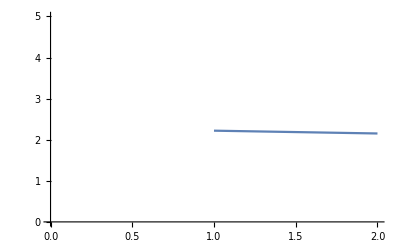

```mathematica
ListLinePlot[myRatio, PlotRange->{0,5}]
```

## Global Analysis:

### Parameters...

```mathematica
l=.4; m=.1; (*how wide your data is on your box/whisker plot*)
```

### 1203: Show change in nuc/cyto signal, background subtracted, all cells

#### Import

```mathematica
analysisFolder1203="/Volumes/BITTY/_long_timeframe_transient_mini/20171203_15h/4h15h_only/Analysis/"
```

/Volumes/BITTY/_long_timeframe_transient_mini/20171203_15h/4h15h_only/Analysis/

```mathematica
filesNT = FileNames[analysisFolder1203 <> "*NT*ROI.dat"];
filesTL =  FileNames[analysisFolder1203 <> "*TL*ROI.dat"] ;
filesTA = FileNames[analysisFolder1203 <> "*TA*ROI.dat"] ;
```

```mathematica
counts1203 = Length/@{filesNT,filesTL,filesTA};
```

```mathematica
mymaskfilesNT  = Table[<<(filesNT[[i]]),{i,1,Length@filesNT,1}]; 
mymaskfilesTL  = Table[<<(filesTL[[i]]),{i,1,Length@filesTL,1}]; 
mymaskfilesTA  = Table[<<(filesTA[[i]]),{i,1,Length@filesTA,1}]; 
(*  mymaskfiles  = Table[<<(filesTA[[i]]),{i,1,Length@filesTA,1}];   *)
Length/@mymaskfilesNT
bkgGIntNT =mymaskfilesNT[[All,1,1;;2,3,2]] ;
cytoGIntNT =mymaskfilesNT[[All,2,1;;2,3,2]] ;
nucGIntNT =mymaskfilesNT[[All,3,1;;2,3,2]] ;
```

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
Length/@mymaskfilesTL
bkgGIntTL =mymaskfilesTL[[All,1,1;;2,3,2]] ;
cytoGIntTL =mymaskfilesTL[[All,2,1;;2,3,2]] ;
nucGIntTL =mymaskfilesTL[[All,3,1;;2,3,2]] ;
```

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
Length/@mymaskfilesTA
Length@mymaskfilesTA
bkgGIntTA =mymaskfilesTA[[All,1,1;;2,3,2]] ;
cytoGIntTA =mymaskfilesTA[[All,2,1;;2,3,2]] ;
nucGIntTA =mymaskfilesTA[[All,3,1;;2,3,2]] ;
```

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

26

```mathematica
(*  myRatio = (nucGInt-bkgGInt)/(cytoGInt-bkgGInt)
```

```mathematica
myRatioTimeNT = {(nucGIntNT-bkgGIntNT)/(cytoGIntNT-bkgGIntNT)} //  Table[   Transpose[ {{4,15}, # [[1,i]]}  ],{i,1,Length@nucGIntNT}]& ;
myRatioTimeTL = {(nucGIntTL-bkgGIntTL)/(cytoGIntTL-bkgGIntTL)} //  Table[   Transpose[ {{4,15}, # [[1,i]]}  ],{i,1,Length@nucGIntTL}]& ;
myRatioTimeTA= {(nucGIntTA-bkgGIntTA)/(cytoGIntTA-bkgGIntTA)} //  Table[   Transpose[ {{4,15}, # [[1,i]]}  ],{i,1,Length@nucGIntTA}]& ;
```

#### Plotting the background subtracted nuc/cyto ratio over time

```mathematica
plotsNT = ListLinePlot[#,PlotStyle->{Darker[Red]}, ScalingFunctions->"Log"]&/@myRatioTimeNT;
```

```mathematica
plotsTL = ListLinePlot[#,PlotStyle->{Darker[Green]},ScalingFunctions->"Log"]&/@myRatioTimeTL;
```

```mathematica
plotsTA = ListLinePlot[#,PlotStyle->{Darker[Blue]},ScalingFunctions->"Log"]&/@myRatioTimeTA;
```

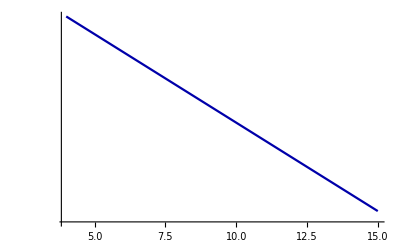

```mathematica
plotsTA[[1]]
```

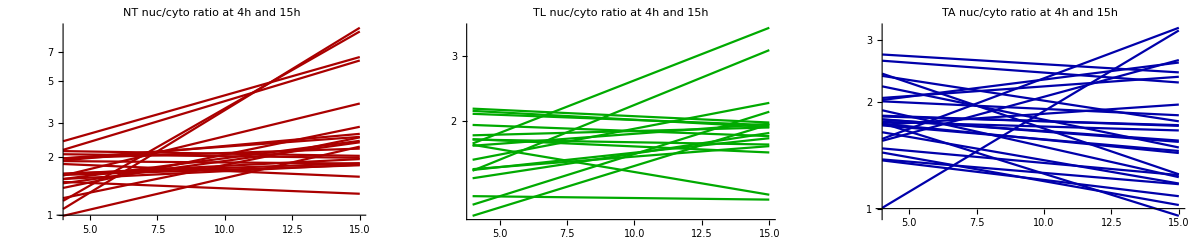

```mathematica
GraphicsRow[{  Show[plotsNT,PlotRange->{{4,15.1},{All,Log[15]}},AxesOrigin->{4,0},PlotLabel->"NT nuc/cyto ratio at 4h and 15h"]  ,
Show[plotsTL,PlotRange->{{4,15.1},{All,Log[15]}},AxesOrigin->{4,0}, PlotLabel->"TL nuc/cyto ratio at 4h and 15h" ]  ,  
Show[plotsTA,PlotRange->{{4,15.1},{All,Log[15]}},AxesOrigin->{4,0}, PlotLabel->"TA nuc/cyto ratio at 4h and 15h" ]   }]
```

#### Plotting the background subtracted nuc/cyto ratio over time

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
myRatioNT1203 = (nucGIntNT-bkgGIntNT)/(cytoGIntNT-bkgGIntNT);
myRatioTL1203 = (nucGIntTL-bkgGIntTL)/(cytoGIntTL-bkgGIntTL) ;
myRatioTA1203 = (nucGIntTA-bkgGIntTA)/(cytoGIntTA-bkgGIntTA) ;
```

```mathematica
plotsNTratio1203= ListPlot[#,PlotMarkers-> -Graphics-  ]&/@{myRatioNT1203};
```

```mathematica
plotsTLratio1203= ListPlot[#,PlotMarkers-> -Graphics- ]&/@{myRatioTL1203};
```

```mathematica
plotsTAratio1203= ListPlot[#,PlotMarkers-> -Graphics-  ]&/@{myRatioTA1203};
```

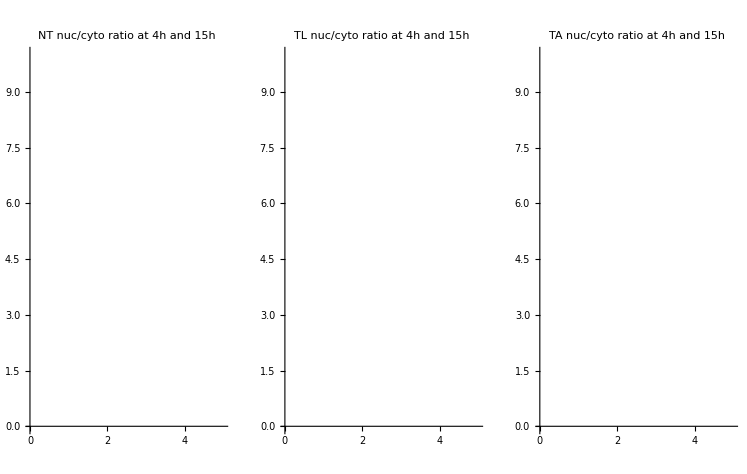

```mathematica
GraphicsRow[{  
Show[plotsNTratio1203,PlotRange->{{0,5},{0,10}},AxesOrigin->{0,0}, AspectRatio->2, PlotLabel->"NT nuc/cyto ratio at 4h and 15h" ]  ,  Show[plotsTLratio1203,PlotRange->{{0,5},{0,10}},AxesOrigin->{0,0}, AspectRatio->2, PlotLabel->"TL nuc/cyto ratio at 4h and 15h"]  ,
Show[plotsTAratio1203,PlotRange->{{0,5},{0,10}},AxesOrigin->{0,0}, AspectRatio->2, PlotLabel->"TA nuc/cyto ratio at 4h and 15h"]   
}]
```

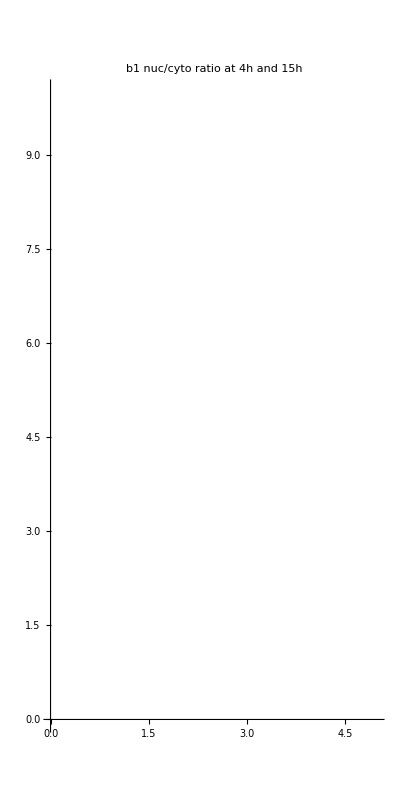

```mathematica
Show[{ plotsNTratio1203,plotsTLratio1203,plotsTAratio1203} ,  PlotRange->{{0,5},{0,10}},AxesOrigin->{0,0}, AspectRatio->2, PlotLabel->"b1 nuc/cyto ratio at 4h and 15h"  ]
```

#### Plotting the background subtracted nuc/cyto ratio over time: Ratio 15h/4h box/whisk

```mathematica
mypointsize = .02;
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
ratios1203 = 
{  Table[myRatioNT1203[[cell,2]] / myRatioNT1203[[cell,1]], {cell, 1, Length@myRatioNT1203}] ,
Table[myRatioTL1203[[cell,2]] / myRatioTL1203[[cell,1]], {cell, 1, Length@myRatioTL1203}] ,
Table[myRatioTA1203[[cell,2]] / myRatioTA1203[[cell,1]], {cell, 1, Length@myRatioTA1203}] };
a = ratios1203
(*Use Ratio2 to plot early vs late nuc/cyto ratio *)
```

{{1.29261,1.37432,1.12251,2.28761,1.63252,0.944933,0.95824,1.1874,2.36754,2.06684,1.19491,0.867763,2.73672,2.91141,2.07744,0.971625,0.858791,1.133,8.72878,1.57833,1.1225,7.57554},{2.04309,2.10512,0.932794,1.04967,1.42116,0.969789,1.21663,0.917883,0.734639,1.14516,0.921255,1.15267,1.75898,1.32256,0.978921,1.77543,0.905152,0.933316},{0.826254,0.871994,1.27612,0.792204,0.8513,0.671871,0.936043,3.17323,2.06106,0.945742,0.890219,0.913326,0.547099,0.863305,0.716288,1.14123,0.840705,0.647007,0.710576,0.519447,0.867985,1.1478,1.69202,0.744041,0.94519,0.846667}}

```mathematica
WMWtestNTTAvTLTAvNTTL1203= { MannWhitneyTest[ {a[[1]],a[[3]] }], MannWhitneyTest[ {a[[2]],a[[3]] }], MannWhitneyTest[ {a[[1]],a[[2]] }] }
```

{0.0000522757,0.00295985,0.0706231}

```mathematica
{{-Graphics-,.015},{-Graphics-,.015},{-Graphics-,.015}}
```

{{-Graphics-,0.015},{-Graphics-,0.015},{-Graphics-,0.015}}

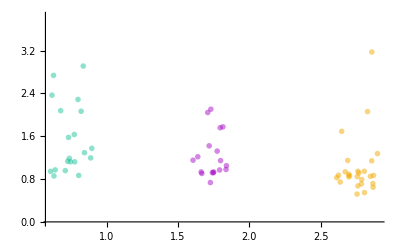

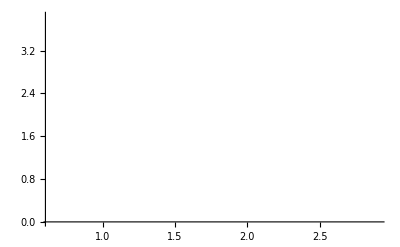

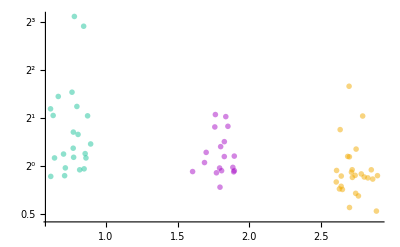

```mathematica
b = ListPlot[Table[ Thread[{Table[RandomReal[ {n-l,n-m} ], Length[a[[n]] ] ], a[[n]] }], {n,1,Length@a}] , PlotMarkers-> {{-Graphics-,mypointsize},{-Graphics-,mypointsize},{-Graphics-,mypointsize}}]
b1203points = b;
b = ListPlot[Table[ Thread[{Table[RandomReal[ {n-l,n-m} ], Length[a[[n]] ] ], a[[n]] }], {n,1,Length@a}] , PlotMarkers->  {-Graphics-,-Graphics-,-Graphics-}]
b1203=b;
b = ListPlot[Table[ Thread[{Table[RandomReal[ {n-l,n-m} ], Length[a[[n]] ] ], a[[n]] }], {n,1,Length@a}] , PlotMarkers-> {{-Graphics-,mypointsize},{-Graphics-,mypointsize},{-Graphics-,mypointsize}},  ScalingFunctions->"Log2"]
b1203pointslog = b;
```

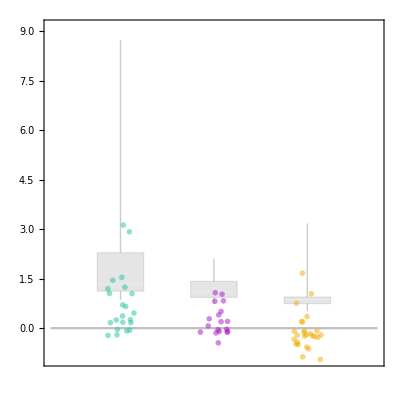

```mathematica
myBoxWhiskerPlot1203 = Show[  BoxWhiskerChart[a,{{"Whiskers",Thick},{"Fences",1,Opacity[0]}} ,ChartStyle->{{EdgeForm[{Gray, Thickness[Large]}  ]} , {Opacity[0.2,Gray]} } , AspectRatio->1  ] ,b,  Plot[x=0,{x,0,3.5}, PlotStyle->Opacity[0.5,Gray] ], AspectRatio -> 1]
```

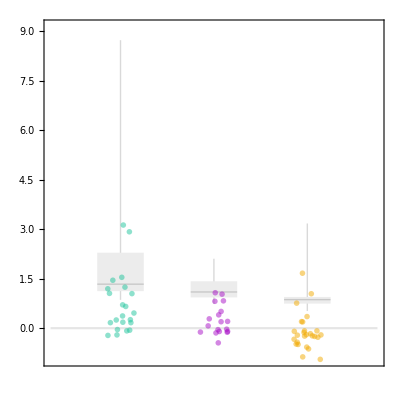

```mathematica
myBoxWhiskerPlot1203 = Show[  BoxWhiskerChart[a , {{"MedianMarker",Thick},{"Whiskers",Thick},{"Fences",1,Opacity[0]}},ChartBaseStyle-> Directive[ Opacity[0.15,Gray]  ]     , AspectRatio->1  ] ,b,  Plot[x=0,{x,0,3.5}, PlotStyle->Opacity[0.2,Gray] ], AspectRatio -> 1]
```

```mathematica
`
```

```mathematica
StandardDeviation/@a
```

{2.04943,0.416204,0.550014}

```mathematica
(* Bar chart not used 
b = ListPlot[Table[ Thread[{Table[RandomReal[ {n-.3,n + .3} ], Length[a[[n]] ] ], a[[n]] }], {n,1,Length@a}], PlotMarkers-> {-Graphics-,-Graphics-,-Graphics-} ]
```

```mathematica
(* Bar chart not used 
myChart0125 = Show[ BarChart[Mean/@a, ChartStyle->{{EdgeForm[Thickness[Large]]}, {Opacity[0,Gray]}} , AspectRatio->1] ,b]
```

#### Remake B&W plot

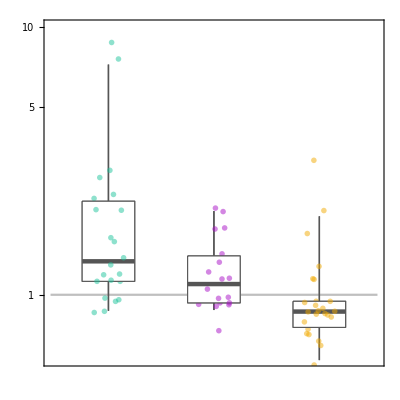

```mathematica
bwchart = BoxWhiskerChart[a,{ {"MedianMarker",Directive[Thickness[.008],Darker[Gray]]},{"Whiskers",Directive[Thick,Darker[Gray]]},{"Fences",1,Opacity[0]}} ,ChartStyle->{{EdgeForm[{Darker[Gray], Thickness[Large]}  ]} , {White} } , AspectRatio->1 ,ScalingFunctions->"Log2" ,{Method->{"BoxRange"->(Quantile[#,{.05,.25,.5,.75,.95},{{1,-1},{0,1}}]&)}}];
myBoxWhiskerPlot1203wctrl =  
Show[   bwchart,  Plot[x=0,{x,0.2,3.3}, PlotStyle->Opacity[0.5,Gray]],bwchart,b, AspectRatio -> 1,BaseStyle->{FontFamily->"Arial",FontSize->22},PlotRange-> {-.8,Log2[10]}]
```

#### Find out how many cells have positive accumulation AND, change magnitude of positive accumulation in order to count, such as accumulation greater than 0.5 to count...

Find the fraction of cells that are above 0, which means they have a positive gain in accumulation.....  {NT, TL, TA}

```mathematica
z=1;
 {  
Length@Cases[  a[[1]] , n_/; n>z] / Length@a[[1]]  //N , 
Length@Cases[  a[[2]] , n_/; n>z] / Length@a[[2]]  //N , 
Length@Cases[  a[[3]] , n_/; n>z]/ Length@a[[3]]  //N 
 }
```

{0.772727,0.555556,0.230769}

Find the fraction of cells that are above 0 BY A CERTAIN AMOUNT , which means they have a positive gain in accumulation ABOVE A CERTAIN AMOUNT.....  {NT, TL, TA}

```mathematica
zs = Table[z,{z,1,2, 0.1}]
```

{1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.}

```mathematica
atable = Table [ 
{Length@Cases[  a[[1]] , n_/; n>z] / Length@a[[1]]  //N , 
Length@Cases[  a[[2]] , n_/; n>z] / Length@a[[2]]  //N , 
Length@Cases[  a[[3]] , n_/; n>z]/ Length@a[[3]]  //N  } ,
{z,1,2, 0.1}] ;
atable// TableForm
```

0.772727 | 0.555556 | 0.230769
0.772727 | 0.5 | 0.230769
0.545455 | 0.388889 | 0.153846
0.5 | 0.333333 | 0.115385
0.454545 | 0.277778 | 0.115385
0.454545 | 0.222222 | 0.115385
0.409091 | 0.222222 | 0.115385
0.363636 | 0.222222 | 0.0769231
0.363636 | 0.111111 | 0.0769231
0.363636 | 0.111111 | 0.0769231
0.363636 | 0.111111 | 0.0769231

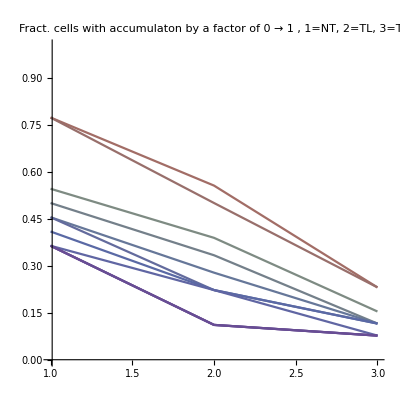

```mathematica
ListLinePlot[#,ColorFunction->"Rainbow" , PlotRange -> {{1,3},{0,1}} , AspectRatio->1,
 PlotLabel -> "Fract. cells with accumulaton by a factor of 0 → 1 , 1=NT, 2=TL, 3=TA"  ]&/@{atable}
```

### 1025: Show change in nuc/cyto signal, background subtracted, all cells

#### Import

```mathematica
(*StringDrop[analysisFolder,-8]
```

```mathematica
analysisFolder1025 = "/Volumes/BITTY/_long_timeframe_transient_mini/20181025_27_TA_TL_NT_15h/4h_15h_only/Analysis/"
analysisFolder1103 = "/Volumes/BITTY/_long_timeframe_transient_mini/20181103_15h_TL/4h15h_only/Analysis/"
```

/Volumes/BITTY/_long_timeframe_transient_mini/20181025_27_TA_TL_NT_15h/4h_15h_only/Analysis/

/Volumes/BITTY/_long_timeframe_transient_mini/20181103_15h_TL/4h15h_only/Analysis/

```mathematica
filesNT = FileNames[analysisFolder1025 <> "*NT*ROI.dat"];
filesTL = Join[ FileNames[analysisFolder1025 <> "*TL*ROI.dat"], FileNames[analysisFolder1103 <>   "*TL*ROI.dat"] ];
filesTA = FileNames[analysisFolder1025 <> "*TA*ROI.dat"];
counts1025 = {Length@filesNT,Length@filesTL,Length@filesTA};
```

```mathematica
mymaskfilesNT  = Table[<<(filesNT[[i]]),{i,1,Length@filesNT,1}]; 
mymaskfilesTL  = Table[<<(filesTL[[i]]),{i,1,Length@filesTL,1}]; 
mymaskfilesTA  = Table[<<(filesTA[[i]]),{i,1,Length@filesTA,1}]; 
(*  mymaskfiles  = Table[<<(filesTA[[i]]),{i,1,Length@filesTA,1}];   *)
Length/@mymaskfilesNT
bkgGIntNT =mymaskfilesNT[[All,1,1;;2,3,2]] ;
cytoGIntNT =mymaskfilesNT[[All,2,1;;2,3,2]] ;
nucGIntNT =mymaskfilesNT[[All,3,1;;2,3,2]] ;
```

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
Length/@mymaskfilesTL
bkgGIntTL =mymaskfilesTL[[All,1,1;;2,3,2]];
cytoGIntTL =mymaskfilesTL[[All,2,1;;2,3,2]];
nucGIntTL =mymaskfilesTL[[All,3,1;;2,3,2]];
```

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
Length/@mymaskfilesTA
Length@mymaskfilesTA
bkgGIntTA =mymaskfilesTA[[All,1,1;;2,3,2]];
cytoGIntTA =mymaskfilesTA[[All,2,1;;2,3,2]];
nucGIntTA =mymaskfilesTA[[All,3,1;;2,3,2]];
```

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

17

```mathematica
(*  myRatio = (nucGInt-bkgGInt)/(cytoGInt-bkgGInt)
```

```mathematica
myRatioTimeNT = {(nucGIntNT-bkgGIntNT)/(cytoGIntNT-bkgGIntNT)} //  Table[   Transpose[ {{4,15}, # [[1,i]]}  ],{i,1,Length@nucGIntNT}]& ;
myRatioTimeTL = {(nucGIntTL-bkgGIntTL)/(cytoGIntTL-bkgGIntTL)} //  Table[   Transpose[ {{4,15}, # [[1,i]]}  ],{i,1,Length@nucGIntTL}]& ;
myRatioTimeTA= {(nucGIntTA-bkgGIntTA)/(cytoGIntTA-bkgGIntTA)} //  Table[   Transpose[ {{4,15}, # [[1,i]]}  ],{i,1,Length@nucGIntTA}]& ;
```

#### Plotting the background subtracted nuc/cyto ratio over time

```mathematica
Length@myRatioTimeTA
```

17

```mathematica
plotsNT = ListLinePlot[#,PlotStyle->{Darker[Red]}, ScalingFunctions->"Log"]&/@myRatioTimeNT;
```

```mathematica
plotsTL = ListLinePlot[#,PlotStyle->{Darker[Green]},ScalingFunctions->"Log"]&/@myRatioTimeTL;
```

```mathematica
plotsTA = ListLinePlot[#,PlotStyle->{Darker[Blue]},ScalingFunctions->"Log"]&/@myRatioTimeTA;
```

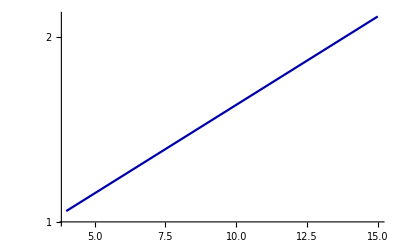

```mathematica
plotsTA[[1]]
```

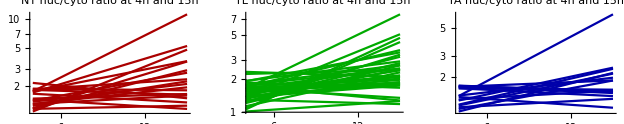

```mathematica
GraphicsRow[{  Show[plotsNT,PlotRange->{{4,15.1},{All,Log[15]}},AxesOrigin->{4,0},PlotLabel->"NT nuc/cyto ratio at 4h and 15h"]  ,
Show[plotsTL,PlotRange->{{4,15.1},{All,Log[15]}},AxesOrigin->{4,0}, PlotLabel->"TL nuc/cyto ratio at 4h and 15h" ]  ,  
Show[plotsTA,PlotRange->{{4,15.1},{All,Log[15]}},AxesOrigin->{4,0}, PlotLabel->"TA nuc/cyto ratio at 4h and 15h" ]   }]
```

#### Plotting the background subtracted nuc/cyto ratio over time

```mathematica
myRatioNT1025 = (nucGIntNT-bkgGIntNT)/(cytoGIntNT-bkgGIntNT)
myRatioTL1025 =(nucGIntTL-bkgGIntTL)/(cytoGIntTL-bkgGIntTL)
myRatioTA1025 =(nucGIntTA-bkgGIntTA)/(cytoGIntTA-bkgGIntTA)
```

{{1.46024,1.63137},{1.14719,2.89887},{1.82669,2.328},{1.80142,1.6035},{1.15554,3.57576},{1.73722,11.1756},{2.13384,1.47298},{1.73243,3.6105},{1.35652,2.08073},{1.06929,4.76414},{1.22612,2.2168},{1.28505,1.91796},{1.14051,1.23112},{1.38801,2.72774},{1.64358,1.3311},{1.42631,1.13889},{1.85766,1.78421},{1.69192,5.20543},{1.28696,1.5732}}

{{2.22299,2.42947},{1.31862,2.78776},{1.63481,2.01176},{1.29861,1.18565},{1.63911,1.82683},{1.13351,2.30025},{1.37255,5.09533},{1.01485,1.26182},{1.92265,2.89252},{1.69574,3.65765},{2.32299,2.09288},{1.64819,1.34942},{1.73061,1.27786},{1.08666,4.32855},{1.41247,1.79905},{1.3691,1.74474},{1.48286,1.96982},{1.57431,1.77496},{1.54402,2.15964},{1.77034,1.7901},{1.36005,1.87179},{1.56813,2.09095},{1.76639,2.48365},{1.90789,3.48896},{1.06074,4.72738},{1.44937,2.39795},{1.63881,2.49601},{1.53395,1.87019},{1.23449,3.32838},{1.7887,2.67753},{1.85939,1.66726},{1.25961,2.44978},{1.20977,2.65939},{1.63094,7.72119},{1.38848,3.18408}}

{{1.04335,2.16312},{1.39665,6.52382},{1.69028,1.53361},{1.37215,1.12047},{1.09468,1.8726},{1.65394,1.50753},{1.70101,1.51197},{1.16958,2.13182},{1.18822,2.33431},{1.68176,1.47867},{1.28445,2.38547},{1.62189,1.57482},{1.66386,1.87528},{1.13091,1.32496},{1.40984,1.97474},{1.3108,1.5484},{1.6162,1.39533}}

```mathematica
(*
plotsb1= ListPlot[#,PlotStyle->{Darker[Red]}, ScalingFunctions->"Log"]&/@{myRatio2};
```

```mathematica
(*
plotsb2= ListPlot[#,PlotStyle->{Darker[Blue]}, ScalingFunctions->"Log"]&/@{myRatio2};
```

```mathematica
(*
plotsb3= ListPlot[#,PlotStyle->{Darker[Green]}, ScalingFunctions->"Log"]&/@{myRatio2};
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
plotsNTratio= ListPlot[#,PlotMarkers -> -Graphics-, PlotStyle->{Darker[Red]}]&/@{myRatioNT1025};
```

```mathematica
plotsTLratio= ListPlot[#,PlotMarkers -> -Graphics-, PlotStyle->{Darker[Green]}]&/@{myRatioTL1025};
```

```mathematica
plotsTAratio= ListPlot[#,PlotMarkers -> -Graphics-, PlotStyle->{Darker[Blue]}]&/@{myRatioTA1025};
```

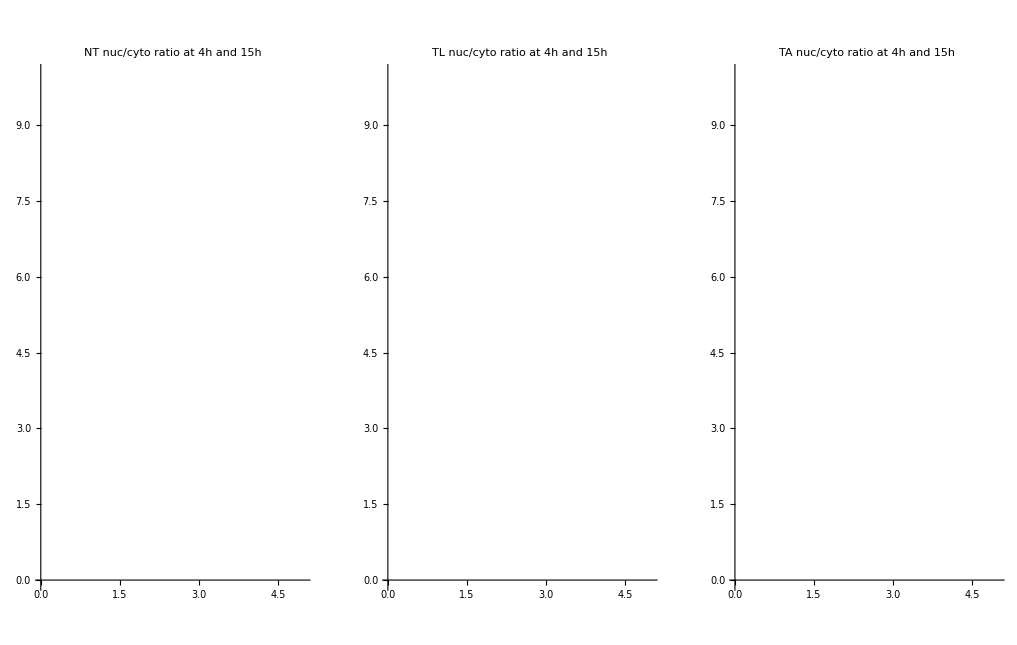

```mathematica
GraphicsRow[{  
Show[plotsNTratio,PlotRange->{{0,5},{0,10}},AxesOrigin->{0,0}, AspectRatio->2, PlotLabel->"NT nuc/cyto ratio at 4h and 15h" ]  ,  Show[plotsTLratio,PlotRange->{{0,5},{0,10}},AxesOrigin->{0,0}, AspectRatio->2, PlotLabel->"TL nuc/cyto ratio at 4h and 15h"]  ,
Show[plotsTAratio,PlotRange->{{0,5},{0,10}},AxesOrigin->{0,0}, AspectRatio->2, PlotLabel->"TA nuc/cyto ratio at 4h and 15h"]   
}]
```

```mathematica
Show[{ plotsNTratio,plotsTLratio,plotsTAratio} ,  PlotRange->{{0,5},{0,10}},AxesOrigin->{0,0}, AspectRatio->2, PlotLabel->"b1 nuc/cyto ratio at 4h and 15h"  ]
```

-Graphics-

#### Plotting the background subtracted nuc/cyto ratio over time: Ratio 15h/4h box/whisk

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
ratios1025 = {  Table[myRatioNT1025[[cell,2]] / myRatioNT1025[[cell,1]], {cell, 1, Length@myRatioNT1025}] ,
Table[myRatioTL1025[[cell,2]] / myRatioTL1025[[cell,1]], {cell, 1, Length@myRatioTL1025}] ,
Table[myRatioTA1025[[cell,2]] / myRatioTA1025[[cell,1]], {cell, 1, Length@myRatioTA1025}] }
a = ratios1025
(*Use Ratio2 to plot early vs late nuc/cyto ratio *)
```

{{1.1172,2.52694,1.27444,0.890132,3.09445,6.43303,0.690295,2.08406,1.53387,4.45543,1.80799,1.49251,1.07945,1.96522,0.809877,0.798489,0.960463,3.07665,1.22241},{1.09289,2.11415,1.23058,0.91301,1.11453,2.02932,3.71232,1.24335,1.50444,2.15697,0.900941,0.818726,0.738385,3.98334,1.27368,1.27438,1.32839,1.12745,1.39871,1.01116,1.37627,1.3334,1.40606,1.8287,4.45667,1.65448,1.52306,1.2192,2.69616,1.49691,0.896675,1.94487,2.19827,4.73419,2.29321},{2.07324,4.67104,0.907312,0.81658,1.71063,0.911479,0.888867,1.82273,1.96454,0.879237,1.8572,0.970977,1.12706,1.17159,1.40068,1.18126,0.863339}}

{{1.1172,2.52694,1.27444,0.890132,3.09445,6.43303,0.690295,2.08406,1.53387,4.45543,1.80799,1.49251,1.07945,1.96522,0.809877,0.798489,0.960463,3.07665,1.22241},{1.09289,2.11415,1.23058,0.91301,1.11453,2.02932,3.71232,1.24335,1.50444,2.15697,0.900941,0.818726,0.738385,3.98334,1.27368,1.27438,1.32839,1.12745,1.39871,1.01116,1.37627,1.3334,1.40606,1.8287,4.45667,1.65448,1.52306,1.2192,2.69616,1.49691,0.896675,1.94487,2.19827,4.73419,2.29321},{2.07324,4.67104,0.907312,0.81658,1.71063,0.911479,0.888867,1.82273,1.96454,0.879237,1.8572,0.970977,1.12706,1.17159,1.40068,1.18126,0.863339}}

```mathematica
WMWtestNTTAvTLTAvNTTL0125 = { MannWhitneyTest[ {a[[1]],a[[3]] }], MannWhitneyTest[ {a[[2]],a[[3]] }], MannWhitneyTest[ {a[[1]],a[[2]] }] }
```

{0.374944,0.12812,0.856263}

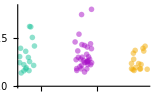

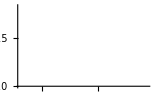

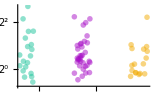

```mathematica
b = ListPlot[Table[ Thread[{Table[RandomReal[ {n-l,n-m} ], Length[a[[n]] ] ], a[[n]] }], {n,1,Length@a}] , PlotMarkers-> {{-Graphics-,.01},{-Graphics-,.01},{-Graphics-,.01}}]
b1025points = b;
b = ListPlot[Table[ Thread[{Table[RandomReal[ {n-l,n-m} ], Length[a[[n]] ] ], a[[n]] }], {n,1,Length@a}] , PlotMarkers->  {-Graphics-,-Graphics-,-Graphics-}]
b1025 = b;
b = ListPlot[Table[ Thread[{Table[RandomReal[ {n-l,n-m} ], Length[a[[n]] ] ], a[[n]] }], {n,1,Length@a}] , PlotMarkers-> {{-Graphics-,mypointsize},{-Graphics-,mypointsize},{-Graphics-,mypointsize}},  ScalingFunctions->"Log2"]
b1025pointslog = b;
```

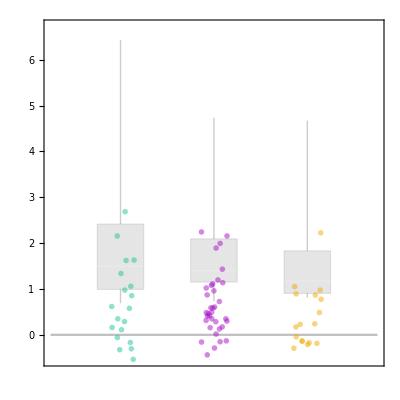

```mathematica
myBoxWhiskerPlot0125 = Show[  BoxWhiskerChart[a,{{"Whiskers",Thick},{"Fences",1,Opacity[0]}} ,ChartStyle->{{EdgeForm[{Gray, Thickness[Large]}  ]} , {Opacity[0.2,Gray]} } , AspectRatio->1  ] ,b,  Plot[x=0,{x,0,3.5}, PlotStyle->Opacity[0.5,Gray] ], AspectRatio -> 1]
```

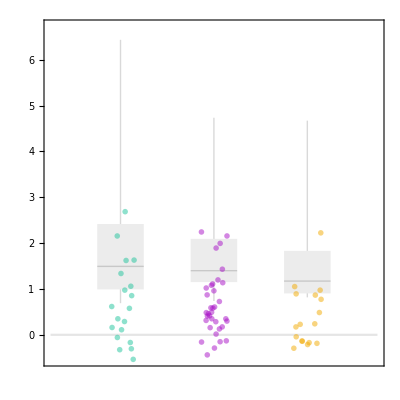

```mathematica
myBoxWhiskerPlot0125 = Show[  BoxWhiskerChart[a , {{"MedianMarker",Thick},{"Whiskers",Thick},{"Fences",1,Opacity[0]}},ChartBaseStyle-> Directive[ Opacity[0.15,Gray]  ]     , AspectRatio->1  ] ,b,  Plot[x=0,{x,0,3.5}, PlotStyle->Opacity[0.2,Gray] ], AspectRatio -> 1]
```

```mathematica
StandardDeviation/@a
```

{1.46166,1.01246,0.930001}

```mathematica
(* Bar chart not used 
b = ListPlot[Table[ Thread[{Table[RandomReal[ {n-.3,n + .3} ], Length[a[[n]] ] ], a[[n]] }], {n,1,Length@a}], PlotMarkers-> {-Graphics-,-Graphics-,-Graphics-} ]
```

```mathematica
(* Bar chart not used 
myChart0125 = Show[ BarChart[Mean/@a, ChartStyle->{{EdgeForm[Thickness[Large]]}, {Opacity[0,Gray]}} , AspectRatio->1] ,b]
```

#### Remake B&W plot

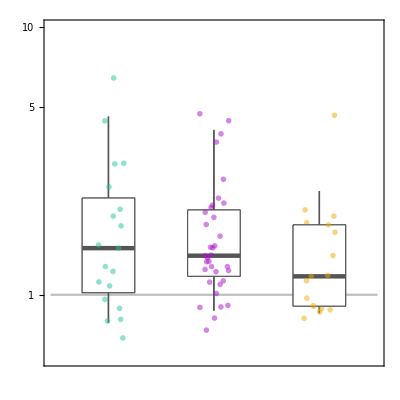

```mathematica
bwchart = BoxWhiskerChart[a,{ {"MedianMarker",Directive[Thickness[.008],Darker[Gray]]},{"Whiskers",Directive[Thick,Darker[Gray]]},{"Fences",1,Opacity[0]}} ,ChartStyle->{{EdgeForm[{Darker[Gray], Thickness[Large]}  ]} , {White} } , AspectRatio->1 ,ScalingFunctions->"Log2" ,{Method->{"BoxRange"->(Quantile[#,{.05,.25,.5,.75,.95},{{1,-1},{0,1}}]&)}}];
myBoxWhiskerPlot1025wctrl =  
Show[   bwchart,  Plot[x=0,{x,0.2,3.3}, PlotStyle->Opacity[0.5,Gray]],bwchart,b, AspectRatio -> 1,BaseStyle->{FontFamily->"Arial",FontSize->22},PlotRange-> {-.8,Log2[10]}]
```

#### Find out how many cells have positive accumulation AND, change magnitude of positive accumulation in order to count, such as accumulation greater than 0.5 to count...

Find the fraction of cells that are above 0, which means they have a positive gain in accumulation.....  {NT, TL, TA}

```mathematica
z=1;
 {  
Length@Cases[  a[[1]] , n_/; n>z] / Length@a[[1]]  //N , 
Length@Cases[  a[[2]] , n_/; n>z] / Length@a[[2]]  //N , 
Length@Cases[  a[[3]] , n_/; n>z]/ Length@a[[3]]  //N 
 }
```

{0.736842,0.857143,0.588235}

Find the fraction of cells that are above 0 BY A CERTAIN AMOUNT , which means they have a positive gain in accumulation ABOVE A CERTAIN AMOUNT.....  {NT, TL, TA}

```mathematica
zs = Table[z,{z,1,2, 0.1}]
```

{1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.}

```mathematica
atable = Table [ 
{Length@Cases[  a[[1]] , n_/; n>z] / Length@a[[1]]  //N , 
Length@Cases[  a[[2]] , n_/; n>z] / Length@a[[2]]  //N , 
Length@Cases[  a[[3]] , n_/; n>z]/ Length@a[[3]]  //N  } ,
{z,1,2, 0.1}];
atable // TableForm
```

0.736842 | 0.857143 | 0.588235
0.684211 | 0.8 | 0.588235
0.631579 | 0.742857 | 0.411765
0.526316 | 0.6 | 0.411765
0.526316 | 0.485714 | 0.411765
0.473684 | 0.428571 | 0.352941
0.421053 | 0.371429 | 0.352941
0.421053 | 0.342857 | 0.352941
0.421053 | 0.342857 | 0.294118
0.368421 | 0.314286 | 0.176471
0.315789 | 0.285714 | 0.117647

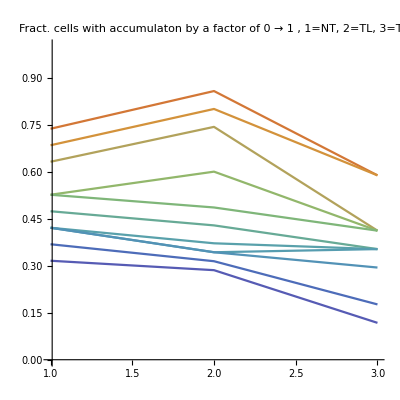

```mathematica
ListLinePlot[#,ColorFunction->"Rainbow" , PlotRange -> {{1,3},{0,1}} , AspectRatio->1,
 PlotLabel -> "Fract. cells with accumulaton by a factor of 0 → 1 , 1=NT, 2=TL, 3=TA"  ]&/@{atable}
```

### 01-19/21-2019: Show change in nuc/cyto signal, background subtracted, all cells

#### Import

```mathematica
analysisFolder = "/Volumes/BITTY/_long_timeframe_transient_mini/20190119_15h/4h15h_only/Analysis/"
```

/Volumes/BITTY/_long_timeframe_transient_mini/20190119_15h/4h15h_only/Analysis/

```mathematica
filesb1 = FileNames[analysisFolder <> "*b1*myROI.dat"];
filesb2 = FileNames[analysisFolder<> "*b2*ROI.dat"];
filesb3 = FileNames[analysisFolder <> "*b3*ROI.dat"];
counts0119 = {Length@filesb1,Length@filesb2,Length@filesb3}
```

{7,11,3}

```mathematica
mymaskfilesb1  = Table[<<(filesb1[[i]]),{i,1,Length@filesb1,1}]; 
(*  mymaskfiles  = Table[<<(filesTA[[i]]),{i,1,Length@filesTA,1}];   *)
Length/@mymaskfilesb1
bkgGIntb1 =mymaskfilesb1[[All,1,1;;2,3,2]];
cytoGIntb1 =mymaskfilesb1[[All,2,1;;2,3,2]];
nucGIntb1 =mymaskfilesb1[[All,3,1;;2,3,2]];
```

{30,30,30,30,30,30,30}

```mathematica
mymaskfilesb2  = Table[<<(filesb2[[i]]),{i,1,Length@filesb2,1}]; 
(*  mymaskfiles  = Table[<<(filesTA[[i]]),{i,1,Length@filesTA,1}];   *)
Length/@mymaskfilesb2
bkgGIntb2 =mymaskfilesb2[[All,1,1;;2,3,2]];
cytoGIntb2 =mymaskfilesb2[[All,2,1;;2,3,2]];
nucGIntb2 =mymaskfilesb2[[All,3,1;;2,3,2]];
```

{30,30,30,30,30,30,30,30,30,30,30}

```mathematica
mymaskfilesb3  = Table[<<(filesb3[[i]]),{i,1,Length@filesb3,1}]; 
(*  mymaskfiles  = Table[<<(filesTA[[i]]),{i,1,Length@filesTA,1}];   *)
Length/@mymaskfilesb3
bkgGIntb3 =mymaskfilesb3[[All,1,1;;2,3,2]];
cytoGIntb3 =mymaskfilesb3[[All,2,1;;2,3,2]];
nucGIntb3 =mymaskfilesb3[[All,3,1;;2,3,2]];
```

{30,30,30}

```mathematica
myRatioTimeb1 = {(nucGIntb1-bkgGIntb1)/(cytoGIntb1-bkgGIntb1)} //  Table[   Transpose[ {{4,15}, # [[1,i]]}  ],{i,1,Length@nucGIntb1}]& ;
myRatioTimeb2 = {(nucGIntb2-bkgGIntb2)/(cytoGIntb2-bkgGIntb2)} //  Table[   Transpose[ {{4,15}, # [[1,i]]}  ],{i,1,Length@nucGIntb2}]& ;
myRatioTimeb3 = {(nucGIntb3-bkgGIntb3)/(cytoGIntb3-bkgGIntb3)} //  Table[   Transpose[ {{4,15}, # [[1,i]]}  ],{i,1,Length@nucGIntb3}]& ;
```

#### Plotting the background subtracted nuc/cyto ratio over time

```mathematica
plotsb1= ListLinePlot[#,PlotStyle->{Darker[Green]}, ScalingFunctions->"Log"]&/@myRatioTimeb1;
plotsb2 = ListLinePlot[#,PlotStyle->{Darker[Blue]},ScalingFunctions->"Log"]&/@myRatioTimeb2;
plotsb3 = ListLinePlot[#,PlotStyle->{Darker[Red]},ScalingFunctions->"Log"]&/@myRatioTimeb3;
```

```mathematica
plotsb3[[1]];
```

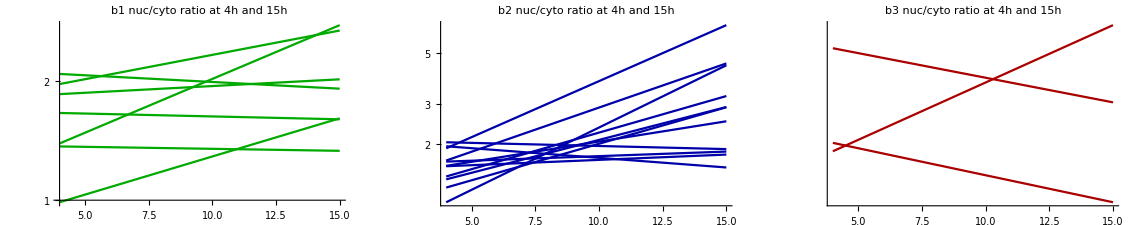

```mathematica
GraphicsRow[{  Show[plotsb1,PlotRange->{{4,15.1},{All,Log[15]}},AxesOrigin->{4,0}, PlotLabel->"b1 nuc/cyto ratio at 4h and 15h" ]  ,  Show[plotsb2,PlotRange->{{4,15.1},{All,Log[15]}},AxesOrigin->{4,0},PlotLabel->"b2 nuc/cyto ratio at 4h and 15h"]  ,
Show[plotsb3,PlotRange->{{4,15.1},{All,Log[15]}},AxesOrigin->{4,0},PlotLabel->"b3 nuc/cyto ratio at 4h and 15h"]        }]
```

#### Plotting the background subtracted nuc/cyto ratio over time

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
myRatiob1a = (nucGIntb1 - bkgGIntb1)/(cytoGIntb1- bkgGIntb1)
(*Use Ratio2 to plot early vs late nuc/cyto ratio *)
```

{{2.08266,1.91173},{1.8521,2.01868},{1.39037,2.76543},{1.96357,2.68022},{1.36668,1.33232},{1.66008,1.6},{0.98815,1.60926}}

```mathematica
myRatiob2a = (nucGIntb2 - bkgGIntb2)/(cytoGIntb2 - bkgGIntb2)
(*Use Ratio2 to plot early vs late nuc/cyto ratio *)
```

{{1.60834,2.51733},{1.60215,1.80142},{1.69654,4.50292},{1.40423,2.90499},{1.11561,4.4205},{1.95831,1.58238},{1.67829,1.85649},{1.44547,3.24407},{2.03881,1.90327},{1.29292,2.89843},{1.91822,6.61577}}

```mathematica
myRatiob3a = (nucGIntb3 - bkgGIntb3)/(cytoGIntb3 - bkgGIntb3)
(*Use Ratio2 to plot early vs late nuc/cyto ratio *)
```

{{1.21466,1.88372},{1.73835,1.43997},{1.25073,1.01725}}

```mathematica
plotsb1a= ListPlot[# , PlotMarkers -> -Graphics- ]&/@{myRatiob1a};
```

```mathematica
plotsb2a= ListPlot[#,PlotMarkers -> -Graphics- ]&/@{myRatiob2a};
```

```mathematica
plotsb3a= ListPlot[#,PlotMarkers ->-Graphics-  ]&/@{myRatiob3a};
```

Show::gcomb: Could not combine the graphics objects in Show[xylineplot,{},PlotRange→{{0,5},{0,10}},AxesOrigin→{0,0},AspectRatio→2,PlotLabel→b1 nuc/cyto ratio at 4h and 15h].

Show::gcomb: Could not combine the graphics objects in Show[xylineplot,{},PlotRange→{{0,5},{0,10}},AxesOrigin→{0,0},AspectRatio→2,PlotLabel→b2 nuc/cyto ratio at 4h and 15h].

Show::gcomb: Could not combine the graphics objects in Show[xylineplot,{},PlotRange→{{0,5},{0,10}},AxesOrigin→{0,0},AspectRatio→2,PlotLabel→b3 nuc/cyto ratio at 4h and 15h].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

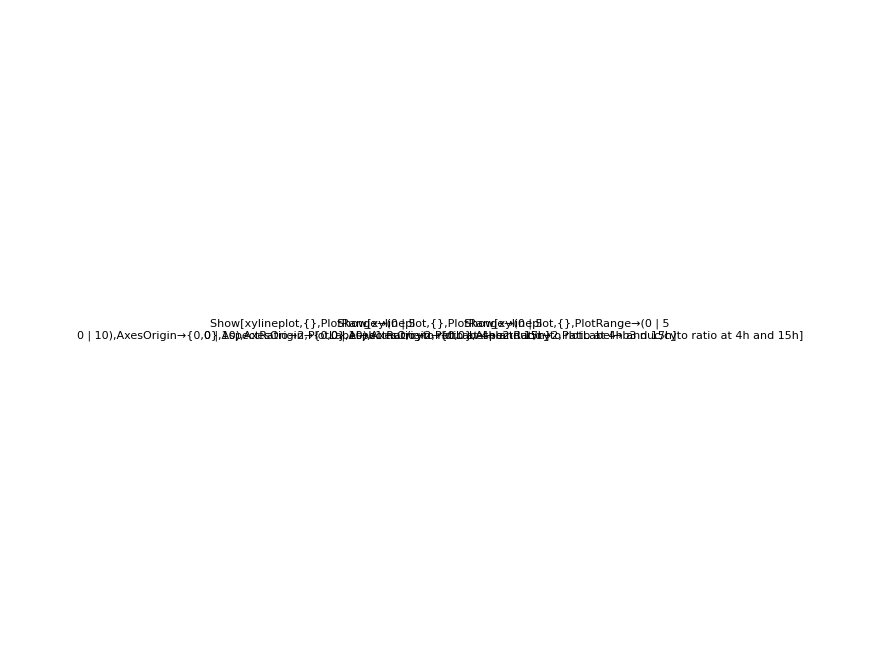

```mathematica
GraphicsRow[{  
Show[xylineplot, plotsb1a,PlotRange->{{0,5},{0,10}},AxesOrigin->{0,0}, AspectRatio->2, PlotLabel->"b1 nuc/cyto ratio at 4h and 15h" ]  ,  Show[xylineplot, plotsb2a,PlotRange->{{0,5},{0,10}},AxesOrigin->{0,0}, AspectRatio->2, PlotLabel->"b2 nuc/cyto ratio at 4h and 15h"]  ,
Show[xylineplot, plotsb3a,PlotRange->{{0,5},{0,10}},AxesOrigin->{0,0}, AspectRatio->2, PlotLabel->"b3 nuc/cyto ratio at 4h and 15h"]   
}]
```

Show::gcomb: Could not combine the graphics objects in ….

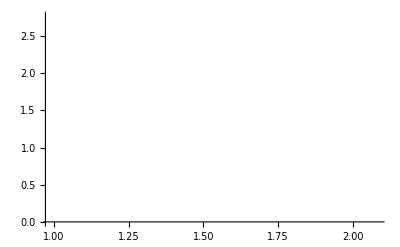
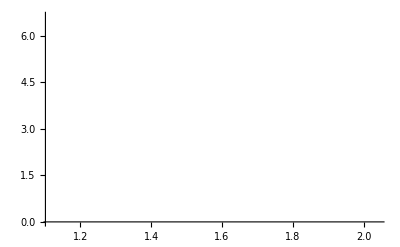
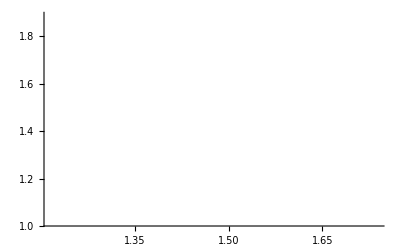
Show[{{-Graphics-},{-Graphics-},{-Graphics-},xylineplot},PlotRange→{{0,5},{0,10}},AxesOrigin→{0,0},AspectRatio→2,PlotLabel→Blind 1: nuc/cyto ratio at 4h and 15h]

```mathematica
Show[{ plotsb1a,plotsb2a,plotsb3a,xylineplot} ,  PlotRange->{{0,5},{0,10}},AxesOrigin->{0,0}, AspectRatio->2, PlotLabel->"Blind 1: nuc/cyto ratio at 4h and 15h"  ]
```

#### Plotting the background subtracted nuc/cyto ratio over time: Ratio 15h/4h box/whisk

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
ratios0119 = {  Table[myRatiob1a[[cell,2]] / myRatiob1a[[cell,1]], {cell, 1, Length@myRatiob1a}] ,
Table[myRatiob2a[[cell,2]] / myRatiob2a[[cell,1]], {cell, 1, Length@myRatiob2a}] ,
Table[myRatiob3a[[cell,2]] / myRatiob3a[[cell,1]], {cell, 1, Length@myRatiob3a}] }
(*Use Ratio2 to plot early vs late nuc/cyto ratio *)
a = ratios0119
(*Use Ratio2 to plot early vs late nuc/cyto ratio *)
```

{{0.917928,1.08994,1.98899,1.36497,0.974862,0.963811,1.62856},{1.56517,1.12437,2.65418,2.06874,3.96241,0.808034,1.10618,2.2443,0.93352,2.24177,3.4489},{1.55082,0.828354,0.813324}}

{{0.917928,1.08994,1.98899,1.36497,0.974862,0.963811,1.62856},{1.56517,1.12437,2.65418,2.06874,3.96241,0.808034,1.10618,2.2443,0.93352,2.24177,3.4489},{1.55082,0.828354,0.813324}}

```mathematica
WMWtestNTTAvTLTAvNTTL0119 = { MannWhitneyTest[ {a[[1]],a[[3]] }], MannWhitneyTest[ {a[[2]],a[[3]] }], MannWhitneyTest[ {a[[1]],a[[2]] }] }
```

{0.254451,0.119471,0.12365}

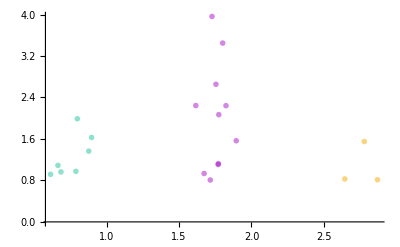

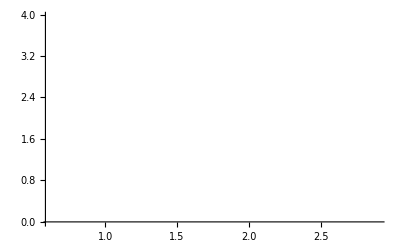

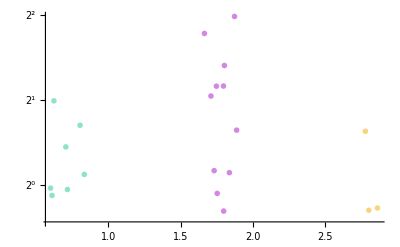

```mathematica
b = ListPlot[Table[ Thread[{Table[RandomReal[ {n-l,n-m} ], Length[a[[n]] ] ], a[[n]] }], {n,1,Length@a}] , PlotMarkers-> {{-Graphics-,.01},{-Graphics-,.01},{-Graphics-,0.01}}]
b0119points = b;
b = ListPlot[Table[ Thread[{Table[RandomReal[ {n-l,n-m} ], Length[a[[n]] ] ], a[[n]] }], {n,1,Length@a}] , PlotMarkers->  {-Graphics-,-Graphics-,-Graphics-}]
b0119 = b;
b = ListPlot[Table[ Thread[{Table[RandomReal[ {n-l,n-m} ], Length[a[[n]] ] ], a[[n]] }], {n,1,Length@a}] , PlotMarkers-> {{-Graphics-,mypointsize},{-Graphics-,mypointsize},{-Graphics-,mypointsize}},  ScalingFunctions->"Log2"]
b0119pointslog = b;
```

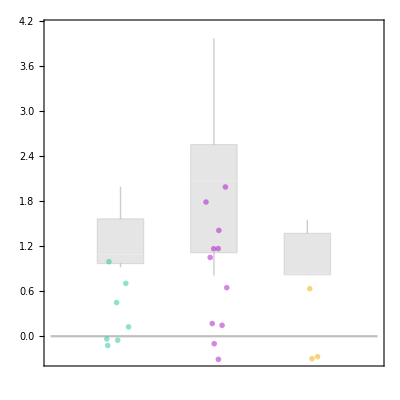

```mathematica
myBoxWhiskerPlot0119 = Show[  BoxWhiskerChart[a,{{"Whiskers",Thick},{"Fences",1,Opacity[0]}} ,ChartStyle->{{EdgeForm[{Gray, Thickness[Large]}  ]} , {Opacity[0.2,Gray]} } , AspectRatio->1  ] ,b,  Plot[x=0,{x,0,3.5}, PlotStyle->Opacity[0.5,Gray] ], AspectRatio -> 1]
```

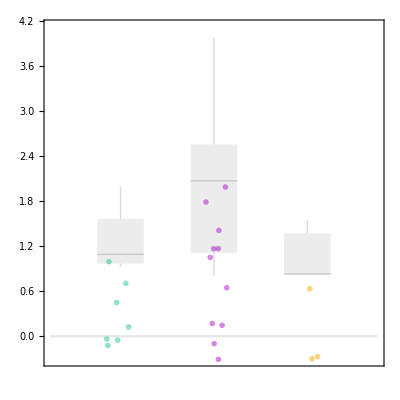

```mathematica
myBoxWhiskerPlot0119 = Show[  BoxWhiskerChart[a , {{"MedianMarker",Thick},{"Whiskers",Thick},{"Fences",1,Opacity[0]}},ChartBaseStyle-> Directive[ Opacity[0.15,Gray]  ]     , AspectRatio->1  ] ,b,  Plot[x=0,{x,0,3.5}, PlotStyle->Opacity[0.2,Gray] ], AspectRatio -> 1]
```

```mathematica
StandardDeviation/@a
```

{0.406518,1.0398,0.421522}

#### Remake B&W plot

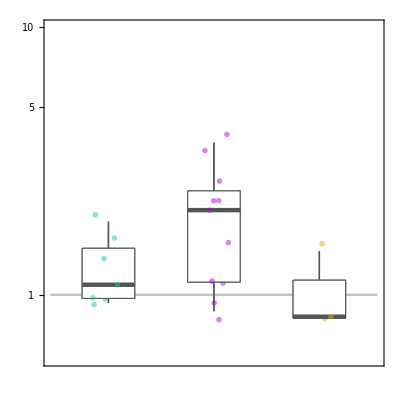

```mathematica
bwchart = BoxWhiskerChart[a,{ {"MedianMarker",Directive[Thickness[.008],Darker[Gray]]},{"Whiskers",Directive[Thick,Darker[Gray]]},{"Fences",1,Opacity[0]}} ,ChartStyle->{{EdgeForm[{Darker[Gray], Thickness[Large]}  ]} , {White} } , AspectRatio->1 ,ScalingFunctions->"Log2" ,{Method->{"BoxRange"->(Quantile[#,{.05,.25,.5,.75,.95},{{1,-1},{0,1}}]&)}}];
myBoxWhiskerPlot0119wctrl =  
Show[   bwchart,  Plot[x=0,{x,0.2,3.3}, PlotStyle->Opacity[0.5,Gray]],bwchart,b, AspectRatio -> 1,BaseStyle->{FontFamily->"Arial",FontSize->22},PlotRange-> {-.8,Log2[10]}]
```

#### Find out how many cells have positive accumulation AND, change magnitude of positive accumulation in order to count, such as accumulation greater than 0.5 to count...

Find the fraction of cells that are above 0, which means they have a positive gain in accumulation.....  {NT, TL, TA}

```mathematica
z=1;
 {  
Length@Cases[  a[[1]] , n_/; n>z] / Length@a[[1]]  //N , 
Length@Cases[  a[[2]] , n_/; n>z] / Length@a[[2]]  //N , 
Length@Cases[  a[[3]] , n_/; n>z]/ Length@a[[3]]  //N 
 }
```

{0.571429,0.818182,0.333333}

Find the fraction of cells that are above 0 BY A CERTAIN AMOUNT , which means they have a positive gain in accumulation ABOVE A CERTAIN AMOUNT.....  {NT, TL, TA}

```mathematica
zs = Table[z,{z,1,2, 0.1}]
```

{1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.}

```mathematica
atable = Table [ 
{Length@Cases[  a[[1]] , n_/; n>z] / Length@a[[1]]  //N , 
Length@Cases[  a[[2]] , n_/; n>z] / Length@a[[2]]  //N , 
Length@Cases[  a[[3]] , n_/; n>z]/ Length@a[[3]]  //N  } ,
{z,1,2, 0.1}]
```

{{0.571429,0.818182,0.333333},{0.428571,0.818182,0.333333},{0.428571,0.636364,0.333333},{0.428571,0.636364,0.333333},{0.285714,0.636364,0.333333},{0.285714,0.636364,0.333333},{0.285714,0.545455,0.},{0.142857,0.545455,0.},{0.142857,0.545455,0.},{0.142857,0.545455,0.},{0.,0.545455,0.}}

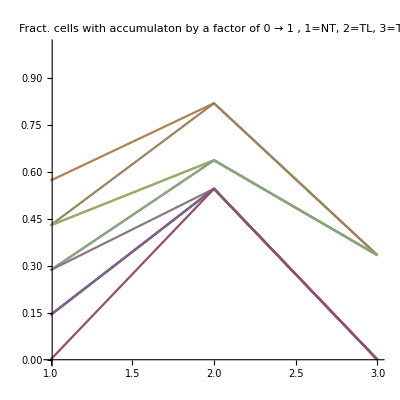

```mathematica
ListLinePlot[#,ColorFunction->"Rainbow" , PlotRange -> {{1,3},{0,1}} , AspectRatio->1,
 PlotLabel -> "Fract. cells with accumulaton by a factor of 0 → 1 , 1=NT, 2=TL, 3=TA"  ]&/@{atable}
```

### 01-25-2019: Show change in nuc/cyto signal, background subtracted, all cells

B1: TL
B2: TA
B3: NT
B4: TL

#### Import

```mathematica
analysisFolder0125="/Volumes/BITTY/_long_timeframe_transient_mini/20190125_blind1_2_3_4_15h/4h_15h_only/Analysis/"
```

/Volumes/BITTY/_long_timeframe_transient_mini/20190125_blind1_2_3_4_15h/4h_15h_only/Analysis/

```mathematica
FileNames[analysisFolder0125 <>"/*ROI.dat"]//Length
```

52

```mathematica
filesb1 = FileNames[analysisFolder0125 <> "*b1*ROI.dat"];
filesb2 =  FileNames[analysisFolder0125 <> "*b2*ROI.dat"] ;
filesb3 = FileNames[analysisFolder0125 <> "*b3*ROI.dat"] ;
filesb4 = FileNames[analysisFolder0125 <> "*b4*ROI.dat"] ;
```

```mathematica
counts0125 = {Length@filesb1,Length@filesb2,Length@filesb3 , Length@filesb4}
```

{4,20,10,18}

```mathematica
mymaskfilesb1  = Table[<<(filesb1[[i]]),{i,1,Length@filesb1,1}]; 
(*  mymaskfiles  = Table[<<(filesTA[[i]]),{i,1,Length@filesTA,1}];   *)
Length/@mymaskfilesb1
bkgGIntb1 =mymaskfilesb1[[All,1,1;;2,3,2]];
cytoGIntb1 =mymaskfilesb1[[All,2,1;;2,3,2]];
nucGIntb1 =mymaskfilesb1[[All,3,1;;2,3,2]];
```

{30,30,30,30}

```mathematica
mymaskfilesb2  = Table[<<(filesb2[[i]]),{i,1,Length@filesb2,1}]; 
(*  mymaskfiles  = Table[<<(filesTA[[i]]),{i,1,Length@filesTA,1}];   *)
Length/@mymaskfilesb2
bkgGIntb2 =mymaskfilesb2[[All,1,1;;2,3,2]];
cytoGIntb2 =mymaskfilesb2[[All,2,1;;2,3,2]];
nucGIntb2 =mymaskfilesb2[[All,3,1;;2,3,2]];
```

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
mymaskfilesb3  = Table[<<(filesb3[[i]]),{i,1,Length@filesb3,1}]; 
(*  mymaskfiles  = Table[<<(filesTA[[i]]),{i,1,Length@filesTA,1}];   *)
Length/@mymaskfilesb3
bkgGIntb3 =mymaskfilesb3[[All,1,1;;2,3,2]];
cytoGIntb3 =mymaskfilesb3[[All,2,1;;2,3,2]];
nucGIntb3 =mymaskfilesb3[[All,3,1;;2,3,2]];
```

{30,30,30,30,30,30,30,30,30,30}

```mathematica
mymaskfilesb4  = Table[<<(filesb4[[i]]),{i,1,Length@filesb4,1}]; 
Length/@mymaskfilesb4
bkgGIntb4 =mymaskfilesb4[[All,1,1;;2,3,2]];
cytoGIntb4 =mymaskfilesb4[[All,2,1;;2,3,2]];
nucGIntb4 =mymaskfilesb4[[All,3,1;;2,3,2]];
```

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
(*  myRatio = (nucGInt-bkgGInt)/(cytoGInt-bkgGInt)
```

```mathematica
myRatioTimeb1 = {(nucGIntb1-bkgGIntb1)/(cytoGIntb1-bkgGIntb1)} //  Table[   Transpose[ {{4,15}, # [[1,i]]}  ],{i,1,Length@nucGIntb1}]& ;
myRatioTimeb2 = {(nucGIntb2-bkgGIntb2)/(cytoGIntb2-bkgGIntb2)} //  Table[   Transpose[ {{4,15}, # [[1,i]]}  ],{i,1,Length@nucGIntb2}]& ;
myRatioTimeb3 = {(nucGIntb3-bkgGIntb3)/(cytoGIntb3-bkgGIntb3)} //  Table[   Transpose[ {{4,15}, # [[1,i]]}  ],{i,1,Length@nucGIntb3}]& ;
myRatioTimeb4 = {(nucGIntb4-bkgGIntb4)/(cytoGIntb4-bkgGIntb4)} //  Table[   Transpose[ {{4,15}, # [[1,i]]}  ],{i,1,Length@nucGIntb4}]& ;
```

#### Plotting the background subtracted nuc/cyto ratio over time

```mathematica
plotsb1= ListLinePlot[#,PlotStyle->{Darker[Green]}, ScalingFunctions->"Log"]&/@myRatioTimeb1;
plotsb2 = ListLinePlot[#,PlotStyle->{Darker[Blue]},ScalingFunctions->"Log"]&/@myRatioTimeb2;
plotsb3 = ListLinePlot[#,PlotStyle->{Darker[Red]},ScalingFunctions->"Log"]&/@myRatioTimeb3;
plotsb4 = ListLinePlot[#,PlotStyle->{Darker[Green]},ScalingFunctions->"Log"]&/@myRatioTimeb4;
```

```mathematica
plotsb2;
```

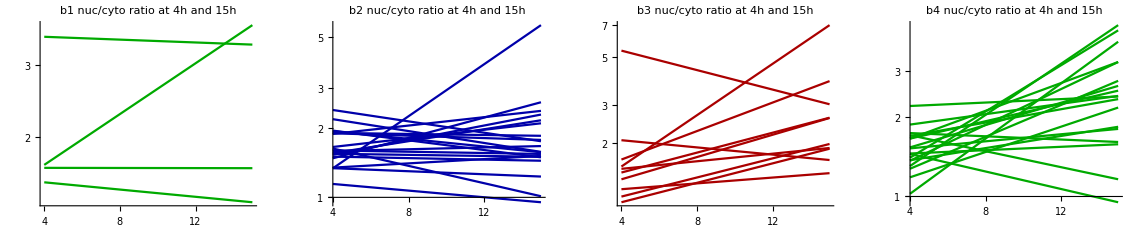

```mathematica
GraphicsRow[{  Show[plotsb1,PlotRange->{{4,15.1},{All,Log[15]}},AxesOrigin->{4,0}, PlotLabel->"b1 nuc/cyto ratio at 4h and 15h" ]  ,  Show[plotsb2,PlotRange->{{4,15.1},{All,Log[15]}},AxesOrigin->{4,0},PlotLabel->"b2 nuc/cyto ratio at 4h and 15h"]  ,
Show[plotsb3,PlotRange->{{4,15.1},{All,Log[15]}},AxesOrigin->{4,0},PlotLabel->"b3 nuc/cyto ratio at 4h and 15h"]   ,
Show[plotsb4,PlotRange->{{4,15.1},{All,Log[15]}},AxesOrigin->{4,0},PlotLabel->"b4 nuc/cyto ratio at 4h and 15h"]      }]
```

#### Plotting the background subtracted nuc/cyto ratio over time

my official guesses: 
need to myroi b2 #  25, 26, 31
b2 = TA (no tethering seen) (only use 2, 9, 13, 14*, 15, 16, 20*, 21, 22, 23, 24, 27, 29) (LOgfp use: 4, 8, 18, 19, 25, 26, 31) 
b3 = NT (no tethering seen) (Only can use #2,5,8,9, the rest dont really have any GFP)
b4 = TL

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
myRatio1 = (nucGIntb1 - bkgGIntb1)/(cytoGIntb1- bkgGIntb1)
(*Use Ratio2 to plot early vs late nuc/cyto ratio *)
```

{{1.70871,3.74777},{3.51031,3.35944},{1.68058,1.67745},{1.54942,1.38519}}

```mathematica
myRatio2 = (nucGIntb2 - bkgGIntb2)/(cytoGIntb2 - bkgGIntb2)
(*Use Ratio2 to plot early vs late nuc/cyto ratio *)
```

{{1.33841,5.63771},{1.34782,1.51605},{1.14404,0.952023},{1.48007,2.59873},{1.50543,1.44445},{2.40466,1.75683},{1.91057,1.85545},{1.89055,2.38321},{1.55904,2.16849},{1.53452,2.2966},{2.19269,1.57856},{1.90359,1.78083},{1.63332,1.01122},{1.59163,1.67374},{1.3404,1.23233},{1.94369,1.57297},{1.60133,1.5464},{1.54927,1.50309},{1.65845,2.10365},{1.95463,1.49501}}

```mathematica
myRatio3 = (nucGIntb3 - bkgGIntb3)/(cytoGIntb3 - bkgGIntb3)
(*Use Ratio2 to plot early vs late nuc/cyto ratio *)
```

{{1.1277,1.97473},{1.21987,1.4471},{1.06169,1.8772},{5.33572,3.01454},{1.51549,1.89228},{1.55315,7.00034},{1.3554,2.60421},{1.45689,2.61224},{1.67292,3.8572},{2.05553,1.6646}}

```mathematica
myRatio4 = (nucGIntb4 - bkgGIntb4)/(cytoGIntb4 - bkgGIntb4)
```

{{1.74338,1.61223},{1.40487,4.28847},{1.52449,1.80784},{1.66085,3.24904},{1.45156,0.950785},{1.53784,2.63601},{1.69963,2.34718},{1.45732,1.5803},{1.30598,4.48892},{2.21008,2.40173},{1.02389,3.88051},{1.36768,3.24967},{1.27508,2.75522},{1.71096,1.163},{1.37408,1.84184},{1.18307,2.17996},{1.87792,2.41414},{1.66052,2.52774}}

```mathematica
plotsb1= ListPlot[# , PlotMarkers -> -Graphics- ]&/@{myRatio1};
```

```mathematica
plotsb2= ListPlot[#,PlotMarkers -> -Graphics- ]&/@{myRatio2};
```

```mathematica
plotsb3= ListPlot[#,PlotMarkers ->-Graphics-  ]&/@{myRatio3};
```

```mathematica
plotsb4= ListPlot[#,PlotMarkers -> -Graphics-]&/@{myRatio4};
```

Show::gcomb: Could not combine the graphics objects in Show[xylineplot,{},PlotRange→{{0,5},{0,10}},AxesOrigin→{0,0},AspectRatio→2,PlotLabel→b1 nuc/cyto ratio at 4h and 15h].

Show::gcomb: Could not combine the graphics objects in Show[xylineplot,{},PlotRange→{{0,5},{0,10}},AxesOrigin→{0,0},AspectRatio→2,PlotLabel→b2 nuc/cyto ratio at 4h and 15h].

Show::gcomb: Could not combine the graphics objects in Show[xylineplot,{},PlotRange→{{0,5},{0,10}},AxesOrigin→{0,0},AspectRatio→2,PlotLabel→b3 nuc/cyto ratio at 4h and 15h].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

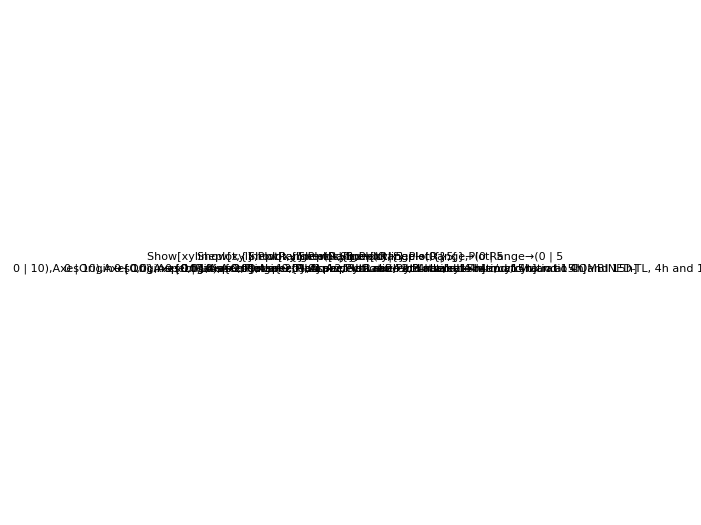

```mathematica
GraphicsRow[{  
Show[xylineplot, plotsb1,PlotRange->{{0,5},{0,10}},AxesOrigin->{0,0}, AspectRatio->2, PlotLabel->"b1 nuc/cyto ratio at 4h and 15h" ]  ,  Show[xylineplot, plotsb2,PlotRange->{{0,5},{0,10}},AxesOrigin->{0,0}, AspectRatio->2, PlotLabel->"b2 nuc/cyto ratio at 4h and 15h"]  ,
Show[xylineplot, plotsb3,PlotRange->{{0,5},{0,10}},AxesOrigin->{0,0}, AspectRatio->2, PlotLabel->"b3 nuc/cyto ratio at 4h and 15h"]   ,
Show[xylineplot, plotsb4,PlotRange->{{0,5},{0,10}},AxesOrigin->{0,0}, AspectRatio->2, PlotLabel->"b4 nuc/cyto ratio at 4h and 15h"]   ,
Show[xylineplot, plotsb4, plotsb1,PlotRange->{{0,5},{0,10}},AxesOrigin->{0,0}, AspectRatio->2, PlotLabel->"b4 nuc/cyto ratio COMBINED-TL, 4h and 15h"]   
}]
```

Show::gcomb: Could not combine the graphics objects in ….

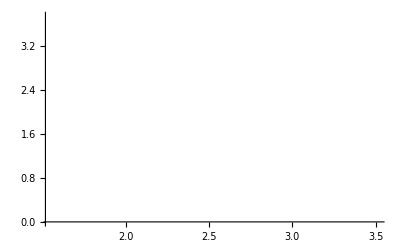
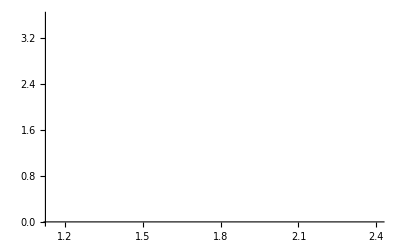
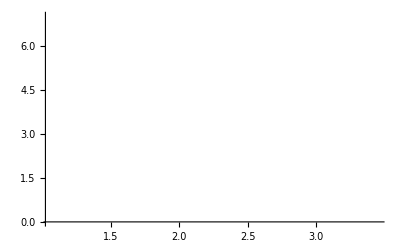
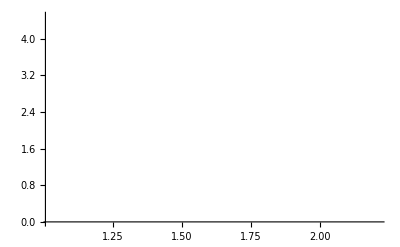
Show[{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},xylineplot},PlotRange→{{0,5},{0,10}},AxesOrigin→{0,0},AspectRatio→2,PlotLabel→b1 nuc/cyto ratio at 4h and 15h]

```mathematica
Show[{ plotsb1,plotsb2,plotsb3, plotsb4,xylineplot} ,  PlotRange->{{0,5},{0,10}},AxesOrigin->{0,0}, AspectRatio->2, PlotLabel->"b1 nuc/cyto ratio at 4h and 15h"  ]
```

#### Plotting the background subtracted nuc/cyto ratio over time: Ratio 15h/4h box/whisk

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
ratios0125 = {  Table[myRatio3[[cell,2]] / myRatio3[[cell,1]], {cell, 1, Length@myRatio3}] ,
Table[myRatio4[[cell,2]] / myRatio4[[cell,1]], {cell, 1, Length@myRatio4}] ,
Table[myRatio2[[cell,2]] / myRatio2[[cell,1]], {cell, 1, Length@myRatio2}] } ; 
(*Use Ratio2 to plot early vs late nuc/cyto ratio *)
a = ratios0125
```

{{1.75112,1.18627,1.76812,0.564973,1.24863,4.50718,1.92137,1.79303,2.30567,0.809814},{0.924771,3.05257,1.18586,1.95625,0.655007,1.7141,1.381,1.08439,3.43721,1.08672,3.78996,2.37605,2.16082,0.679731,1.34041,1.84262,1.28554,1.52226},{4.21226,1.12482,0.832158,1.75581,0.959496,0.730592,0.97115,1.26059,1.39091,1.49663,0.71992,0.935512,0.619119,1.05159,0.919375,0.809271,0.965697,0.970193,1.26845,0.764856}}

```mathematica
WMWtestNTTAvTLTAvNTTL0125 = { MannWhitneyTest[ {a[[1]],a[[3]] }], MannWhitneyTest[ {a[[2]],a[[3]] }], MannWhitneyTest[ {a[[1]],a[[2]] }] }
```

{0.0366428,0.0114437,0.942666}

```mathematica
{{-Graphics-,0.015},{-Graphics-,0.015},{-Graphics-,0.015}}
```

{{-Graphics-,0.015},{-Graphics-,0.015},{-Graphics-,0.015}}

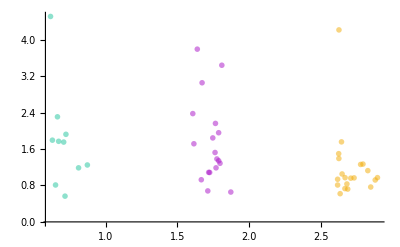

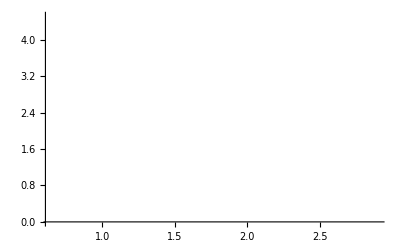

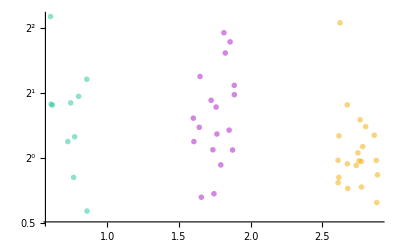

```mathematica
b = ListPlot[Table[ Thread[{Table[RandomReal[ {n-l,n-m} ], Length[a[[n]] ] ], a[[n]] }], {n,1,Length@a}] ,PlotMarkers-> {{-Graphics-,.01},{-Graphics-,.01},{-Graphics-,0.01}} ]
b0125points = b;
b = ListPlot[Table[ Thread[{Table[RandomReal[ {n-l,n-m} ], Length[a[[n]] ] ], a[[n]] }], {n,1,Length@a}] , PlotMarkers-> {-Graphics-,-Graphics-,-Graphics-}]
b0125 = b;
b = ListPlot[Table[ Thread[{Table[RandomReal[ {n-l,n-m} ], Length[a[[n]] ] ], a[[n]] }], {n,1,Length@a}] , PlotMarkers-> {{-Graphics-,mypointsize},{-Graphics-,mypointsize},{-Graphics-,mypointsize}},  ScalingFunctions->"Log2"]
b0125pointslog = b;
```

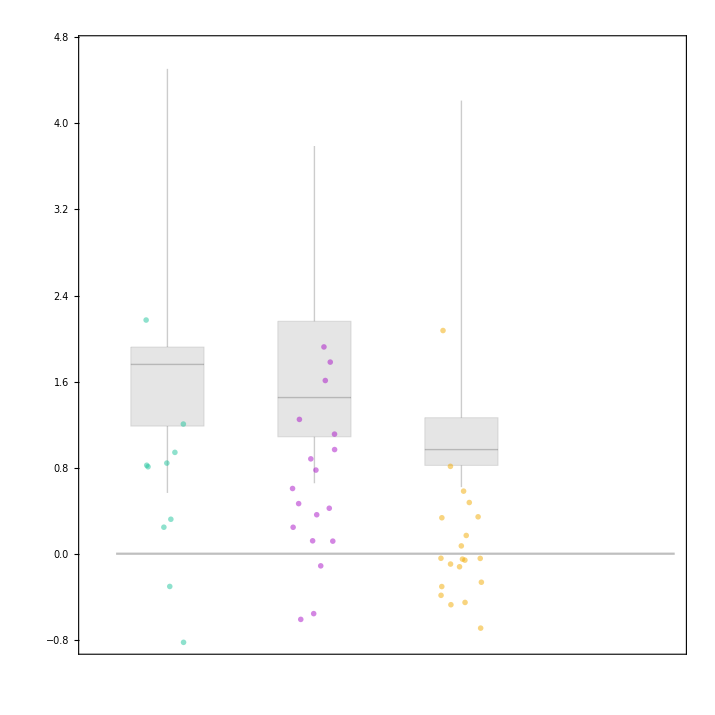

```mathematica
myBoxWhiskerPlot0125 = Show[  BoxWhiskerChart[a,{{"MedianMarker",Thick},{"Whiskers",Thick},{"Fences",1,Opacity[0]}} ,ChartStyle->{{EdgeForm[{Gray, Thickness[Large]}  ]} , {Opacity[0.2,Gray]} } , AspectRatio->1  ] ,b,  Plot[x=0,{x,0.4,4.2}, PlotStyle->Opacity[0.5,Gray] ], AspectRatio -> 1]
```

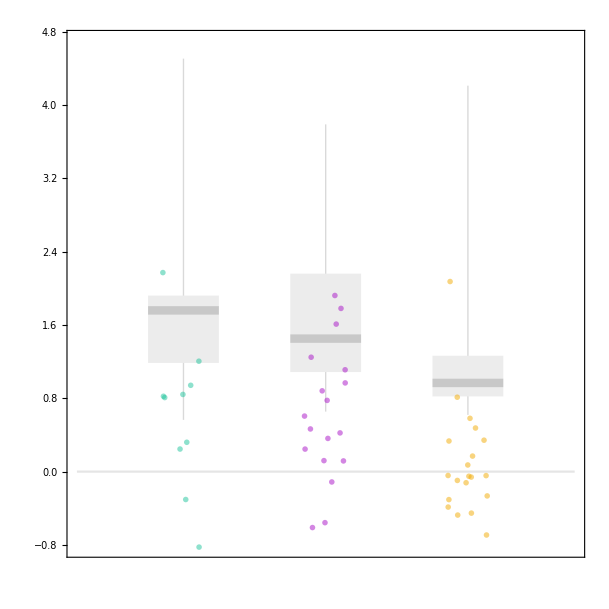

```mathematica
myBoxWhiskerPlot0125= Show[  BoxWhiskerChart[a , {{"MedianMarker",Thickness[.01]},{"Whiskers",Thick},{"Fences",1,Opacity[0]}},ChartBaseStyle-> Directive[ Opacity[0.15,Gray]  ]     , AspectRatio->1  ] ,b,  Plot[x=0,{x,0,3.5}, PlotStyle->Opacity[0.2,Gray] ], AspectRatio -> 1]
```

```mathematica
StandardDeviation/@a
```

{1.09479,0.911242,0.766825}

```mathematica
(* Bar chart not used 
b = ListPlot[Table[ Thread[{Table[RandomReal[ {n-.3,n + .3} ], Length[a[[n]] ] ], a[[n]] }], {n,1,Length@a}], PlotMarkers-> {-Graphics-,-Graphics-,-Graphics-} ]
```

```mathematica
(* Bar chart not used 
myChart0125 = Show[ BarChart[Mean/@a, ChartStyle->{{EdgeForm[Thickness[Large]]}, {Opacity[0,Gray]}} , AspectRatio->1] ,b]
```

#### Remake B&W plot

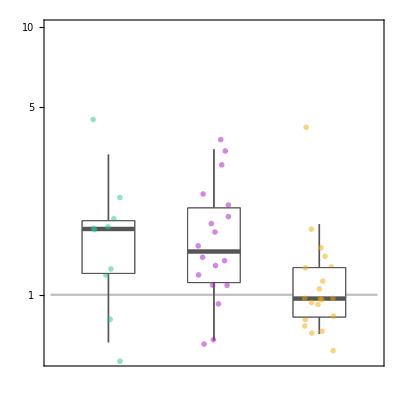

```mathematica
bwchart = BoxWhiskerChart[a,{ {"MedianMarker",Directive[Thickness[.008],Darker[Gray]]},{"Whiskers",Directive[Thick,Darker[Gray]]},{"Fences",1,Opacity[0]}} ,ChartStyle->{{EdgeForm[{Darker[Gray], Thickness[Large]}  ]} , {White} } , AspectRatio->1 ,ScalingFunctions->"Log2" ,{Method->{"BoxRange"->(Quantile[#,{.05,.25,.5,.75,.95},{{1,-1},{0,1}}]&)}}];
myBoxWhiskerPlot0125wctrl =  
Show[   bwchart,  Plot[x=0,{x,0.2,3.3}, PlotStyle->Opacity[0.5,Gray]],bwchart,b, AspectRatio -> 1,BaseStyle->{FontFamily->"Arial",FontSize->22},PlotRange-> {-.8,Log2[10]}]
```

#### Find out how many cells have positive accumulation AND, change magnitude of positive accumulation in order to count, such as accumulation greater than 0.5 to count...

Find the fraction of cells that are above 0, which means they have a positive gain in accumulation.....  {NT, TL, TA}

```mathematica
z=1;
 {  
Length@Cases[  a[[1]] , n_/; n>z] / Length@a[[1]]  //N , 
Length@Cases[  a[[2]] , n_/; n>z] / Length@a[[2]]  //N , 
Length@Cases[  a[[3]] , n_/; n>z]/ Length@a[[3]]  //N 
 }
```

{0.8,0.833333,0.4}

Find the fraction of cells that are above 0 BY A CERTAIN AMOUNT , which means they have a positive gain in accumulation ABOVE A CERTAIN AMOUNT.....  {NT, TL, TA}

```mathematica
zs = Table[z,{z,1,2, 0.1}]
```

{1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.}

```mathematica
atable = Table [ 
{Length@Cases[  a[[1]] , n_/; n>z] / Length@a[[1]]  //N , 
Length@Cases[  a[[2]] , n_/; n>z] / Length@a[[2]]  //N , 
Length@Cases[  a[[3]] , n_/; n>z]/ Length@a[[3]]  //N  } ,
{z,1,2, 0.1}] ;
atable// TableForm
```

0.8 | 0.833333 | 0.4
0.8 | 0.722222 | 0.35
0.7 | 0.666667 | 0.3
0.6 | 0.611111 | 0.2
0.6 | 0.5 | 0.15
0.6 | 0.5 | 0.1
0.6 | 0.444444 | 0.1
0.6 | 0.444444 | 0.1
0.3 | 0.388889 | 0.05
0.3 | 0.333333 | 0.05
0.2 | 0.277778 | 0.05

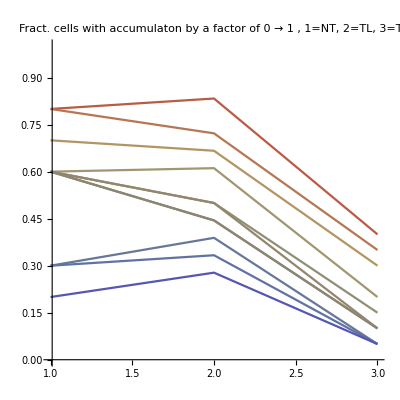

```mathematica
ListLinePlot[#,ColorFunction->"Rainbow" , PlotRange -> {{1,3},{0,1}} , AspectRatio->1,
 PlotLabel -> "Fract. cells with accumulaton by a factor of 0 → 1 , 1=NT, 2=TL, 3=TA"  ]&/@{atable}
```

### 02-08-2019: Show change in nuc/cyto signal, background subtracted, all cells -RNA -DNA control!

NO DNA/RNA CONTROL! 
AGO dna was BL into cells, but no reporter RNA.

#### Import

```mathematica
analysisFolderctrl="/Volumes/BITTY/_long_timeframe_transient_mini/20190208_noRNA_TA_15h/4h_15h_only//Analysis/"
```

/Volumes/BITTY/_long_timeframe_transient_mini/20190208_noRNA_TA_15h/4h_15h_only//Analysis/

```mathematica
FileNames[analysisFolderctrl <>"/*ROI.dat"]//Length
```

35

```mathematica
filesctrl = FileNames[analysisFolderctrl <> "*noDNA*ROI.dat"];
```

```mathematica
countsctrl = Length@filesctrl
```

35

```mathematica
mymaskfilesctrl  = Table[<<(filesctrl[[i]]),{i,1,Length@filesctrl,1}]; 
Length/@mymaskfilesctrl
bkgGIntctrl =mymaskfilesctrl[[All,1,1;;2,3,2]];
cytoGIntctrl =mymaskfilesctrl[[All,2,1;;2,3,2]];
nucGIntctrl =mymaskfilesctrl[[All,3,1;;2,3,2]];
```

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
(*  myRatio = (nucGInt-bkgGInt)/(cytoGInt-bkgGInt)
```

```mathematica
myRatioTimectrl = {(nucGIntctrl-bkgGIntctrl)/(cytoGIntctrl-bkgGIntctrl)} //  Table[   Transpose[ {{4,15}, # [[1,i]]}  ],{i,1,Length@nucGIntctrl}]& ;
```

#### Plotting the background subtracted nuc/cyto ratio over time

```mathematica
plotsctrl= ListLinePlot[#,PlotStyle->{Darker[Gray]}, ScalingFunctions->"Log"]&/@myRatioTimectrl;
```

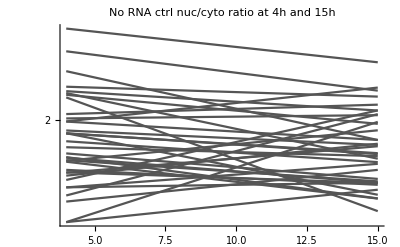

```mathematica
Show[plotsctrl,PlotRange->{{4,15.1},{All,Log[15]}},AxesOrigin->{4,0}, PlotLabel->"No RNA ctrl nuc/cyto ratio at 4h and 15h" ]
```

#### Plotting the background subtracted nuc/cyto ratio over time

-Graphics-

```mathematica
myRatioctrl = {(nucGIntctrl-bkgGIntctrl)/(cytoGIntctrl-bkgGIntctrl)}
```

{{{1.75231,1.55993},{2.17607,1.76902},{1.69493,1.63905},{1.67698,1.85463},{2.1891,2.05962},{1.79882,1.65972},{1.61621,1.6399},{2.0087,2.02951},{1.98887,1.87682},{1.44818,1.60408},{1.91684,1.79489},{1.65429,2.06026},{1.77788,1.56076},{1.61569,1.74054},{1.98975,2.21406},{2.48258,2.19292},{2.16409,1.97485},{1.93379,1.84757},{2.33172,1.87638},{2.66717,2.39798},{1.70778,1.62928},{1.5752,2.03631},{1.69219,1.83999},{1.91719,1.57872},{1.75736,1.93482},{1.86919,1.75004},{1.54515,1.70777},{2.14639,1.49925},{1.77462,1.63959},{1.76063,1.64693},{1.83434,1.78341},{1.91532,1.80006},{1.44817,1.98692},{2.03658,2.09789},{2.22013,2.15193}}}

```mathematica
plotsctrl= ListPlot[# , PlotMarkers -> -Graphics- ]&/@{myRatioctrl};
```

Show::gcomb: Could not combine the graphics objects in Show[xylineplot,{},PlotRange→{{0,5},{0,10}},AxesOrigin→{0,0},AspectRatio→2,PlotLabel→b1 nuc/cyto ratio at 4h and 15h].

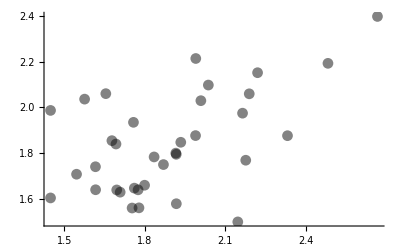
Show[xylineplot,{-Graphics-},PlotRange→{{0,5},{0,10}},AxesOrigin→{0,0},AspectRatio→2,PlotLabel→b1 nuc/cyto ratio at 4h and 15h]

```mathematica
Show[xylineplot, plotsctrl,PlotRange->{{0,5},{0,10}},AxesOrigin->{0,0}, AspectRatio->2, PlotLabel->"b1 nuc/cyto ratio at 4h and 15h" ]
```

#### Plotting the background subtracted nuc/cyto ratio over time: Ratio 15h/4h box/whisk

-Graphics-

```mathematica
myRatioctrl
```

{{{1.75231,1.55993},{2.17607,1.76902},{1.69493,1.63905},{1.67698,1.85463},{2.1891,2.05962},{1.79882,1.65972},{1.61621,1.6399},{2.0087,2.02951},{1.98887,1.87682},{1.44818,1.60408},{1.91684,1.79489},{1.65429,2.06026},{1.77788,1.56076},{1.61569,1.74054},{1.98975,2.21406},{2.48258,2.19292},{2.16409,1.97485},{1.93379,1.84757},{2.33172,1.87638},{2.66717,2.39798},{1.70778,1.62928},{1.5752,2.03631},{1.69219,1.83999},{1.91719,1.57872},{1.75736,1.93482},{1.86919,1.75004},{1.54515,1.70777},{2.14639,1.49925},{1.77462,1.63959},{1.76063,1.64693},{1.83434,1.78341},{1.91532,1.80006},{1.44817,1.98692},{2.03658,2.09789},{2.22013,2.15193}}}

```mathematica
ratiosctrl = Table[myRatioctrl[[1,cell,2]] / myRatioctrl[[1,cell,1]], {cell, 1, Length@myRatioctrl[[1]]}] ;
(*Use Ratio2 to plot early vs late nuc/cyto ratio *)
a = ratiosctrl
```

{0.890218,0.812945,0.967029,1.10593,0.940853,0.922675,1.01466,1.01036,0.943664,1.10765,0.936379,1.2454,0.877875,1.07727,1.11273,0.883324,0.912553,0.955412,0.804718,0.899075,0.954032,1.29273,1.08734,0.823457,1.10098,0.936256,1.10525,0.698497,0.923906,0.935422,0.972235,0.939821,1.37203,1.0301,0.969279}

```mathematica
(*
WMWtestNTTAvTLTAvNTTL0125 = { MannWhitneyTest[ {a[[1]],a[[3]] }], MannWhitneyTest[ {a[[2]],a[[3]] }], MannWhitneyTest[ {a[[1]],a[[2]] }] }
*)
```

```mathematica
n=1;
```

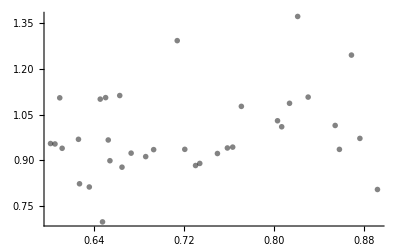

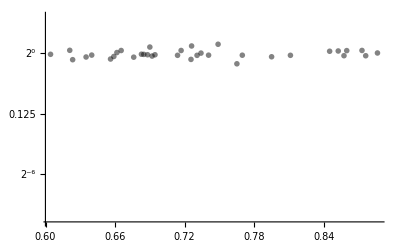

```mathematica
b = ListPlot[ Thread[{Table[RandomReal[ {n-l,n-m} ], Length[a ] ], a }] , PlotMarkers->{-Graphics-,.01}]
bctrlpoints = b;
b = ListPlot[ Thread[{Table[RandomReal[ {n-l,n-m} ], Length[a ] ], a }] , PlotMarkers->{-Graphics-,mypointsize},  ScalingFunctions->"Log2",PlotRange-> {-1,Log2[12]}]
bctrlpointslog = b;
```

```mathematica
a = Join[{ratiosctrl},ratios1025[[1;;2]] ]; 
ctrl3DataSets = a;
Dimensions/@a
```

{{35},{19},{35}}

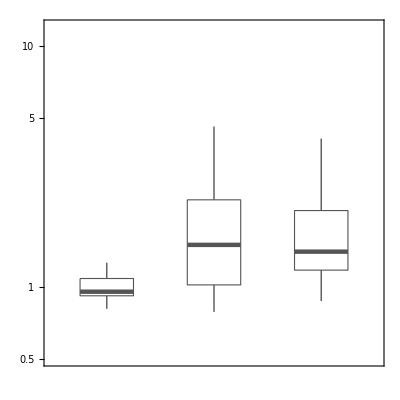

```mathematica
bwchart = BoxWhiskerChart[a,{ {"MedianMarker",Directive[Thickness[.008],Darker[Gray]]},{"Whiskers",Directive[Thick,Darker[Gray]]},{"Fences",1,Opacity[0]}} ,ChartStyle->{{EdgeForm[{Darker[Gray], Thickness[Large]}  ]} , {White} } , AspectRatio->1 ,ScalingFunctions->"Log2" ,{Method->{"BoxRange"->(Quantile[#,{.05,.25,.5,.75,.95},{{1,-1},{0,1}}]&)}},  PlotRange-> {-1,Log2[12]}]
```

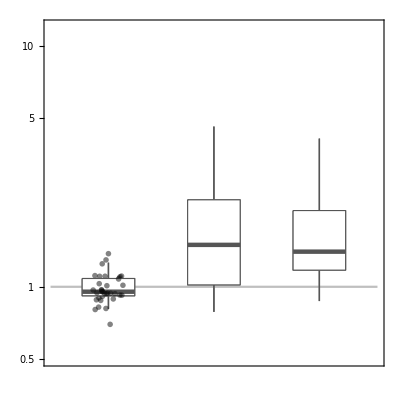

```mathematica
myBoxWhiskerPlotallwctrl =  
Show[   bwchart,  Plot[x=0,{x,0.2,3.3}, PlotStyle->Opacity[0.5,Gray]],bwchart,b, AspectRatio -> 1,BaseStyle->{FontFamily->"Arial",FontSize->18},PlotRange-> {-1,Log2[12]}]
```

```mathematica
(*myBoxWhiskerPlotctrl = Show[ b, BoxWhiskerChart[a,{{"MedianMarker",Thick},{"Whiskers",Thick},{"Fences",1,Opacity[0]}} ,ChartStyle->{{EdgeForm[{Gray, Thickness[Large]}  ]} ,{Opacity[0.2,Gray]} } ,AspectRatio->1  ] ,  b,Plot[x=0,{x,0,2}, PlotStyle->Opacity[0.5,Gray] ], PlotRange->All]
```

```mathematica
(*myBoxWhiskerPlotFabOnly= Show[b,  BoxWhiskerChart[a , {{"MedianMarker",Thickness[.01]},{"Whiskers",Thick},{"Fences",1,Opacity[0]}},ChartBaseStyle-> Directive[ Opacity[0.15,Gray]  ] , AspectRatio->1,ScalingFunctions->"Log2"   ] ,  Plot[x=1,{x,0,1}, PlotStyle->Opacity[0.15,Black] ], PlotRange-> {-1,Log2[12]}]
```

```mathematica
StandardDeviation@a
```

StandardDeviation::rectt: Rectangular array expected at position 1 in StandardDeviation[{{0.890218,0.812945,0.967029,1.10593,0.940853,0.922675,1.01466,1.01036,0.943664,1.10765,0.936379,1.2454,0.877875,1.07727,1.11273,0.883324,0.912553,0.955412,0.804718,0.899075,0.954032,1.29273,1.08734,0.823457,1.10098,0.936256,1.10525,0.698497,0.923906,0.935422,0.972235,0.939821,1.37203,1.0301,0.969279},{«19»,«17»,«18»},{1.09289,2.11415,1.23058,0.91301,«27»,1.94487,2.19827,4.73419,2.29321}}].

StandardDeviation[{{0.890218,0.812945,0.967029,1.10593,0.940853,0.922675,1.01466,1.01036,0.943664,1.10765,0.936379,1.2454,0.877875,1.07727,1.11273,0.883324,0.912553,0.955412,0.804718,0.899075,0.954032,1.29273,1.08734,0.823457,1.10098,0.936256,1.10525,0.698497,0.923906,0.935422,0.972235,0.939821,1.37203,1.0301,0.969279},{1.1172,2.52694,1.27444,0.890132,3.09445,6.43303,0.690295,2.08406,1.53387,4.45543,1.80799,1.49251,1.07945,1.96522,0.809877,0.798489,0.960463,3.07665,1.22241},{1.09289,2.11415,1.23058,0.91301,1.11453,2.02932,3.71232,1.24335,1.50444,2.15697,0.900941,0.818726,0.738385,3.98334,1.27368,1.27438,1.32839,1.12745,1.39871,1.01116,1.37627,1.3334,1.40606,1.8287,4.45667,1.65448,1.52306,1.2192,2.69616,1.49691,0.896675,1.94487,2.19827,4.73419,2.29321}}]

#### Find out how many cells have positive accumulation AND, change magnitude of positive accumulation in order to count, such as accumulation greater than 0.5 to count...

Find the fraction of cells that are above 0, which means they have a positive gain in accumulation.....  {NT, TL, TA}

```mathematica
a
```

{{0.890218,0.812945,0.967029,1.10593,0.940853,0.922675,1.01466,1.01036,0.943664,1.10765,0.936379,1.2454,0.877875,1.07727,1.11273,0.883324,0.912553,0.955412,0.804718,0.899075,0.954032,1.29273,1.08734,0.823457,1.10098,0.936256,1.10525,0.698497,0.923906,0.935422,0.972235,0.939821,1.37203,1.0301,0.969279},{1.1172,2.52694,1.27444,0.890132,3.09445,6.43303,0.690295,2.08406,1.53387,4.45543,1.80799,1.49251,1.07945,1.96522,0.809877,0.798489,0.960463,3.07665,1.22241},{1.09289,2.11415,1.23058,0.91301,1.11453,2.02932,3.71232,1.24335,1.50444,2.15697,0.900941,0.818726,0.738385,3.98334,1.27368,1.27438,1.32839,1.12745,1.39871,1.01116,1.37627,1.3334,1.40606,1.8287,4.45667,1.65448,1.52306,1.2192,2.69616,1.49691,0.896675,1.94487,2.19827,4.73419,2.29321}}

```mathematica
z=1;
 {  Length@Cases[  a , n_/; n>z] / Length@a[[1]]  //N   }
```

{0.}

Find the fraction of cells that are above 0 BY A CERTAIN AMOUNT , which means they have a positive gain in accumulation ABOVE A CERTAIN AMOUNT.....  {NT, TL, TA}

```mathematica
zs = Table[z,{z,1,2, 0.1}]
```

{1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.}

```mathematica
atable = Table [ 
Length@Cases[  a[[1]] , n_/; n>z] / Length@a[[1]]  //N  ,
{z,1,2, 0.1}] ;
atable// TableForm
```

0.371429
0.228571
0.0857143
0.0285714
0.
0.
0.
0.
0.
0.
0.

```mathematica
ListLinePlot[#,ColorFunction->"Rainbow" , PlotRange -> {{1,3},{0,1}} , AspectRatio->1,
 PlotLabel -> "Fract. cells with accumulaton by a factor of 0 → 1 , 1=NT, 2=TL, 3=TA"  ]&/@{atable}
```

{-Graphics-}

## Combine multiple days of data Each day of data has a different shape of plot marker

#### UNDER DEV: Not finished yet Stdevs

```mathematica
Needs["ErrorBarPlots`"]
```

ErrorBar::shdw: Symbol ErrorBar appears in multiple contexts {ErrorBarPlots`,Global`}; definitions in context ErrorBarPlots` may shadow or be shadowed by other definitions.

ErrorListPlot::shdw: Symbol ErrorListPlot appears in multiple contexts {ErrorBarPlots`,Global`}; definitions in context ErrorBarPlots` may shadow or be shadowed by other definitions.

```mathematica
means = Mean/@#&/@{myRatioNT1203, myRatioTL1203, myRatioTA1203,  myRatioNT1025, myRatioTL1025, myRatioTA1025, { myRatio1},{myRatio2}, {myRatio3}} //Flatten[#,1]& // Partition[#,3]&
stdevs = StandardDeviation/@#&/@{myRatioNT1203, myRatioTL1203, myRatioTA1203,  myRatioNT1025, myRatioTL1025, myRatioTA1025, { myRatio1},{myRatio2}, {myRatio3}} //Flatten[#,1]&// Partition[#,3]&
```

{{2.26138,2.2837,2.09503},{1.63086,1.92658,2.09188},{2.0289,1.6861,2.70274},{1.88048,1.7958,1.39034},{4.52212,4.26955,2.13104},{1.88114,1.71353,1.75261},{5.23712,1.98584,1.7168},{5.088,2.65478,2.29021},{2.0254,1.88092,1.91016},{1.76079,1.64216,2.07494},{1.50161,1.84577,1.72154},{1.60307,1.54023,1.63519},{1.24746,1.65943,2.03279},{1.8914,1.58677,1.67086},{2.30694,1.22627,1.2748},{1.85197,1.77173,2.09565},{2.40843,1.71061,2.5759},{1.92259,1.34894,1.66577},{1.41052,1.84604,1.36175},{1.5616,1.23202,1.82853},{2.44466,2.20607,2.09147},{2.0682,1.77099,1.58658},{1.5458,2.02303,2.07734},{1.70246,2.36565,6.45642},{1.80341,2.67147,1.71863},{2.91672,1.72146,1.60151},{1.18582,2.05787,1.48734},{1.2826,1.82094,3.44867},{1.43008,2.32623,2.05319},{1.82328,1.24213,1.73297},{1.71688,3.23394,1.13833},{2.40759,2.6767,2.20794},{1.4988,1.50424,2.7076},{1.60576,1.55692,1.72634},{1.67463,1.85183,1.78022},{1.61592,1.82954,2.12502},{2.69843,2.89406,1.92366},{2.06741,1.70207,2.28144},{2.23312,1.76333,1.8547},{1.93458,4.67607,2.28628},{1.60323,3.96024,1.61195},{1.24631,1.48364,1.58074},{1.60649,1.6507,1.76126},{1.58022,1.83496,1.59836},{1.76957,1.22794,1.69229},{1.4296,1.50576,{2.11226,2.54246}}}

{{0.408172,0.50916,0.171015},{0.903308,0.65464,0.0837603},{0.0611891,0.204291,1.5522},{0.925108,0.225528,0.139209},{2.97233,2.95065,1.05514},{0.0382868,0.184093,0.154551},{5.88383,0.629935,0.140127},{5.51736,1.28692,1.15271},{0.0995979,0.0644654,0.469904},{0.0381919,0.226968,0.125641},{0.324864,0.176632,0.0997863},{0.160783,0.599212,0.321165},{0.0187915,0.655671,0.143121},{0.0922611,0.213494,0.161578},{0.395784,0.201072,0.144808},{0.514033,0.0827723,1.54336},{1.18064,0.0674594,0.211572},{0.123169,0.558459,0.172823},{0.329748,0.17219,0.16666},{0.473321,0.294797,0.817847},{0.244335,0.214697,0.760335},{0.429261,0.0705709,0.186305},{0.121009,1.23863,0.354481},{0.13995,1.71135,6.67395},{0.4673,1.32799,0.512092},{2.61266,0.700522,0.447533},{0.064071,0.947336,0.220959},{0.203235,0.0519338,2.48443},{0.202402,0.146009,1.03884},{0.266544,0.0798793,0.132741},{0.825011,2.63241,0.174632},{0.6858,1.38728,0.162715},{0.211266,0.320146,2.29236},{0.273347,0.265623,0.344332},{0.14188,0.435305,0.0139733},{0.361856,0.369689,0.507181},{1.11798,2.59271,0.670746},{0.606133,0.237758,1.48061},{0.628496,0.13585,0.841577},{1.02504,4.30646,1.26968},{0.791794,3.62545,0.110781},{0.177964,0.55007,0.103526},{0.13367,0.68041,0.810408},{0.14361,0.778541,0.033285},{0.149493,0.137219,0.399441},{0.168007,0.156179,{0.934618,1.18431}}}

```mathematica
error = ErrorBar/@   #&/@  stdevs // Flatten[#,1]&// Partition[#,3]&
```

{{ErrorBar[0.408172],ErrorBar[0.50916],ErrorBar[0.171015]},{ErrorBar[0.903308],ErrorBar[0.65464],ErrorBar[0.0837603]},{ErrorBar[0.0611891],ErrorBar[0.204291],ErrorBar[1.5522]},{ErrorBar[0.925108],ErrorBar[0.225528],ErrorBar[0.139209]},{ErrorBar[2.97233],ErrorBar[2.95065],ErrorBar[1.05514]},{ErrorBar[0.0382868],ErrorBar[0.184093],ErrorBar[0.154551]},{ErrorBar[5.88383],ErrorBar[0.629935],ErrorBar[0.140127]},{ErrorBar[5.51736],ErrorBar[1.28692],ErrorBar[1.15271]},{ErrorBar[0.0995979],ErrorBar[0.0644654],ErrorBar[0.469904]},{ErrorBar[0.0381919],ErrorBar[0.226968],ErrorBar[0.125641]},{ErrorBar[0.324864],ErrorBar[0.176632],ErrorBar[0.0997863]},{ErrorBar[0.160783],ErrorBar[0.599212],ErrorBar[0.321165]},{ErrorBar[0.0187915],ErrorBar[0.655671],ErrorBar[0.143121]},{ErrorBar[0.0922611],ErrorBar[0.213494],ErrorBar[0.161578]},{ErrorBar[0.395784],ErrorBar[0.201072],ErrorBar[0.144808]},{ErrorBar[0.514033],ErrorBar[0.0827723],ErrorBar[1.54336]},{ErrorBar[1.18064],ErrorBar[0.0674594],ErrorBar[0.211572]},{ErrorBar[0.123169],ErrorBar[0.558459],ErrorBar[0.172823]},{ErrorBar[0.329748],ErrorBar[0.17219],ErrorBar[0.16666]},{ErrorBar[0.473321],ErrorBar[0.294797],ErrorBar[0.817847]},{ErrorBar[0.244335],ErrorBar[0.214697],ErrorBar[0.760335]},{ErrorBar[0.429261],ErrorBar[0.0705709],ErrorBar[0.186305]},{ErrorBar[0.121009],ErrorBar[1.23863],ErrorBar[0.354481]},{ErrorBar[0.13995],ErrorBar[1.71135],ErrorBar[6.67395]},{ErrorBar[0.4673],ErrorBar[1.32799],ErrorBar[0.512092]},{ErrorBar[2.61266],ErrorBar[0.700522],ErrorBar[0.447533]},{ErrorBar[0.064071],ErrorBar[0.947336],ErrorBar[0.220959]},{ErrorBar[0.203235],ErrorBar[0.0519338],ErrorBar[2.48443]},{ErrorBar[0.202402],ErrorBar[0.146009],ErrorBar[1.03884]},{ErrorBar[0.266544],ErrorBar[0.0798793],ErrorBar[0.132741]},{ErrorBar[0.825011],ErrorBar[2.63241],ErrorBar[0.174632]},{ErrorBar[0.6858],ErrorBar[1.38728],ErrorBar[0.162715]},{ErrorBar[0.211266],ErrorBar[0.320146],ErrorBar[2.29236]},{ErrorBar[0.273347],ErrorBar[0.265623],ErrorBar[0.344332]},{ErrorBar[0.14188],ErrorBar[0.435305],ErrorBar[0.0139733]},{ErrorBar[0.361856],ErrorBar[0.369689],ErrorBar[0.507181]},{ErrorBar[1.11798],ErrorBar[2.59271],ErrorBar[0.670746]},{ErrorBar[0.606133],ErrorBar[0.237758],ErrorBar[1.48061]},{ErrorBar[0.628496],ErrorBar[0.13585],ErrorBar[0.841577]},{ErrorBar[1.02504],ErrorBar[4.30646],ErrorBar[1.26968]},{ErrorBar[0.791794],ErrorBar[3.62545],ErrorBar[0.110781]},{ErrorBar[0.177964],ErrorBar[0.55007],ErrorBar[0.103526]},{ErrorBar[0.13367],ErrorBar[0.68041],ErrorBar[0.810408]},{ErrorBar[0.14361],ErrorBar[0.778541],ErrorBar[0.033285]},{ErrorBar[0.149493],ErrorBar[0.137219],ErrorBar[0.399441]},{ErrorBar[0.168007],ErrorBar[0.156179],ErrorBar[{0.934618,1.18431}]}}

```mathematica
error = {{ErrorBar[0.3776617031489534,2.353616066942905],ErrorBar[0.3136152008257244,0.5549375926995285],ErrorBar[0.39607427239079734,0.641964333944155]},{ErrorBar[{0.3035596719031554,2.3254651764790255}],ErrorBar[{0.34446564699115195,1.5309823326955094}],ErrorBar[{0.23640668948350604,1.2182830539347629}]},{ErrorBar[{0.3880538790562896,0.5498820645551249}],ErrorBar[{0.2875024399256992,1.5322343516728207}],ErrorBar[{0.29249911560184527,0.4332776978694733}]}}
```

{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}

```mathematica
i=1; { means[[i]],error[[i]] }
```

{{2.26138,2.2837,2.09503},{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]}}

```mathematica
errorlist = Table [Transpose[ { means[[i]],error[[i]] }], {i,1,Length@means}] (*wrong*)
```

Part::partw: Part 4 of {{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}} does not exist.

Transpose::nmtx: The first two levels of {{1.88048,1.7958,1.39034},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦4⟧} cannot be transposed.

Part::partw: Part 5 of {{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}} does not exist.

Transpose::nmtx: The first two levels of {{4.52212,4.26955,2.13104},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦5⟧} cannot be transposed.

Part::partw: Part 6 of {{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{1.88114,1.71353,1.75261},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦6⟧} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

{{{2.26138,ErrorBar[0.377662,2.35362]},{2.2837,ErrorBar[0.313615,0.554938]},{2.09503,ErrorBar[0.396074,0.641964]}},{{1.63086,ErrorBar[{0.30356,2.32547}]},{1.92658,ErrorBar[{0.344466,1.53098}]},{2.09188,ErrorBar[{0.236407,1.21828}]}},{{2.0289,ErrorBar[{0.388054,0.549882}]},{1.6861,ErrorBar[{0.287502,1.53223}]},{2.70274,ErrorBar[{0.292499,0.433278}]}},Transpose[{{1.88048,1.7958,1.39034},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦4⟧}],Transpose[{{4.52212,4.26955,2.13104},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦5⟧}],Transpose[{{1.88114,1.71353,1.75261},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦6⟧}],Transpose[{{5.23712,1.98584,1.7168},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦7⟧}],Transpose[{{5.088,2.65478,2.29021},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦8⟧}],Transpose[{{2.0254,1.88092,1.91016},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦9⟧}],Transpose[{{1.76079,1.64216,2.07494},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦10⟧}],Transpose[{{1.50161,1.84577,1.72154},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦11⟧}],Transpose[{{1.60307,1.54023,1.63519},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦12⟧}],Transpose[{{1.24746,1.65943,2.03279},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦13⟧}],Transpose[{{1.8914,1.58677,1.67086},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦14⟧}],Transpose[{{2.30694,1.22627,1.2748},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦15⟧}],Transpose[{{1.85197,1.77173,2.09565},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦16⟧}],Transpose[{{2.40843,1.71061,2.5759},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦17⟧}],Transpose[{{1.92259,1.34894,1.66577},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦18⟧}],Transpose[{{1.41052,1.84604,1.36175},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦19⟧}],Transpose[{{1.5616,1.23202,1.82853},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦20⟧}],Transpose[{{2.44466,2.20607,2.09147},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦21⟧}],Transpose[{{2.0682,1.77099,1.58658},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦22⟧}],Transpose[{{1.5458,2.02303,2.07734},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦23⟧}],Transpose[{{1.70246,2.36565,6.45642},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦24⟧}],Transpose[{{1.80341,2.67147,1.71863},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦25⟧}],Transpose[{{2.91672,1.72146,1.60151},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦26⟧}],Transpose[{{1.18582,2.05787,1.48734},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦27⟧}],Transpose[{{1.2826,1.82094,3.44867},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦28⟧}],Transpose[{{1.43008,2.32623,2.05319},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦29⟧}],Transpose[{{1.82328,1.24213,1.73297},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦30⟧}],Transpose[{{1.71688,3.23394,1.13833},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦31⟧}],Transpose[{{2.40759,2.6767,2.20794},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦32⟧}],Transpose[{{1.4988,1.50424,2.7076},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦33⟧}],Transpose[{{1.60576,1.55692,1.72634},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦34⟧}],Transpose[{{1.67463,1.85183,1.78022},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦35⟧}],Transpose[{{1.61592,1.82954,2.12502},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦36⟧}],Transpose[{{2.69843,2.89406,1.92366},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦37⟧}],Transpose[{{2.06741,1.70207,2.28144},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦38⟧}],Transpose[{{2.23312,1.76333,1.8547},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦39⟧}],Transpose[{{1.93458,4.67607,2.28628},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦40⟧}],Transpose[{{1.60323,3.96024,1.61195},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦41⟧}],Transpose[{{1.24631,1.48364,1.58074},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦42⟧}],Transpose[{{1.60649,1.6507,1.76126},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦43⟧}],Transpose[{{1.58022,1.83496,1.59836},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦44⟧}],Transpose[{{1.76957,1.22794,1.69229},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦45⟧}],Transpose[{{1.4296,1.50576,{2.11226,2.54246}},{{ErrorBar[0.377662,2.35362],ErrorBar[0.313615,0.554938],ErrorBar[0.396074,0.641964]},{ErrorBar[{0.30356,2.32547}],ErrorBar[{0.344466,1.53098}],ErrorBar[{0.236407,1.21828}]},{ErrorBar[{0.388054,0.549882}],ErrorBar[{0.287502,1.53223}],ErrorBar[{0.292499,0.433278}]}}⟦46⟧}]}

```mathematica
ErrorListPlot[{errorlist[[1]],errorlist[[2]],errorlist[[3]]}, PlotStyle-> {Red, Green, Blue},PlotRange -> {{0,5},{0,10}}, AspectRatio->2]
```

-Graphics-

That’s for each, try to graph for total

```mathematica
totmean = { Mean@Flatten[{myRatioNT1203,  myRatioNT1025,{ myRatio1}},2] , 
Mean@Flatten[{myRatioTL1203, myRatioTL1025, {myRatio2}},2] , 
Mean@Flatten [ {myRatioTA1203, myRatioTA1025, {myRatio3}  },2] } 
totstdev = { StandardDeviation@Flatten[{myRatioNT1203,  myRatioNT1025,{ myRatio1}},2] , 
StandardDeviation@Flatten[{myRatioTL1203, myRatioTL1025, {myRatio2}},2] , 
StandardDeviation@Flatten [ {myRatioTA1203, myRatioTA1025, {myRatio3}  },2] }
```

Mean::rectt: Rectangular array expected at position 1 in Mean[{1.97276,2.55,1.92367,2.64373,1.9741,2.21595,0.992124,2.26959,1.46368,2.38948,2.15111,2.03266,2.07217,1.98564,1.54165,1.83056,1.60517,3.80031,1.22633,2.53463,1.63633,1.95528,«7»,2.87713,1.90821,1.85407,1.8437,1.58336,1.64332,1.86189,1.07662,9.39762,1.54041,2.43127,1.61772,1.81589,1.18663,8.98936,1.46024,1.63137,1.14719,2.89887,1.82669,2.328,«36»}].

Mean::rectt: Rectangular array expected at position 1 in Mean[{1.74479,3.56477,1.47512,3.1053,2.09583,1.95497,1.83534,1.92651,1.57788,2.24243,1.7878,1.73379,1.48167,1.80265,2.16378,1.9861,1.73133,1.2719,1.72087,1.97066,1.7921,1.65098,«7»,1.23418,1.1958,2.12306,2.13399,1.93158,1.95664,1.82616,2.22299,2.42947,1.31862,2.78776,1.63481,2.01176,1.29861,1.18565,1.63911,1.82683,1.13351,2.30025,1.37255,5.09533,«76»}].

Mean::rectt: Rectangular array expected at position 1 in Mean[{1.73774,1.43581,1.78511,1.55661,2.02708,2.5868,1.36845,1.08409,1.3772,1.17241,2.21545,1.48849,1.83026,1.71321,1.00433,3.18697,1.57359,3.24327,1.75831,1.66291,2.72551,2.4263,2.00968,«5»,1.64369,1.17736,1.72428,1.96779,1.47959,1.2439,1.89629,1.22691,1.44047,1.02357,2.40683,1.25022,2.61743,2.27189,2.05425,2.35788,1.55383,2.62911,2.37174,1.76467,1.82089,1.72109,«46»}].

General::stop: Further output of Mean::rectt will be suppressed during this calculation.

{Mean[{1.97276,2.55,1.92367,2.64373,1.9741,2.21595,0.992124,2.26959,1.46368,2.38948,2.15111,2.03266,2.07217,1.98564,1.54165,1.83056,1.60517,3.80031,1.22633,2.53463,1.63633,1.95528,1.48878,1.29191,2.42036,6.62387,2.18312,6.35598,1.38494,2.87713,1.90821,1.85407,1.8437,1.58336,1.64332,1.86189,1.07662,9.39762,1.54041,2.43127,1.61772,1.81589,1.18663,8.98936,1.46024,1.63137,1.14719,2.89887,1.82669,2.328,1.80142,1.6035,1.15554,3.57576,1.73722,11.1756,2.13384,1.47298,1.73243,3.6105,1.35652,2.08073,1.06929,4.76414,1.22612,2.2168,1.28505,1.91796,1.14051,1.23112,1.38801,2.72774,1.64358,1.3311,1.42631,1.13889,1.85766,1.78421,1.69192,5.20543,1.28696,1.5732,{1.70871,3.74777},{3.51031,3.35944},{1.68058,1.67745},{1.54942,1.38519}}],Mean[{1.74479,3.56477,1.47512,3.1053,2.09583,1.95497,1.83534,1.92651,1.57788,2.24243,1.7878,1.73379,1.48167,1.80265,2.16378,1.9861,1.73133,1.2719,1.72087,1.97066,1.7921,1.65098,1.48938,1.71676,1.11652,1.96394,1.40809,1.86229,1.26075,1.23418,1.1958,2.12306,2.13399,1.93158,1.95664,1.82616,2.22299,2.42947,1.31862,2.78776,1.63481,2.01176,1.29861,1.18565,1.63911,1.82683,1.13351,2.30025,1.37255,5.09533,1.01485,1.26182,1.92265,2.89252,1.69574,3.65765,2.32299,2.09288,1.64819,1.34942,1.73061,1.27786,1.08666,4.32855,1.41247,1.79905,1.3691,1.74474,1.48286,1.96982,1.57431,1.77496,1.54402,2.15964,1.77034,1.7901,1.36005,1.87179,1.56813,2.09095,1.76639,2.48365,1.90789,3.48896,1.06074,4.72738,1.44937,2.39795,1.63881,2.49601,1.53395,1.87019,1.23449,3.32838,1.7887,2.67753,1.85939,1.66726,1.25961,2.44978,1.20977,2.65939,1.63094,7.72119,1.38848,3.18408,{1.33841,5.63771},{1.34782,1.51605},{1.14404,0.952023},{1.48007,2.59873},{1.50543,1.44445},{2.40466,1.75683},{1.91057,1.85545},{1.89055,2.38321},{1.55904,2.16849},{1.53452,2.2966},{2.19269,1.57856},{1.90359,1.78083},{1.63332,1.01122},{1.59163,1.67374},{1.3404,1.23233},{1.94369,1.57297},{1.60133,1.5464},{1.54927,1.50309},{1.65845,2.10365},{1.95463,1.49501}}],Mean[{1.73774,1.43581,1.78511,1.55661,2.02708,2.5868,1.36845,1.08409,1.3772,1.17241,2.21545,1.48849,1.83026,1.71321,1.00433,3.18697,1.57359,3.24327,1.75831,1.66291,2.72551,2.4263,2.00968,1.83549,1.74383,0.954047,1.78798,1.54357,1.64369,1.17736,1.72428,1.96779,1.47959,1.2439,1.89629,1.22691,1.44047,1.02357,2.40683,1.25022,2.61743,2.27189,2.05425,2.35788,1.55383,2.62911,2.37174,1.76467,1.82089,1.72109,1.71832,1.45484,1.04335,2.16312,1.39665,6.52382,1.69028,1.53361,1.37215,1.12047,1.09468,1.8726,1.65394,1.50753,1.70101,1.51197,1.16958,2.13182,1.18822,2.33431,1.68176,1.47867,1.28445,2.38547,1.62189,1.57482,1.66386,1.87528,1.13091,1.32496,1.40984,1.97474,1.3108,1.5484,1.6162,1.39533,{1.1277,1.97473},{1.21987,1.4471},{1.06169,1.8772},{5.33572,3.01454},{1.51549,1.89228},{1.55315,7.00034},{1.3554,2.60421},{1.45689,2.61224},{1.67292,3.8572},{2.05553,1.6646}}]}

StandardDeviation::rectt: Rectangular array expected at position 1 in StandardDeviation[{1.97276,2.55,1.92367,2.64373,1.9741,2.21595,0.992124,2.26959,1.46368,2.38948,2.15111,2.03266,2.07217,1.98564,1.54165,1.83056,1.60517,3.80031,1.22633,2.53463,1.63633,1.95528,1.48878,«6»,2.87713,1.90821,1.85407,1.8437,1.58336,1.64332,1.86189,1.07662,9.39762,1.54041,2.43127,1.61772,1.81589,1.18663,8.98936,1.46024,1.63137,1.14719,2.89887,1.82669,2.328,«36»}].

StandardDeviation::rectt: Rectangular array expected at position 1 in StandardDeviation[{1.74479,3.56477,1.47512,3.1053,2.09583,1.95497,1.83534,1.92651,1.57788,2.24243,1.7878,1.73379,1.48167,1.80265,2.16378,1.9861,1.73133,1.2719,1.72087,1.97066,1.7921,1.65098,1.48938,«6»,1.23418,1.1958,2.12306,2.13399,1.93158,1.95664,1.82616,2.22299,2.42947,1.31862,2.78776,1.63481,2.01176,1.29861,1.18565,1.63911,1.82683,1.13351,2.30025,1.37255,5.09533,«76»}].

StandardDeviation::rectt: Rectangular array expected at position 1 in StandardDeviation[{1.73774,1.43581,1.78511,1.55661,2.02708,2.5868,1.36845,1.08409,1.3772,1.17241,2.21545,1.48849,1.83026,1.71321,1.00433,3.18697,1.57359,3.24327,1.75831,1.66291,2.72551,2.4263,2.00968,«6»,1.17736,1.72428,1.96779,1.47959,1.2439,1.89629,1.22691,1.44047,1.02357,2.40683,1.25022,2.61743,2.27189,2.05425,2.35788,1.55383,2.62911,2.37174,1.76467,1.82089,1.72109,«46»}].

General::stop: Further output of StandardDeviation::rectt will be suppressed during this calculation.

{StandardDeviation[{1.97276,2.55,1.92367,2.64373,1.9741,2.21595,0.992124,2.26959,1.46368,2.38948,2.15111,2.03266,2.07217,1.98564,1.54165,1.83056,1.60517,3.80031,1.22633,2.53463,1.63633,1.95528,1.48878,1.29191,2.42036,6.62387,2.18312,6.35598,1.38494,2.87713,1.90821,1.85407,1.8437,1.58336,1.64332,1.86189,1.07662,9.39762,1.54041,2.43127,1.61772,1.81589,1.18663,8.98936,1.46024,1.63137,1.14719,2.89887,1.82669,2.328,1.80142,1.6035,1.15554,3.57576,1.73722,11.1756,2.13384,1.47298,1.73243,3.6105,1.35652,2.08073,1.06929,4.76414,1.22612,2.2168,1.28505,1.91796,1.14051,1.23112,1.38801,2.72774,1.64358,1.3311,1.42631,1.13889,1.85766,1.78421,1.69192,5.20543,1.28696,1.5732,{1.70871,3.74777},{3.51031,3.35944},{1.68058,1.67745},{1.54942,1.38519}}],StandardDeviation[{1.74479,3.56477,1.47512,3.1053,2.09583,1.95497,1.83534,1.92651,1.57788,2.24243,1.7878,1.73379,1.48167,1.80265,2.16378,1.9861,1.73133,1.2719,1.72087,1.97066,1.7921,1.65098,1.48938,1.71676,1.11652,1.96394,1.40809,1.86229,1.26075,1.23418,1.1958,2.12306,2.13399,1.93158,1.95664,1.82616,2.22299,2.42947,1.31862,2.78776,1.63481,2.01176,1.29861,1.18565,1.63911,1.82683,1.13351,2.30025,1.37255,5.09533,1.01485,1.26182,1.92265,2.89252,1.69574,3.65765,2.32299,2.09288,1.64819,1.34942,1.73061,1.27786,1.08666,4.32855,1.41247,1.79905,1.3691,1.74474,1.48286,1.96982,1.57431,1.77496,1.54402,2.15964,1.77034,1.7901,1.36005,1.87179,1.56813,2.09095,1.76639,2.48365,1.90789,3.48896,1.06074,4.72738,1.44937,2.39795,1.63881,2.49601,1.53395,1.87019,1.23449,3.32838,1.7887,2.67753,1.85939,1.66726,1.25961,2.44978,1.20977,2.65939,1.63094,7.72119,1.38848,3.18408,{1.33841,5.63771},{1.34782,1.51605},{1.14404,0.952023},{1.48007,2.59873},{1.50543,1.44445},{2.40466,1.75683},{1.91057,1.85545},{1.89055,2.38321},{1.55904,2.16849},{1.53452,2.2966},{2.19269,1.57856},{1.90359,1.78083},{1.63332,1.01122},{1.59163,1.67374},{1.3404,1.23233},{1.94369,1.57297},{1.60133,1.5464},{1.54927,1.50309},{1.65845,2.10365},{1.95463,1.49501}}],StandardDeviation[{1.73774,1.43581,1.78511,1.55661,2.02708,2.5868,1.36845,1.08409,1.3772,1.17241,2.21545,1.48849,1.83026,1.71321,1.00433,3.18697,1.57359,3.24327,1.75831,1.66291,2.72551,2.4263,2.00968,1.83549,1.74383,0.954047,1.78798,1.54357,1.64369,1.17736,1.72428,1.96779,1.47959,1.2439,1.89629,1.22691,1.44047,1.02357,2.40683,1.25022,2.61743,2.27189,2.05425,2.35788,1.55383,2.62911,2.37174,1.76467,1.82089,1.72109,1.71832,1.45484,1.04335,2.16312,1.39665,6.52382,1.69028,1.53361,1.37215,1.12047,1.09468,1.8726,1.65394,1.50753,1.70101,1.51197,1.16958,2.13182,1.18822,2.33431,1.68176,1.47867,1.28445,2.38547,1.62189,1.57482,1.66386,1.87528,1.13091,1.32496,1.40984,1.97474,1.3108,1.5484,1.6162,1.39533,{1.1277,1.97473},{1.21987,1.4471},{1.06169,1.8772},{5.33572,3.01454},{1.51549,1.89228},{1.55315,7.00034},{1.3554,2.60421},{1.45689,2.61224},{1.67292,3.8572},{2.05553,1.6646}}]}

```mathematica
errorlisttot = Transpose[{totmean, Table [ ErrorBar[totstdev[[i,1]],totstdev[[i,2]]],{i,1,3}]  }]
```

Part::partw: Part 2 of StandardDeviation[{1.97276,2.55,1.92367,2.64373,1.9741,2.21595,0.992124,2.26959,1.46368,2.38948,2.15111,2.03266,2.07217,1.98564,1.54165,1.83056,1.60517,3.80031,1.22633,2.53463,1.63633,1.95528,1.48878,«6»,2.87713,1.90821,1.85407,1.8437,1.58336,1.64332,1.86189,1.07662,9.39762,1.54041,2.43127,1.61772,1.81589,1.18663,8.98936,1.46024,1.63137,1.14719,2.89887,1.82669,2.328,«36»}] does not exist.

Part::partw: Part 2 of StandardDeviation[{1.74479,3.56477,1.47512,3.1053,2.09583,1.95497,1.83534,1.92651,1.57788,2.24243,1.7878,1.73379,1.48167,1.80265,2.16378,1.9861,1.73133,1.2719,1.72087,1.97066,1.7921,1.65098,1.48938,«6»,1.23418,1.1958,2.12306,2.13399,1.93158,1.95664,1.82616,2.22299,2.42947,1.31862,2.78776,1.63481,2.01176,1.29861,1.18565,1.63911,1.82683,1.13351,2.30025,1.37255,5.09533,«76»}] does not exist.

Part::partw: Part 2 of StandardDeviation[{1.73774,1.43581,1.78511,1.55661,2.02708,2.5868,1.36845,1.08409,1.3772,1.17241,2.21545,1.48849,1.83026,1.71321,1.00433,3.18697,1.57359,3.24327,1.75831,1.66291,2.72551,2.4263,2.00968,«6»,1.17736,1.72428,1.96779,1.47959,1.2439,1.89629,1.22691,1.44047,1.02357,2.40683,1.25022,2.61743,2.27189,2.05425,2.35788,1.55383,2.62911,2.37174,1.76467,1.82089,1.72109,«46»}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{Mean[{1.97276,2.55,1.92367,2.64373,1.9741,2.21595,0.992124,2.26959,1.46368,2.38948,2.15111,2.03266,2.07217,1.98564,1.54165,1.83056,1.60517,3.80031,1.22633,2.53463,1.63633,1.95528,1.48878,1.29191,2.42036,6.62387,2.18312,6.35598,1.38494,2.87713,1.90821,1.85407,1.8437,1.58336,1.64332,1.86189,1.07662,9.39762,1.54041,2.43127,1.61772,1.81589,1.18663,8.98936,1.46024,1.63137,1.14719,2.89887,1.82669,2.328,1.80142,1.6035,1.15554,3.57576,1.73722,11.1756,2.13384,1.47298,1.73243,3.6105,1.35652,2.08073,1.06929,4.76414,1.22612,2.2168,1.28505,1.91796,1.14051,1.23112,1.38801,2.72774,1.64358,1.3311,1.42631,1.13889,1.85766,1.78421,1.69192,5.20543,1.28696,1.5732,{1.70871,3.74777},{3.51031,3.35944},{1.68058,1.67745},{1.54942,1.38519}}],ErrorBar[{1.97276,2.55,1.92367,2.64373,1.9741,2.21595,0.992124,2.26959,1.46368,2.38948,2.15111,2.03266,2.07217,1.98564,1.54165,1.83056,1.60517,3.80031,1.22633,2.53463,1.63633,1.95528,1.48878,1.29191,2.42036,6.62387,2.18312,6.35598,1.38494,2.87713,1.90821,1.85407,1.8437,1.58336,1.64332,1.86189,1.07662,9.39762,1.54041,2.43127,1.61772,1.81589,1.18663,8.98936,1.46024,1.63137,1.14719,2.89887,1.82669,2.328,1.80142,1.6035,1.15554,3.57576,1.73722,11.1756,2.13384,1.47298,1.73243,3.6105,1.35652,2.08073,1.06929,4.76414,1.22612,2.2168,1.28505,1.91796,1.14051,1.23112,1.38801,2.72774,1.64358,1.3311,1.42631,1.13889,1.85766,1.78421,1.69192,5.20543,1.28696,1.5732,{1.70871,3.74777},{3.51031,3.35944},{1.68058,1.67745},{1.54942,1.38519}},{StandardDeviation[{1.97276,2.55,1.92367,2.64373,1.9741,2.21595,0.992124,2.26959,1.46368,2.38948,2.15111,2.03266,2.07217,1.98564,1.54165,1.83056,1.60517,3.80031,1.22633,2.53463,1.63633,1.95528,1.48878,1.29191,2.42036,6.62387,2.18312,6.35598,1.38494,2.87713,1.90821,1.85407,1.8437,1.58336,1.64332,1.86189,1.07662,9.39762,1.54041,2.43127,1.61772,1.81589,1.18663,8.98936,1.46024,1.63137,1.14719,2.89887,1.82669,2.328,1.80142,1.6035,1.15554,3.57576,1.73722,11.1756,2.13384,1.47298,1.73243,3.6105,1.35652,2.08073,1.06929,4.76414,1.22612,2.2168,1.28505,1.91796,1.14051,1.23112,1.38801,2.72774,1.64358,1.3311,1.42631,1.13889,1.85766,1.78421,1.69192,5.20543,1.28696,1.5732,{1.70871,3.74777},{3.51031,3.35944},{1.68058,1.67745},{1.54942,1.38519}}],StandardDeviation[{1.74479,3.56477,1.47512,3.1053,2.09583,1.95497,1.83534,1.92651,1.57788,2.24243,1.7878,1.73379,1.48167,1.80265,2.16378,1.9861,1.73133,1.2719,1.72087,1.97066,1.7921,1.65098,1.48938,1.71676,1.11652,1.96394,1.40809,1.86229,1.26075,1.23418,1.1958,2.12306,2.13399,1.93158,1.95664,1.82616,2.22299,2.42947,1.31862,2.78776,1.63481,2.01176,1.29861,1.18565,1.63911,1.82683,1.13351,2.30025,1.37255,5.09533,1.01485,1.26182,1.92265,2.89252,1.69574,3.65765,2.32299,2.09288,1.64819,1.34942,1.73061,1.27786,1.08666,4.32855,1.41247,1.79905,1.3691,1.74474,1.48286,1.96982,1.57431,1.77496,1.54402,2.15964,1.77034,1.7901,1.36005,1.87179,1.56813,2.09095,1.76639,2.48365,1.90789,3.48896,1.06074,4.72738,1.44937,2.39795,1.63881,2.49601,1.53395,1.87019,1.23449,3.32838,1.7887,2.67753,1.85939,1.66726,1.25961,2.44978,1.20977,2.65939,1.63094,7.72119,1.38848,3.18408,{1.33841,5.63771},{1.34782,1.51605},{1.14404,0.952023},{1.48007,2.59873},{1.50543,1.44445},{2.40466,1.75683},{1.91057,1.85545},{1.89055,2.38321},{1.55904,2.16849},{1.53452,2.2966},{2.19269,1.57856},{1.90359,1.78083},{1.63332,1.01122},{1.59163,1.67374},{1.3404,1.23233},{1.94369,1.57297},{1.60133,1.5464},{1.54927,1.50309},{1.65845,2.10365},{1.95463,1.49501}}],StandardDeviation[{1.73774,1.43581,1.78511,1.55661,2.02708,2.5868,1.36845,1.08409,1.3772,1.17241,2.21545,1.48849,1.83026,1.71321,1.00433,3.18697,1.57359,3.24327,1.75831,1.66291,2.72551,2.4263,2.00968,1.83549,1.74383,0.954047,1.78798,1.54357,1.64369,1.17736,1.72428,1.96779,1.47959,1.2439,1.89629,1.22691,1.44047,1.02357,2.40683,1.25022,2.61743,2.27189,2.05425,2.35788,1.55383,2.62911,2.37174,1.76467,1.82089,1.72109,1.71832,1.45484,1.04335,2.16312,1.39665,6.52382,1.69028,1.53361,1.37215,1.12047,1.09468,1.8726,1.65394,1.50753,1.70101,1.51197,1.16958,2.13182,1.18822,2.33431,1.68176,1.47867,1.28445,2.38547,1.62189,1.57482,1.66386,1.87528,1.13091,1.32496,1.40984,1.97474,1.3108,1.5484,1.6162,1.39533,{1.1277,1.97473},{1.21987,1.4471},{1.06169,1.8772},{5.33572,3.01454},{1.51549,1.89228},{1.55315,7.00034},{1.3554,2.60421},{1.45689,2.61224},{1.67292,3.8572},{2.05553,1.6646}}]}⟦1,2⟧]},{Mean[{1.74479,3.56477,1.47512,3.1053,2.09583,1.95497,1.83534,1.92651,1.57788,2.24243,1.7878,1.73379,1.48167,1.80265,2.16378,1.9861,1.73133,1.2719,1.72087,1.97066,1.7921,1.65098,1.48938,1.71676,1.11652,1.96394,1.40809,1.86229,1.26075,1.23418,1.1958,2.12306,2.13399,1.93158,1.95664,1.82616,2.22299,2.42947,1.31862,2.78776,1.63481,2.01176,1.29861,1.18565,1.63911,1.82683,1.13351,2.30025,1.37255,5.09533,1.01485,1.26182,1.92265,2.89252,1.69574,3.65765,2.32299,2.09288,1.64819,1.34942,1.73061,1.27786,1.08666,4.32855,1.41247,1.79905,1.3691,1.74474,1.48286,1.96982,1.57431,1.77496,1.54402,2.15964,1.77034,1.7901,1.36005,1.87179,1.56813,2.09095,1.76639,2.48365,1.90789,3.48896,1.06074,4.72738,1.44937,2.39795,1.63881,2.49601,1.53395,1.87019,1.23449,3.32838,1.7887,2.67753,1.85939,1.66726,1.25961,2.44978,1.20977,2.65939,1.63094,7.72119,1.38848,3.18408,{1.33841,5.63771},{1.34782,1.51605},{1.14404,0.952023},{1.48007,2.59873},{1.50543,1.44445},{2.40466,1.75683},{1.91057,1.85545},{1.89055,2.38321},{1.55904,2.16849},{1.53452,2.2966},{2.19269,1.57856},{1.90359,1.78083},{1.63332,1.01122},{1.59163,1.67374},{1.3404,1.23233},{1.94369,1.57297},{1.60133,1.5464},{1.54927,1.50309},{1.65845,2.10365},{1.95463,1.49501}}],ErrorBar[{1.74479,3.56477,1.47512,3.1053,2.09583,1.95497,1.83534,1.92651,1.57788,2.24243,1.7878,1.73379,1.48167,1.80265,2.16378,1.9861,1.73133,1.2719,1.72087,1.97066,1.7921,1.65098,1.48938,1.71676,1.11652,1.96394,1.40809,1.86229,1.26075,1.23418,1.1958,2.12306,2.13399,1.93158,1.95664,1.82616,2.22299,2.42947,1.31862,2.78776,1.63481,2.01176,1.29861,1.18565,1.63911,1.82683,1.13351,2.30025,1.37255,5.09533,1.01485,1.26182,1.92265,2.89252,1.69574,3.65765,2.32299,2.09288,1.64819,1.34942,1.73061,1.27786,1.08666,4.32855,1.41247,1.79905,1.3691,1.74474,1.48286,1.96982,1.57431,1.77496,1.54402,2.15964,1.77034,1.7901,1.36005,1.87179,1.56813,2.09095,1.76639,2.48365,1.90789,3.48896,1.06074,4.72738,1.44937,2.39795,1.63881,2.49601,1.53395,1.87019,1.23449,3.32838,1.7887,2.67753,1.85939,1.66726,1.25961,2.44978,1.20977,2.65939,1.63094,7.72119,1.38848,3.18408,{1.33841,5.63771},{1.34782,1.51605},{1.14404,0.952023},{1.48007,2.59873},{1.50543,1.44445},{2.40466,1.75683},{1.91057,1.85545},{1.89055,2.38321},{1.55904,2.16849},{1.53452,2.2966},{2.19269,1.57856},{1.90359,1.78083},{1.63332,1.01122},{1.59163,1.67374},{1.3404,1.23233},{1.94369,1.57297},{1.60133,1.5464},{1.54927,1.50309},{1.65845,2.10365},{1.95463,1.49501}},{StandardDeviation[{1.97276,2.55,1.92367,2.64373,1.9741,2.21595,0.992124,2.26959,1.46368,2.38948,2.15111,2.03266,2.07217,1.98564,1.54165,1.83056,1.60517,3.80031,1.22633,2.53463,1.63633,1.95528,1.48878,1.29191,2.42036,6.62387,2.18312,6.35598,1.38494,2.87713,1.90821,1.85407,1.8437,1.58336,1.64332,1.86189,1.07662,9.39762,1.54041,2.43127,1.61772,1.81589,1.18663,8.98936,1.46024,1.63137,1.14719,2.89887,1.82669,2.328,1.80142,1.6035,1.15554,3.57576,1.73722,11.1756,2.13384,1.47298,1.73243,3.6105,1.35652,2.08073,1.06929,4.76414,1.22612,2.2168,1.28505,1.91796,1.14051,1.23112,1.38801,2.72774,1.64358,1.3311,1.42631,1.13889,1.85766,1.78421,1.69192,5.20543,1.28696,1.5732,{1.70871,3.74777},{3.51031,3.35944},{1.68058,1.67745},{1.54942,1.38519}}],StandardDeviation[{1.74479,3.56477,1.47512,3.1053,2.09583,1.95497,1.83534,1.92651,1.57788,2.24243,1.7878,1.73379,1.48167,1.80265,2.16378,1.9861,1.73133,1.2719,1.72087,1.97066,1.7921,1.65098,1.48938,1.71676,1.11652,1.96394,1.40809,1.86229,1.26075,1.23418,1.1958,2.12306,2.13399,1.93158,1.95664,1.82616,2.22299,2.42947,1.31862,2.78776,1.63481,2.01176,1.29861,1.18565,1.63911,1.82683,1.13351,2.30025,1.37255,5.09533,1.01485,1.26182,1.92265,2.89252,1.69574,3.65765,2.32299,2.09288,1.64819,1.34942,1.73061,1.27786,1.08666,4.32855,1.41247,1.79905,1.3691,1.74474,1.48286,1.96982,1.57431,1.77496,1.54402,2.15964,1.77034,1.7901,1.36005,1.87179,1.56813,2.09095,1.76639,2.48365,1.90789,3.48896,1.06074,4.72738,1.44937,2.39795,1.63881,2.49601,1.53395,1.87019,1.23449,3.32838,1.7887,2.67753,1.85939,1.66726,1.25961,2.44978,1.20977,2.65939,1.63094,7.72119,1.38848,3.18408,{1.33841,5.63771},{1.34782,1.51605},{1.14404,0.952023},{1.48007,2.59873},{1.50543,1.44445},{2.40466,1.75683},{1.91057,1.85545},{1.89055,2.38321},{1.55904,2.16849},{1.53452,2.2966},{2.19269,1.57856},{1.90359,1.78083},{1.63332,1.01122},{1.59163,1.67374},{1.3404,1.23233},{1.94369,1.57297},{1.60133,1.5464},{1.54927,1.50309},{1.65845,2.10365},{1.95463,1.49501}}],StandardDeviation[{1.73774,1.43581,1.78511,1.55661,2.02708,2.5868,1.36845,1.08409,1.3772,1.17241,2.21545,1.48849,1.83026,1.71321,1.00433,3.18697,1.57359,3.24327,1.75831,1.66291,2.72551,2.4263,2.00968,1.83549,1.74383,0.954047,1.78798,1.54357,1.64369,1.17736,1.72428,1.96779,1.47959,1.2439,1.89629,1.22691,1.44047,1.02357,2.40683,1.25022,2.61743,2.27189,2.05425,2.35788,1.55383,2.62911,2.37174,1.76467,1.82089,1.72109,1.71832,1.45484,1.04335,2.16312,1.39665,6.52382,1.69028,1.53361,1.37215,1.12047,1.09468,1.8726,1.65394,1.50753,1.70101,1.51197,1.16958,2.13182,1.18822,2.33431,1.68176,1.47867,1.28445,2.38547,1.62189,1.57482,1.66386,1.87528,1.13091,1.32496,1.40984,1.97474,1.3108,1.5484,1.6162,1.39533,{1.1277,1.97473},{1.21987,1.4471},{1.06169,1.8772},{5.33572,3.01454},{1.51549,1.89228},{1.55315,7.00034},{1.3554,2.60421},{1.45689,2.61224},{1.67292,3.8572},{2.05553,1.6646}}]}⟦2,2⟧]},{Mean[{1.73774,1.43581,1.78511,1.55661,2.02708,2.5868,1.36845,1.08409,1.3772,1.17241,2.21545,1.48849,1.83026,1.71321,1.00433,3.18697,1.57359,3.24327,1.75831,1.66291,2.72551,2.4263,2.00968,1.83549,1.74383,0.954047,1.78798,1.54357,1.64369,1.17736,1.72428,1.96779,1.47959,1.2439,1.89629,1.22691,1.44047,1.02357,2.40683,1.25022,2.61743,2.27189,2.05425,2.35788,1.55383,2.62911,2.37174,1.76467,1.82089,1.72109,1.71832,1.45484,1.04335,2.16312,1.39665,6.52382,1.69028,1.53361,1.37215,1.12047,1.09468,1.8726,1.65394,1.50753,1.70101,1.51197,1.16958,2.13182,1.18822,2.33431,1.68176,1.47867,1.28445,2.38547,1.62189,1.57482,1.66386,1.87528,1.13091,1.32496,1.40984,1.97474,1.3108,1.5484,1.6162,1.39533,{1.1277,1.97473},{1.21987,1.4471},{1.06169,1.8772},{5.33572,3.01454},{1.51549,1.89228},{1.55315,7.00034},{1.3554,2.60421},{1.45689,2.61224},{1.67292,3.8572},{2.05553,1.6646}}],ErrorBar[{1.73774,1.43581,1.78511,1.55661,2.02708,2.5868,1.36845,1.08409,1.3772,1.17241,2.21545,1.48849,1.83026,1.71321,1.00433,3.18697,1.57359,3.24327,1.75831,1.66291,2.72551,2.4263,2.00968,1.83549,1.74383,0.954047,1.78798,1.54357,1.64369,1.17736,1.72428,1.96779,1.47959,1.2439,1.89629,1.22691,1.44047,1.02357,2.40683,1.25022,2.61743,2.27189,2.05425,2.35788,1.55383,2.62911,2.37174,1.76467,1.82089,1.72109,1.71832,1.45484,1.04335,2.16312,1.39665,6.52382,1.69028,1.53361,1.37215,1.12047,1.09468,1.8726,1.65394,1.50753,1.70101,1.51197,1.16958,2.13182,1.18822,2.33431,1.68176,1.47867,1.28445,2.38547,1.62189,1.57482,1.66386,1.87528,1.13091,1.32496,1.40984,1.97474,1.3108,1.5484,1.6162,1.39533,{1.1277,1.97473},{1.21987,1.4471},{1.06169,1.8772},{5.33572,3.01454},{1.51549,1.89228},{1.55315,7.00034},{1.3554,2.60421},{1.45689,2.61224},{1.67292,3.8572},{2.05553,1.6646}},{StandardDeviation[{1.97276,2.55,1.92367,2.64373,1.9741,2.21595,0.992124,2.26959,1.46368,2.38948,2.15111,2.03266,2.07217,1.98564,1.54165,1.83056,1.60517,3.80031,1.22633,2.53463,1.63633,1.95528,1.48878,1.29191,2.42036,6.62387,2.18312,6.35598,1.38494,2.87713,1.90821,1.85407,1.8437,1.58336,1.64332,1.86189,1.07662,9.39762,1.54041,2.43127,1.61772,1.81589,1.18663,8.98936,1.46024,1.63137,1.14719,2.89887,1.82669,2.328,1.80142,1.6035,1.15554,3.57576,1.73722,11.1756,2.13384,1.47298,1.73243,3.6105,1.35652,2.08073,1.06929,4.76414,1.22612,2.2168,1.28505,1.91796,1.14051,1.23112,1.38801,2.72774,1.64358,1.3311,1.42631,1.13889,1.85766,1.78421,1.69192,5.20543,1.28696,1.5732,{1.70871,3.74777},{3.51031,3.35944},{1.68058,1.67745},{1.54942,1.38519}}],StandardDeviation[{1.74479,3.56477,1.47512,3.1053,2.09583,1.95497,1.83534,1.92651,1.57788,2.24243,1.7878,1.73379,1.48167,1.80265,2.16378,1.9861,1.73133,1.2719,1.72087,1.97066,1.7921,1.65098,1.48938,1.71676,1.11652,1.96394,1.40809,1.86229,1.26075,1.23418,1.1958,2.12306,2.13399,1.93158,1.95664,1.82616,2.22299,2.42947,1.31862,2.78776,1.63481,2.01176,1.29861,1.18565,1.63911,1.82683,1.13351,2.30025,1.37255,5.09533,1.01485,1.26182,1.92265,2.89252,1.69574,3.65765,2.32299,2.09288,1.64819,1.34942,1.73061,1.27786,1.08666,4.32855,1.41247,1.79905,1.3691,1.74474,1.48286,1.96982,1.57431,1.77496,1.54402,2.15964,1.77034,1.7901,1.36005,1.87179,1.56813,2.09095,1.76639,2.48365,1.90789,3.48896,1.06074,4.72738,1.44937,2.39795,1.63881,2.49601,1.53395,1.87019,1.23449,3.32838,1.7887,2.67753,1.85939,1.66726,1.25961,2.44978,1.20977,2.65939,1.63094,7.72119,1.38848,3.18408,{1.33841,5.63771},{1.34782,1.51605},{1.14404,0.952023},{1.48007,2.59873},{1.50543,1.44445},{2.40466,1.75683},{1.91057,1.85545},{1.89055,2.38321},{1.55904,2.16849},{1.53452,2.2966},{2.19269,1.57856},{1.90359,1.78083},{1.63332,1.01122},{1.59163,1.67374},{1.3404,1.23233},{1.94369,1.57297},{1.60133,1.5464},{1.54927,1.50309},{1.65845,2.10365},{1.95463,1.49501}}],StandardDeviation[{1.73774,1.43581,1.78511,1.55661,2.02708,2.5868,1.36845,1.08409,1.3772,1.17241,2.21545,1.48849,1.83026,1.71321,1.00433,3.18697,1.57359,3.24327,1.75831,1.66291,2.72551,2.4263,2.00968,1.83549,1.74383,0.954047,1.78798,1.54357,1.64369,1.17736,1.72428,1.96779,1.47959,1.2439,1.89629,1.22691,1.44047,1.02357,2.40683,1.25022,2.61743,2.27189,2.05425,2.35788,1.55383,2.62911,2.37174,1.76467,1.82089,1.72109,1.71832,1.45484,1.04335,2.16312,1.39665,6.52382,1.69028,1.53361,1.37215,1.12047,1.09468,1.8726,1.65394,1.50753,1.70101,1.51197,1.16958,2.13182,1.18822,2.33431,1.68176,1.47867,1.28445,2.38547,1.62189,1.57482,1.66386,1.87528,1.13091,1.32496,1.40984,1.97474,1.3108,1.5484,1.6162,1.39533,{1.1277,1.97473},{1.21987,1.4471},{1.06169,1.8772},{5.33572,3.01454},{1.51549,1.89228},{1.55315,7.00034},{1.3554,2.60421},{1.45689,2.61224},{1.67292,3.8572},{2.05553,1.6646}}]}⟦3,2⟧]}}

```mathematica
color = {Red, Green, Blue};
```

```mathematica
plots = Table[ErrorListPlot[{errorlisttot[[i]]}, PlotStyle -> {color[[i]]} , PlotRange -> {{0,5},{0,10}}, AspectRatio->2],{i,1,3}];
Show[plots]
```

-Graphics-

```mathematica
means + stdevs
means - stdevs
```

{{2.66955,2.79286,2.26604},{2.53417,2.58122,2.17564},{2.09009,1.8904,4.25493},{2.80559,2.02133,1.52955},{7.49444,7.22021,3.18617},{1.91943,1.89762,1.90716},{11.121,2.61578,1.85693},{10.6054,3.94169,3.44292},{2.125,1.94539,2.38006},{1.79899,1.86913,2.20058},{1.82648,2.0224,1.82133},{1.76386,2.13944,1.95635},{1.26626,2.3151,2.17591},{1.98366,1.80027,1.83244},{2.70272,1.42734,1.41961},{2.366,1.85451,3.63901},{3.58907,1.77807,2.78747},{2.04575,1.9074,1.83859},{1.74027,2.01823,1.52841},{2.03492,1.52682,2.64637},{2.689,2.42077,2.8518},{2.49746,1.84156,1.77288},{1.66681,3.26166,2.43182},{1.84241,4.07701,13.1304},{2.27071,3.99946,2.23072},{5.52937,2.42198,2.04904},{1.24989,3.00521,1.7083},{1.48583,1.87287,5.9331},{1.63248,2.47224,3.09203},{2.08983,1.32201,1.86571},{2.54189,5.86634,1.31296},{3.09339,4.06398,2.37065},{1.71007,1.82438,4.99996},{1.87911,1.82254,2.07067},{1.81651,2.28714,1.79419},{1.97778,2.19923,2.6322},{3.81641,5.48677,2.5944},{2.67354,1.93983,3.76204},{2.86161,1.89918,2.69627},{2.95962,8.98253,3.55596},{2.39503,7.58569,1.72273},{1.42428,2.03371,1.68426},{1.74016,2.33111,2.57167},{1.72383,2.6135,1.63164},{1.91906,1.36515,2.09173},{1.5976,1.66194,{3.04687,3.72677}}}

{{1.85321,1.77454,1.92401},{0.727551,1.27194,2.00812},{1.96771,1.48181,1.15054},{0.955373,1.57028,1.25114},{1.54979,1.3189,1.0759},{1.84285,1.52944,1.59806},{-0.646711,1.35591,1.57668},{-0.429369,1.36786,1.13749},{1.9258,1.81646,1.44025},{1.7226,1.41519,1.9493},{1.17675,1.66913,1.62175},{1.44229,0.941018,1.31402},{1.22867,1.00376,1.88966},{1.79914,1.37328,1.50928},{1.91115,1.0252,1.12999},{1.33794,1.68896,0.552289},{1.22779,1.64315,2.36433},{1.79942,0.790478,1.49295},{1.08077,1.67384,1.19509},{1.08828,0.937221,1.01068},{2.20033,1.99137,1.33113},{1.63894,1.70042,1.40027},{1.42479,0.784399,1.72286},{1.56251,0.654298,-0.217531},{1.33611,1.34347,1.20654},{0.30406,1.02094,1.15397},{1.12175,1.11054,1.26638},{1.07936,1.769,0.964243},{1.22768,2.18022,1.01436},{1.55674,1.16225,1.60023},{0.891868,0.601534,0.963701},{1.72179,1.28941,2.04522},{1.28754,1.18409,0.415246},{1.33241,1.2913,1.38201},{1.53275,1.41653,1.76625},{1.25407,1.45986,1.61784},{1.58044,0.301357,1.25291},{1.46128,1.46431,0.80083},{1.60462,1.62748,1.01312},{0.909541,0.369612,1.0166},{0.81144,0.334782,1.50116},{1.06835,0.933571,1.47721},{1.47282,0.970293,0.950855},{1.43661,1.05642,1.56507},{1.62008,1.09072,1.29285},{1.26159,1.34958,{1.17764,1.35815}}}

#### COMBINED: Plotting the background subtracted nuc/cyto ratio over time: Ratio 15h/4h box/whisk

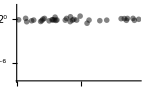

```mathematica
bctrlpointslog
```

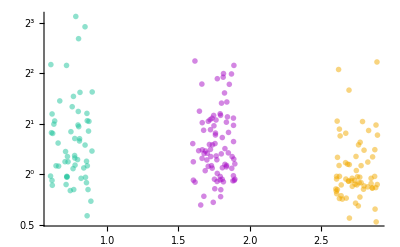

```mathematica
b=Show[{b1203pointslog, b1025pointslog,b0119pointslog,b0125pointslog (*  ,bctrlpointslog*)}, PlotRange->All]
bAllpoints=b;
```

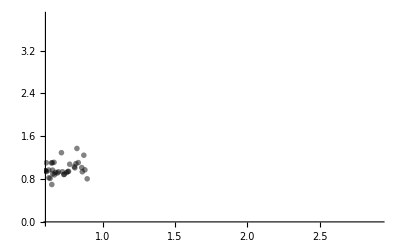

```mathematica
b=Show[b1203, b1025,b0119,b0125, bctrlpoints]
bAll=b;
```

```mathematica
a = (* Join[ *) Table[Join[ratios1203[[type]],ratios1025[[type]],ratios0119[[type]],ratios0125[[type]] ], {type,1,3}](*  ,{ratiosctrl}]  *); 
aAll = a;
Dimensions/@a
```

{{58},{82},{66}}

#### Remake B&W plot

```mathematica
Log2[12]//N
```

3.58496

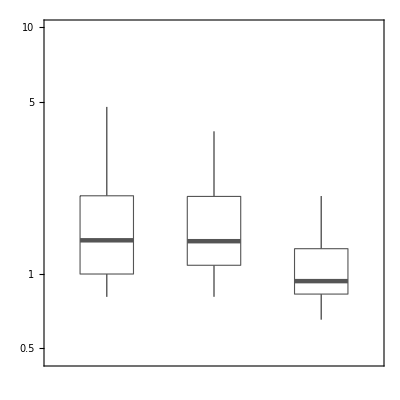

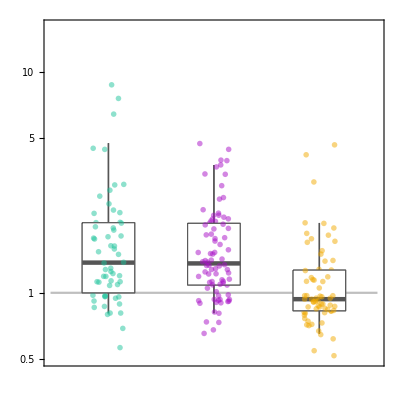

```mathematica
bwchart = BoxWhiskerChart[a,{ {"MedianMarker",Directive[Thickness[.008],Darker[Gray]]},{"Whiskers",Directive[Thick,Darker[Gray]]},{"Fences",1,Opacity[0]}} ,ChartStyle->{{EdgeForm[{Darker[Gray], Thickness[Large]}  ]} , {White} } , AspectRatio->1 ,ScalingFunctions->"Log2" ,(*Ticks->{{-.5,1,2,4,8}},Axes->True,  *){Method->{"BoxRange"->(Quantile[#,{.05,.25,.5,.75,.95},{{1,-1},{0,1}}]&)}}]
myBoxWhiskerPlotall=  
Show[   bwchart,  Plot[x=0,{x,0.2,3.3}, PlotStyle->Opacity[0.5,Gray]],bwchart,bAllpoints,AspectRatio -> 1,BaseStyle->{FontFamily->"Arial",FontSize->18},PlotRange-> {-1,Log2[16]}]
```

```mathematica
WMWtestNTTAvTLTAvNTTLall = { MannWhitneyTest[ {a[[1]],a[[3]] }], MannWhitneyTest[ {a[[2]],a[[3]] }], MannWhitneyTest[ {a[[1]],a[[2]] }] ,    MannWhitneyTest[ {a[[3]],a[[4]] }] , MannWhitneyTest[ {a[[2]],a[[4]] }] }
```

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦3⟧ is longer than depth of object.

MannWhitneyTest::rctndmln: The argument {1⟦1⟧,1⟦3⟧} at position 1 should be a list containing two rectangular arrays of real numbers where each array has length greater than its dimension.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

MannWhitneyTest::rctndmln: The argument {1⟦2⟧,1⟦3⟧} at position 1 should be a list containing two rectangular arrays of real numbers where each array has length greater than its dimension.

MannWhitneyTest::rctndmln: The argument {1⟦1⟧,1⟦2⟧} at position 1 should be a list containing two rectangular arrays of real numbers where each array has length greater than its dimension.

General::stop: Further output of MannWhitneyTest::rctndmln will be suppressed during this calculation.

{MannWhitneyTest[{1⟦1⟧,1⟦3⟧}],MannWhitneyTest[{1⟦2⟧,1⟦3⟧}],MannWhitneyTest[{1⟦1⟧,1⟦2⟧}],MannWhitneyTest[{1⟦3⟧,1⟦4⟧}],MannWhitneyTest[{1⟦2⟧,1⟦4⟧}]}

BoxWhiskerChart::ldata: 1 is not a valid dataset or list of datasets.

General::stop: Further output of BoxWhiskerChart::ldata will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

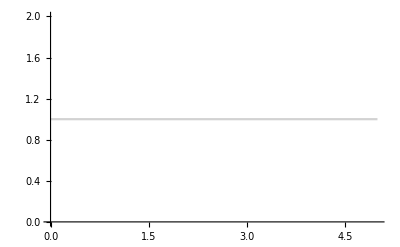
Show[BoxWhiskerChart[1,{{MedianMarker,Directive[Thickness[0.005],Opacity[0.35]]},{Whiskers,Directive[Thickness[0.005],Opacity[0.35]]},{Fences,Opacity[0]}},ChartStyle→{{EdgeForm[{Opacity[0.4,GrayLevel[0]],Thickness[0.0025]}]},{Opacity[0]}},BaseStyle→{FontFamily→Arial,FontSize→28},AspectRatio→1],-Graphics-,-Graphics-,AspectRatio→1.5]

```mathematica
myBoxWhiskerPlot0125 = Show[   BoxWhiskerChart[a,{ {"MedianMarker",Directive[Thickness[.005],Opacity[.35]]},{"Whiskers",Directive[Thickness[.005],Opacity[.35]] },{"Fences",Opacity[0]}} ,ChartStyle->{{EdgeForm[{Opacity[ 0.4,Black], Thickness[0.0025]}  ]} , {Opacity[0]} } , BaseStyle->{FontFamily->"Arial",FontSize->28},AspectRatio->1  ] ,bAllpoints,  Plot[x=1,{x,0,5}, PlotStyle->Opacity[0.35,Gray] ], AspectRatio -> 1.5]
```

BoxWhiskerChart::ldata: 1 is not a valid dataset or list of datasets.

General::stop: Further output of BoxWhiskerChart::ldata will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

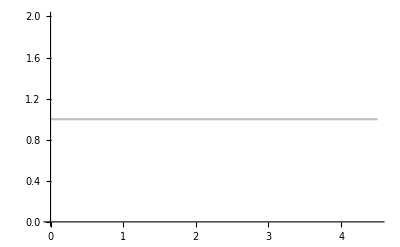
Show[BoxWhiskerChart[1,{{Outliers,Opacity[0]},{MedianMarker,Thickness[0.01]},{Whiskers,Thickness[0.005]},{Fences,1,Opacity[0]}},ChartBaseStyle→Directive[Opacity[0.15,GrayLevel[0.5]]],BaseStyle→{FontFamily→Arial,FontSize→42}],-Graphics-,-Graphics-,AspectRatio→0.5]

```mathematica
Show[  BoxWhiskerChart[a , {{"Outliers", Opacity[0]},{"MedianMarker",Thickness[0.01]},{"Whiskers",Thickness[0.005]},{"Fences",1,Opacity[0]}},ChartBaseStyle-> Directive[ Opacity[0.15,Gray]  ]      ,BaseStyle->{FontFamily->"Arial",FontSize->42}] , bAllpoints,  Plot[x=1,{x,0,4.5}, PlotStyle->Opacity[0.5,Gray]], AspectRatio -> .5]
```

```mathematica
{Mean/@a,StandardDeviation/@a}//TableForm
```

1
1

### Count cells with accumulation gain

Calculate the Fraction of cells that have accumulation. 
This is determined by the late 15h time point having MORE nuc/cyto cy3 signal ratio than the early 4h time point. 
Can make stricter by multiplying a by the early time point ( for example, early accumulation * 1.5 is greater than late accumulation )

#### All Cells:

```mathematica
a=1;
 {  
( Length@Cases[  aAll[[1]] ,b_/;  b>1]/ Length@aAll[[1]])  //N , 
( Length@Cases[  aAll[[2]] ,b_/;  b>1]/ Length@aAll[[2]])  //N, 
( Length@Cases[  aAll[[3]] ,b_/;  b>1]/ Length@aAll[[3]])  //N 
 }
```

{0.741379,0.780488,0.378788}

#### 12032017:

```mathematica
myRatioAccumulation1203 = {  
Count[Cases[  myRatioNT1203[[1]]  ,{n_,m_}->  a*n<m], True] / Length@myRatioNT1203[[1]]  //N , 
Count[Cases[  myRatioTL1203[[1]]  ,{n_,m_}->  a*n<m], True] / Length@myRatioTL1203[[1]]  //N , 
Count[Cases[  myRatioTA1203[[1]]  ,{n_,m_}->  a*n<m], True] / Length@myRatioTA1203[[1]]  //N   }
```

{0.,0.,0.}

#### 10252018:

```mathematica
myRatioAccumulation1025 = {  
Count[Cases[  myRatioNT1025[[1]]  ,{n_,m_}->  a*n<m], True] / Length@myRatioNT1025[[1]]  //N , 
Count[Cases[  myRatioTL1025[[1]]  ,{n_,m_}->  a*n<m], True] / Length@myRatioTL1025[[1]]  //N , 
Count[Cases[  myRatioTA1025[[1]]  ,{n_,m_}->  a*n<m], True] / Length@myRatioTA1025[[1]]  //N   }
```

{0.,0.,0.}

#### 01152019:

```mathematica
myRatioAccumulation0115  = { 
Count[Cases[  myRatiob1a  ,{n_,m_}->  a*n<m], True] / Length@myRatiob1a  //N , 
Count[Cases[  myRatiob2a  ,{n_,m_}->  a*n<m], True] / Length@myRatiob2a  //N , 
Count[Cases[  myRatiob3a  ,{n_,m_}->  a*n<m], True] / Length@myRatiob3a  //N   }
```

{0.,0.,0.}

#### 01252019:

```mathematica
myRatioAccumulation0125  =  {  
Count[Cases[  myRatio3  ,{n_,m_}->  a*n<m], True] / Length@myRatio3  //N  , 
Count[Cases[  Join[ myRatio1 ,myRatio4] ,{n_,m_}-> a* n<m], True] / Length@ Join[ myRatio1 ,myRatio4] //N , 
Count[Cases[  myRatio2  ,{n_,m_}->  a*n<m], True] / Length@myRatio2  //N  }
(*  Count[Cases[  myRatio4  ,{n_,m_}->  n<m], True] / Length@myRatio4  //N    *)
```

{0.,0.,0.}

```mathematica
myRatioAccumulation0125  =  {  
Count[Cases[  myRatio3  ,{n_,m_}->  a*n<m], True] / Length@myRatio3  //N  , 
Count[Cases[  myRatio4 ,{n_,m_}-> a* n<m], True] / Length@ myRatio4 //N , 
Count[Cases[  myRatio2  ,{n_,m_}->  a*n<m], True] / Length@myRatio2  //N  }
```

{0.,0.,0.}

#### All accumulatons combined:

```mathematica
{myRatioAccumulation1203  +  myRatioAccumulation1025  +  myRatioAccumulation0115 + myRatioAccumulation0125}/4
(*({myRatioAccumulation1203  +  myRatioAccumulation1025  +  myRatioAccumulation0115 + myRatioAccumulation0125}/4) [[1]]* counts  *)
counts
```

{{0.,0.,0.}}

{58,82,66}

### Count cells with accumulation gain #2: Table thru accumulation gain cutoffs

#2: TABLE the data so you can look at how the cells with accumulation change as you make the criteria more strict
Calculate the Fraction of cells that have accumulation. 
This is determined by the late 15h time point having MORE nuc/cyto cy3 signal ratio than the early 4h time point. 
Can make stricter by multiplying a by the early time point ( for example, early accumulation * 1.5 is greater than late accumulation )

#### 12032017:

```mathematica
a=1.5;
myRatioAccumulation1203  =  Table[  
{Count[Cases[  myRatioNT1203[[1]]  ,{n_,m_}->  a*n<m], True] / Length@myRatioNT1203[[1]]  //N , 
Count[Cases[  myRatioTL1203[[1]]  ,{n_,m_}->  a*n<m], True] / Length@myRatioTL1203[[1]]  //N , 
Count[Cases[  myRatioTA1203[[1]]  ,{n_,m_}->  a*n<m], True] / Length@myRatioTA1203[[1]]  //N }
 , {a,1,2, 0.1}]
```

{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}

#### 10252018:

```mathematica
myRatioAccumulation1025 = Table[ {  
Count[Cases[  myRatioNT1025[[1]]  ,{n_,m_}->  a*n<m], True] / Length@myRatioNT1025[[1]]  //N , 
Count[Cases[  myRatioTL1025[[1]]  ,{n_,m_}->  a*n<m], True] / Length@myRatioTL1025[[1]]  //N , 
Count[Cases[  myRatioTA1025[[1]]  ,{n_,m_}->  a*n<m], True] / Length@myRatioTA1025[[1]]  //N   } 
 , {a,1,2, 0.1}]
```

{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}

#### 01152019:

```mathematica
myRatioAccumulation0115  = Table[ { 
Count[Cases[  myRatiob1a  ,{n_,m_}->  a*n<m], True] / Length@myRatiob1a  //N , 
Count[Cases[  myRatiob2a  ,{n_,m_}->  a*n<m], True] / Length@myRatiob2a  //N , 
Count[Cases[  myRatiob3a  ,{n_,m_}->  a*n<m], True] / Length@myRatiob3a  //N   }
 , {a,1,2, 0.1}]
```

{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}

#### 01252019:

```mathematica
myRatioAccumulation0125  =  Table[ {  
Count[Cases[  myRatio3  ,{n_,m_}->  a*n<m], True] / Length@myRatio3  //N  , 
Count[Cases[  Join[ myRatio1 ,myRatio4] ,{n_,m_}-> a* n<m], True] / Length@ Join[ myRatio1 ,myRatio4] //N , 
Count[Cases[  myRatio2  ,{n_,m_}->  a*n<m], True] / Length@myRatio2  //N  }
 , {a,1,2, 0.1}]
(*  Count[Cases[  myRatio4  ,{n_,m_}->  n<m], True] / Length@myRatio4  //N    *)
```

{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}

```mathematica
myRatioAccumulation0125  =  Table[ {  
Count[Cases[  myRatio3  ,{n_,m_}->  a*n<m], True] / Length@myRatio3  //N  , 
Count[Cases[  myRatio4 ,{n_,m_}-> a* n<m], True] / Length@ myRatio4 //N , 
Count[Cases[  myRatio2  ,{n_,m_}->  a*n<m], True] / Length@myRatio2  //N  }
 , {a,1,2, 0.1}]
```

{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}

#### All accumulatons combined:

```mathematica
multipfactor = Table[a,{a,1,2, 0.1}]
```

{1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.}

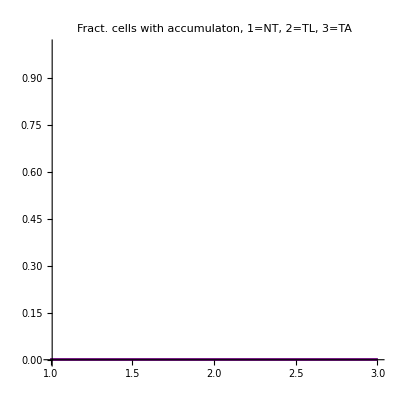

```mathematica
ListLinePlot[#,ColorFunction->"Rainbow" , PlotRange -> {{1,3},{0,1}} , AspectRatio->1,
 PlotLabel -> "Fract. cells with accumulaton, 1=NT, 2=TL, 3=TA"  ]&/@{(myRatioAccumulation1203 + myRatioAccumulation1025 + myRatioAccumulation0115+myRatioAccumulation0125)/4}
```

## Graphs, 4h vs 15h all cells Use ALL cells, whether or not they were PT’d

```mathematica
axes = {{"nuc/cyto ratio, 4 h" } , { "nuc/cyto ratio, 15 h" }}
```

{{nuc/cyto ratio, 4 h},{nuc/cyto ratio, 15 h}}

```mathematica
counts0125replicatesjoined = {counts0125[[3]], counts0125[[4]]  , counts0125[[2]]  }
```

{10,18,20}

```mathematica
{counts1203 , counts1025 ,counts0119  , counts0125replicatesjoined}
```

{{22,18,26},{19,35,17},{7,11,3},{10,18,20}}

```mathematica
counts = counts1203 +counts1025 +counts0119  + counts0125replicatesjoined
```

{58,82,66}

```mathematica
legend = SwatchLegend[{color1, color2,color3},{"Non-tethering AGO2 ctrl","Tethering-LacZ ctrl","Tethering AGO2"},  LabelStyle->{FontFamily->"Arial",FontSize->18}  ]
```

```mathematica
textfont =BaseStyle->{FontFamily->"Arial",FontSize->18};
```

```mathematica
style = {PlotRange->{{0,5},{0,10}},AxesOrigin->{0,0} , AspectRatio->2   ,BaseStyle->{FontFamily->"Arial",FontSize->18}, PlotRange->{{0,5},{0,10}},AxesOrigin->{0,0} , AspectRatio->2 } ;
```

```mathematica
xylineplot = Plot [x,{x,0,10}, {PlotRange->{{0,5},{0,10}},PlotStyle -> {Dashed, Opacity[.2, Gray]}, AxesOrigin->{0,0} , AspectRatio->2   ,PlotRange->{{0,5},{0,10}},AxesOrigin->{0,0} , AspectRatio->2 }];
```

METHODS: 
U2OS cells were bead loaded with the 15xBoxB reporter plasmid, HALO-MCP to label the mRNA, Cy3-FLAG-Fab to label nascent translation, and either tethering GFP-AGO2 or controls non-tethering GFP-AGO2 or tethering GFP-LacZ plasmids. 4 hours later, all the cells with detectable levels of the assay components were imaged every 30 m for 15 hours. Of these cells, we processed and analyzed only the healthy, non-dividing, cells with >10 detectable reporter mRNA and which stayed in the frame throughout the timeframe. The video below shows each of the analyzed cells at all time points. The 561 nm channel which detects translation was pseudocolored to show intensity of the signal. Over time, cells which produced the nuclear reporter protein show an accumulation in the nucleus.

The nuc/cyto ratio at 4 h vs 15 h of tethered - AGO2, plus non - tethered AGO2 and tethering - controls. 
Intensities were background subtracted and measured using Mathematica myROI

CRITERIA of cell selection: 
All cells found that fit these criteria were imaged ... 
(1) Cells were healthy (no blebs or disfiguration), not dividing, not dying
(2) Cells were bead-loaded and expressing GFP in the correct localization (~1 or 2 cells were expressing delocalized GFP, these cells were excluded) 
(3) Cells had ≥ 10 mRNA *at movie start

If throughout the acquired movie cells lost any of these criteria (except for the mRNA count), the cell was removed from the dataset. 

For particle tracking (NOT this analysis, the graphs below show EVERY cell fitting above criteria), cells were excluded if the mRNA was not detectable/trackable.

{The counts of cells per condition:  NT:  58,  TL: ,82,  TA:  66}

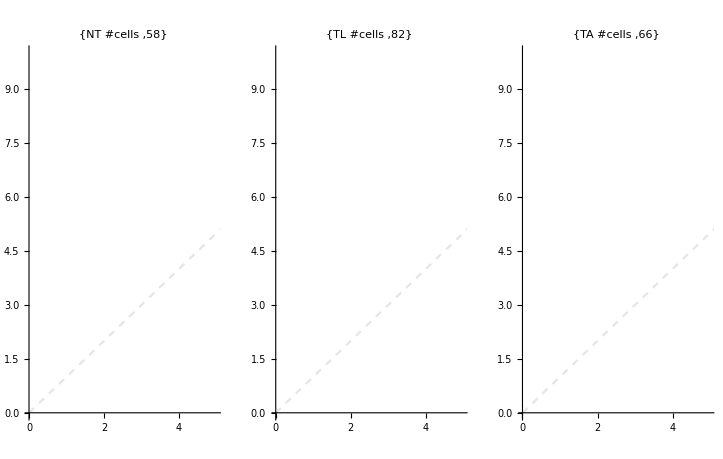

```mathematica
legend
{"The counts of cells per condition:  NT: "   Text[counts[[1]]]  ,   "  TL: " ,  Text[counts[[2]]]   ,  "  TA: " Text[counts[[3]]]   }
GraphicsRow[{
Show[{ xylineplot, plotsNTratio,plotsNTratio1203,plotsb1a, plotsb3} ,  style[[All]], PlotLabel-> {"NT #cells  "   ,counts[[1]] } ]   ,
Show[{xylineplot,  plotsTLratio,plotsTLratio1203,plotsb2a ,  plotsb4} ,   style[[All]],  PlotLabel-> {"TL #cells  "   ,counts[[2]] }    ]   ,
Show[{ xylineplot, plotsTAratio, plotsTAratio1203,plotsb3a, plotsb2} ,  style[[All]],  PlotLabel-> {"TA #cells  "   ,counts[[3]] }     ]      }]
```

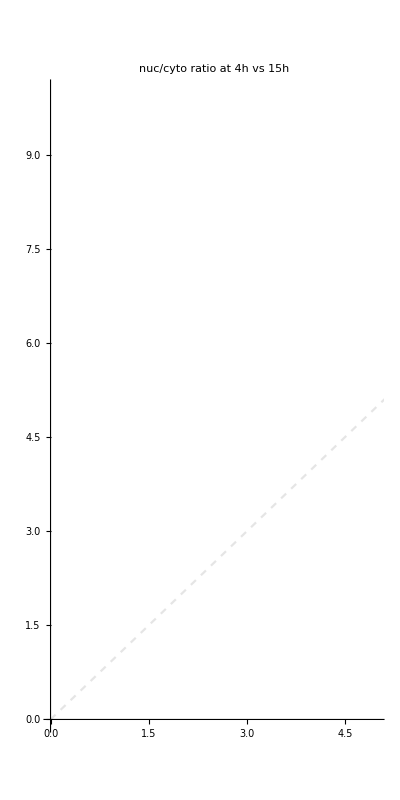

```mathematica
Show[{{xylineplot, plotsNTratio,plotsTLratio,plotsTAratio, plotsNTratio1203,plotsTLratio1203,plotsTAratio1203,plotsb1a,plotsb2a,plotsb3a, plotsb4,plotsb2,plotsb3}
} ,  style[[All]],   PlotLabel->"nuc/cyto ratio at 4h vs 15h"  ]
```

## Combine multiple days of data ONLY use the data from cells that were also particle tracked

#### Get #s of mRNA per cell

Find the particle track folders and import the countRYPWall files, which count the # of classified and total mRNAs 
“pt” means particle track... 
ONLY the count files! not the myROI files

```mathematica
analysisFolder1203pt = "/Volumes/BITTY/_long_timeframe_transient_mini/20171203_15h/Analysis/" ;
analysisFolder1025pt = "/Volumes/BITTY/_long_timeframe_transient_mini/20181025_27_TA_TL_NT_15h/Analysis/" ;
analysisFolder1103pt = "/Volumes/BITTY/_long_timeframe_transient_mini/20181103_15h_TL/Analysis/" ;
```

```mathematica
filesNTpt1203= FileNames[analysisFolder1203pt <> "*NT*_countRYPWall_filter.dat"];
filesTLpt1203 =  FileNames[analysisFolder1203pt <> "*TL*_countRYPWall_filter.dat"] ;
filesTApt1203 = FileNames[analysisFolder1203pt <> "*TA*_countRYPWall_filter.dat"] ;
```

```mathematica
mycountfilesNT1203  = Table[<<(filesNTpt1203[[i]]),{i,1,Length@filesNTpt1203,1}] ;
mycountfilesTL1203  = Table[<<(filesTLpt1203[[i]]),{i,1,Length@filesTLpt1203,1}]; 
mycountfilesTA1203  = Table[<<(filesTApt1203[[i]]),{i,1,Length@filesTApt1203,1}];
```

```mathematica
filesNTpt1025= FileNames[analysisFolder1025pt <> "*NT*_countRYPWall_filter.dat"];
filesTLpt1025 =  FileNames[analysisFolder1025pt <> "*TL*_countRYPWall_filter.dat"] ;
filesTApt1025 = FileNames[analysisFolder1025pt <> "*TA*_countRYPWall_filter.dat"] ;

mycountfilesNT1025  = Table[<<(filesNTpt1025[[i]]),{i,1,Length@filesNTpt1025,1}] ;
mycountfilesTL1025  = Table[<<(filesTLpt1025[[i]]),{i,1,Length@filesTLpt1025,1}]; 
mycountfilesTA1025  = Table[<<(filesTApt1025[[i]]),{i,1,Length@filesTApt1025,1}];
```

```mathematica
filesTLpt1103 =  FileNames[analysisFolder1103pt <> "*TL*_countRYPWall_filter.dat"] ;
mycountfilesTL1103 = Table[<<(filesTLpt1103[[i]]),{i,1,Length@filesTLpt1103,1}];
```

```mathematica
filesNTpt = Join[filesNTpt1203,filesNTpt1025];
filesTLpt = Join[filesTLpt1203,filesTLpt1025, filesTLpt1103];
filesTApt = Join[filesTApt1203,filesTApt1025];
```

```mathematica
titles = mycountfilesNT1203[[1,1]]
```

Part::partd: Part specification {Null,«13»,{{{mytimes,countYellowOnly},{mytimes,countWhiteOnly},{mytimes,countPurpleOnly},{mytimes,countRedOnly},{mytimes,total spot count}},{{{4.,6},{4.5,13},{5.,25},{5.5,37},{6.,36},{6.5,41},{7.,45},{7.5,55},{8.,50},{8.5,39},{9.,41},{9.5,44},{10.,42},{10.5,31},{11.,42},{11.5,39},{12.,36},{12.5,28},{13.,26},{13.5,23},{14.,26},{14.5,17},{15.,16},{15.5,10},{16.,10},{16.5,10}},«3»,{{4.,142},{4.5,156},«22»,{16.,152},{16.5,160}}}}}⟦1,1⟧ is longer than depth of object.

```mathematica
mycountfilesNT1025[[All,2]]//Dimensions
```

{14,5,24,2}

Data structure: 
Type (NT, TL, TA) in different files 
{header or data   { cell   {   RYPWall {  Time } } } }

```mathematica
i=1;
```

```mathematica
.10
```

```mathematica
a =<<(filesNTpt1203[[i]]) [[2,All,1;;All;;22,2]]
```

Part::partd: Part specification Null⟦2,All,1;;All;;22,2⟧ is longer than depth of object.

Null⟦2,All,1;;All;;22,2⟧

```mathematica
countsRNA4h15hNT=  Table[<<(filesNTpt[[i]]),{i,1,Length@filesNTpt,1}] [[All,2,All,1;;All;;22,2]] ;
Length@countsRNA4h15hNT
 countsRNA4h15hTL=  Table[<<(filesTLpt[[i]]),{i,1,Length@filesTLpt,1}] [[All,2,All,1;;All;;22,2]] ;
Length@ countsRNA4h15hTL
 countsRNA4h15hTA=  Table[<<(filesTApt[[i]]),{i,1,Length@filesTApt,1}] [[All,2,All,1;;All;;22,2]] ;
Length@countsRNA4h15hTA 
(*This gives me the 4h and 15h timepoints of ALL cells of EACH OF THE 5 TYPES OF SPOTS! *)
```

28

35

32

```mathematica
(*exmaple...*)  titles
```

{{mytimes,countYellowOnly},{mytimes,countWhiteOnly},{mytimes,countPurpleOnly},{mytimes,countRedOnly},{mytimes,total spot count}}

#### Filter out nuc accumulation cells that have mRNA count info (ONLY the cells that were PT’d)

FInd the analysis folders of the nuc accumulation myROIs, import ONLY the ones htat have a corresponding mRNA count.dat file, and make sure they’re in the right order

```mathematica
(*Which cell is it based on file name?*) 
list1 = Table[ StringCases[filesNT[[i]],"MAX_NT"~~x__~~"_myR"->x] , {i,1,Length@filesNT}]
list1//Length
list2 = Table[ StringCases[filesNTpt[[i]],"MAX_NT"~~x__~~"_count"->x] , {i,1,Length@filesNTpt}]
list2//Length
```

{{01},{02},{03},{04},{05},{06},{08},{12},{13},{14},{16},{17},{18},{20},{22},{23},{25},{26_3cells},{27}}

19

{{00},{02},{06},{07},{08},{10},{14},{15},{21},{28},{30},{32},{34},{35},{01},{03},{04},{05},{12},{13},{14},{17},{18},{22},{23},{25},{26_3cells},{27}}

28

This means that there are 22 nuc/cyto ratio files, but only 14 of them are Particle tracked. 
Below, I ONLY select the nuc/cyto files that also have PT data. 
The end product is a list of nuc/cyto files (and, below that, the data) in the same order of the PT files....

#### Find nuc/cyto ratios files from ONLY the cells with PT data:

#### Here are the nuc/cyto files : 1203

```mathematica
analysisFolder1203="/Volumes/BITTY/_long_timeframe_transient_mini/20171203_15h/4h15h_only/Analysis/"
```

/Volumes/BITTY/_long_timeframe_transient_mini/20171203_15h/4h15h_only/Analysis/

```mathematica
filesNT = FileNames[analysisFolder1203 <> "*NT*ROI.dat"];
filesTL =  FileNames[analysisFolder1203 <> "*TL*ROI.dat"] ;
filesTA = FileNames[analysisFolder1203 <> "*TA*ROI.dat"] ;
```

```mathematica
filesNTpt= FileNames[analysisFolder1203pt <> "*NT*_countRYPWall_filter.dat"];
filesTLpt =  FileNames[analysisFolder1203pt <> "*TL*_countRYPWall_filter.dat"] ;
filesTApt = FileNames[analysisFolder1203pt <> "*TA*_countRYPWall_filter.dat"] ;
```

NT 1203:

```mathematica
list2 = Table[ StringCases[filesNTpt[[i]],"NT"~~x__~~"_count"->x] , {i,1,Length@filesNTpt}]
filesNTptnc1203 = Table[analysisFolder1203<>"MAX_NT"<>list2[[i]]<>"_myROI.dat",{i,1,Length@list2}];
filesNTptnc1203 //Length
FileNames[filesNTptnc1203]//Length
```

{{00},{02},{06},{07},{08},{10},{14},{15},{21},{28},{30},{32},{34},{35}}

14

14

TL 1203:

```mathematica
list2 = Table[ StringCases[filesTLpt[[i]],"MAX_TL"~~x__~~"_count"->x] , {i,1,Length@filesTLpt}]
filesTLptnc1203 = Table[analysisFolder1203<>"MAX_TL"<>list2[[i]]<>"_myROI.dat",{i,1,Length@list2}];
filesTLptnc1203 //Length
FileNames[filesTLptnc1203]//Length
Table[ StringCases[filesTLptnc1203[[i]],"TL"~~x__~~"_myROI"->x] , {i,1,Length@filesTLptnc1203}]
```

{{03},{05},{06},{09},{12},{16},{21},{22},{24},{27}}

10

10

{{03},{05},{06},{09},{12},{16},{21},{22},{24},{27}}

TA 1203:

```mathematica
list2 = Table[ StringCases[filesTApt[[i]],"TA"~~x__~~"_count"->x] , {i,1,Length@filesTApt}]
filesTAptnc1203 = Table[analysisFolder1203<>"MAX_TA"<>list2[[i]]<>"_myROI.dat",{i,1,Length@list2}];
filesTAptnc1203 //Length
FileNames[filesTAptnc1203]//Length
Table[ StringCases[filesTAptnc1203[[i]],"TA"~~x__~~"_myROI"->x] , {i,1,Length@filesTAptnc1203}]
```

{{01},{05},{07},{08bottom},{08},{10},{14},{21},{24},{25},{27},{28},{29},{30},{31},{32},{33},{39}}

18

18

{{01},{05},{07},{08bottom},{08},{10},{14},{21},{24},{25},{27},{28},{29},{30},{31},{32},{33},{39}}

#### Here are the nuc/cyto files : 1025

```mathematica
analysisFolder1025 = "/Volumes/BITTY/_long_timeframe_transient_mini/20181025_27_TA_TL_NT_15h/4h_15h_only/Analysis/";
filesNT = FileNames[analysisFolder1025 <> "*NT*ROI.dat"]; Length@filesNT
filesTL =  FileNames[analysisFolder1025 <> "*TL*ROI.dat"] ;Length@filesTL
filesTA = FileNames[analysisFolder1025 <> "*TA*ROI.dat"] ;  Length@filesTA
```

19

6

17

```mathematica
filesNTpt= FileNames[analysisFolder1025pt <> "*NT*_countRYPWall_filter.dat"];
filesTLpt =  FileNames[analysisFolder1025pt <> "*TL*_countRYPWall_filter.dat"] 
filesTApt = FileNames[analysisFolder1025pt <> "*TA*_countRYPWall_filter.dat"] ;
```

{/Volumes/BITTY/_long_timeframe_transient_mini/20181025_27_TA_TL_NT_15h/Analysis/MAX_TL05_countRYPWall_filter.dat,/Volumes/BITTY/_long_timeframe_transient_mini/20181025_27_TA_TL_NT_15h/Analysis/MAX_TL06_countRYPWall_filter.dat,/Volumes/BITTY/_long_timeframe_transient_mini/20181025_27_TA_TL_NT_15h/Analysis/MAX_TL10_countRYPWall_filter.dat,/Volumes/BITTY/_long_timeframe_transient_mini/20181025_27_TA_TL_NT_15h/Analysis/MAX_TL11_weird_countRYPWall_filter.dat,/Volumes/BITTY/_long_timeframe_transient_mini/20181025_27_TA_TL_NT_15h/Analysis/MAX_TL13_countRYPWall_filter.dat,/Volumes/BITTY/_long_timeframe_transient_mini/20181025_27_TA_TL_NT_15h/Analysis/MAX_TL18_countRYPWall_filter.dat}

NT 1025:

```mathematica
list2 = Table[ StringCases[filesNTpt[[i]],"MAX_NT"~~x__~~"_count"->x] , {i,1,Length@filesNTpt}]
filesNTptnc1025 = Table[analysisFolder1025<>"MAX_NT"<>list2[[i]]<>"_myROI.dat",{i,1,Length@list2}];
filesNTptnc1025 //Length
FileNames[filesNTptnc1025]//Length
Table[ StringCases[filesNTptnc1025[[i]],"MAX_NT"~~x__~~"_myROI"->x] , {i,1,Length@filesNTptnc1025}]
```

{{01},{03},{04},{05},{12},{13},{14},{17},{18},{22},{23},{25},{26_3cells},{27}}

14

14

{{01},{03},{04},{05},{12},{13},{14},{17},{18},{22},{23},{25},{26_3cells},{27}}

TL 1025:

```mathematica
list2 = Table[ StringCases[filesTLpt[[i]],"MAX_TL"~~x__~~"_count"->x] , {i,1,Length@filesTLpt}]
filesTLptnc1025 = Table[analysisFolder1025<>"MAX_TL"<>list2[[i]]<>"_myROI.dat",{i,1,Length@list2}];
filesTLptnc1025 //Length
Table[ StringCases[filesTLptnc1025[[i]],"MAX_TL"~~x__~~"_myROI"->x] , {i,1,Length@filesTLptnc1025}]
```

{{05},{06},{10},{11_weird},{13},{18}}

6

{{05},{06},{10},{11_weird},{13},{18}}

TA 1025:

```mathematica
list2 = Table[ StringCases[filesTApt[[i]],"MAX_TA"~~x__~~"_count"->x] , {i,1,Length@filesTApt}]
filesTAptnc1025 = Table[analysisFolder1025<>"MAX_TA"<>list2[[i]]<>"_myROI.dat",{i,1,Length@list2}];
filesTAptnc1025 //Length
FileNames[filesTAptnc1025]//Length
Table[ StringCases[filesTAptnc1025[[i]],"MAX_TA"~~x__~~"_myROI"->x] , {i,1,Length@filesTAptnc1025}]
```

{{04},{05},{06},{08},{12},{13},{14_shitton},{16},{19},{20_sick},{21},{22},{25},{28}}

14

14

{{04},{05},{06},{08},{12},{13},{14_shitton},{16},{19},{20_sick},{21},{22},{25},{28}}

#### Here are the nuc/cyto files : 1103

```mathematica
analysisFolder1103 = "/Volumes/BITTY/_long_timeframe_transient_mini/20181103_15h_TL/4h15h_only/Analysis/"
```

/Volumes/BITTY/_long_timeframe_transient_mini/20181103_15h_TL/4h15h_only/Analysis/

```mathematica
filesTLpt =  FileNames[analysisFolder1103pt <> "*TL*_countRYPWall_filter.dat"] ;
```

```mathematica
filesTL =  FileNames[analysisFolder1103 <> "*TL*ROI.dat"] ;
```

TL 1103:

```mathematica
list2 = Table[ StringCases[filesTLpt[[i]],"MAX_TL"~~x__~~"_count"->x] , {i,1,Length@filesTLpt}]
filesTLptnc1103 = Table[analysisFolder1103<>"MAX_TL"<>list2[[i]]<>"_myROI.dat",{i,1,Length@list2}];
filesTLptnc1103 //Length
FileNames[filesTLptnc1103]//Length
Table[ StringCases[filesTLptnc1103[[i]],"MAX_TL"~~x__~~"_myROI"->x] , {i,1,Length@filesTLptnc1103 } ]
```

{{36},{37},{38},{39},{40},{41},{42},{43},{46},{48},{49},{51},{55},{57},{58},{59},{60},{61_top},{62}}

19

19

{{36},{37},{38},{39},{40},{41},{42},{43},{46},{48},{49},{51},{55},{57},{58},{59},{60},{61_top},{62}}

#### Find ONLY the nuc/cyto ratios from cells that have Particle Tracking data ...

NOTE: I’m putting all the days together, instead of separating them apart and plotting them differently now...

These are the names of the myROI files used in this experiment ...

```mathematica
NTallcellsNCPT = Join[filesNTptnc1203, filesNTptnc1025];
TLallcellsNCPT = Join[filesTLptnc1203,filesTLptnc1025, filesTLptnc1103 ] ;
TAallcellsNCPT = Join[filesTAptnc1203 , filesTAptnc1025 ];
(* "/Volumes/BITTY/_long_timeframe_transient_mini/20171203_15h/4h15h_only/Analysis/MAX_NT00_myROI.dat" *)
```

```mathematica
countNCPTall  = {Length@NTallcellsNCPT , Length@TLallcellsNCPT, Length@TAallcellsNCPT}
```

{28,35,32}

```mathematica
i=1;
mymaskfilesNTncpt  =<<(NTallcellsNCPT[[i]]);
```

```mathematica
mymaskfilesNTncpt  = Table[<<(NTallcellsNCPT[[i]]),{i,1,Length@NTallcellsNCPT,1}]; 
mymaskfilesTLncpt  = Table[<<(TLallcellsNCPT[[i]]),{i,1,Length@TLallcellsNCPT,1}]; 
mymaskfilesTAncpt  = Table[<<(TAallcellsNCPT[[i]]),{i,1,Length@TAallcellsNCPT,1}];
```

```mathematica
(*  mymaskfiles  = Table[<<(filesTA[[i]]),{i,1,Length@filesTA,1}];   *)
Length/@mymaskfilesNTncpt
bkgGIntNT =mymaskfilesNTncpt[[All,1,1;;2,3,2]] ;
cytoGIntNT =mymaskfilesNTncpt[[All,2,1;;2,3,2]] ;
nucGIntNT =mymaskfilesNTncpt[[All,3,1;;2,3,2]] ;
```

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
Length/@mymaskfilesTLncpt
bkgGIntTL =mymaskfilesTLncpt[[All,1,1;;2,3,2]];
cytoGIntTL =mymaskfilesTLncpt[[All,2,1;;2,3,2]];
nucGIntTL =mymaskfilesTLncpt[[All,3,1;;2,3,2]];
```

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
Length/@mymaskfilesTAncpt
bkgGIntTA =mymaskfilesTAncpt[[All,1,1;;2,3,2]] ;
cytoGIntTA =mymaskfilesTAncpt[[All,2,1;;2,3,2]] ;
nucGIntTA =mymaskfilesTAncpt[[All,3,1;;2,3,2]] ;
```

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
(*  myRatio = (nucGInt-bkgGInt)/(cytoGInt-bkgGInt)
```

```mathematica
(*update *) 
myRatioTimeNT = {(nucGIntNT-bkgGIntNT)/(cytoGIntNT-bkgGIntNT)} //  Table[   Transpose[ {{4,15}, # [[1,i]]}  ],{i,1,Length@nucGIntNT}]& ;
myRatioTimeTL = {(nucGIntTL-bkgGIntTL)/(cytoGIntTL-bkgGIntTL)} //  Table[   Transpose[ {{4,15}, # [[1,i]]}  ],{i,1,Length@nucGIntTL}]& ;
myRatioTimeTA= {(nucGIntTA-bkgGIntTA)/(cytoGIntTA-bkgGIntTA)} //  Table[   Transpose[ {{4,15}, # [[1,i]]}  ],{i,1,Length@nucGIntTA}]& ;
```

List out the file names ONLY, so we can compare them with the countYWPRall file names

#### Check to make sure the file names of the RNA count files match the file names of the myROI mask files ...

Compare (1) mask myROI file names with (2)

```mathematica
filesNTpt = Join[filesNTpt1203,filesNTpt1025];
filesTLpt = Join[filesTLpt1203,filesTLpt1025, filesTLpt1103];
filesTApt = Join[filesTApt1203,filesTApt1025];
```

```mathematica
Transpose[{StringExtract[#,"/"->-1]&/@ NTallcellsNCPT , StringExtract[#,"/"->-1]&/@ filesNTpt}]//TableForm
```

MAX_NT00_myROI.dat | MAX_NT00_countRYPWall_filter.dat
MAX_NT02_myROI.dat | MAX_NT02_countRYPWall_filter.dat
MAX_NT06_myROI.dat | MAX_NT06_countRYPWall_filter.dat
MAX_NT07_myROI.dat | MAX_NT07_countRYPWall_filter.dat
MAX_NT08_myROI.dat | MAX_NT08_countRYPWall_filter.dat
MAX_NT10_myROI.dat | MAX_NT10_countRYPWall_filter.dat
MAX_NT14_myROI.dat | MAX_NT14_countRYPWall_filter.dat
MAX_NT15_myROI.dat | MAX_NT15_countRYPWall_filter.dat
MAX_NT21_myROI.dat | MAX_NT21_countRYPWall_filter.dat
MAX_NT28_myROI.dat | MAX_NT28_countRYPWall_filter.dat
MAX_NT30_myROI.dat | MAX_NT30_countRYPWall_filter.dat
MAX_NT32_myROI.dat | MAX_NT32_countRYPWall_filter.dat
MAX_NT34_myROI.dat | MAX_NT34_countRYPWall_filter.dat
MAX_NT35_myROI.dat | MAX_NT35_countRYPWall_filter.dat
MAX_NT01_myROI.dat | MAX_NT01_countRYPWall_filter.dat
MAX_NT03_myROI.dat | MAX_NT03_countRYPWall_filter.dat
MAX_NT04_myROI.dat | MAX_NT04_countRYPWall_filter.dat
MAX_NT05_myROI.dat | MAX_NT05_countRYPWall_filter.dat
MAX_NT12_myROI.dat | MAX_NT12_countRYPWall_filter.dat
MAX_NT13_myROI.dat | MAX_NT13_countRYPWall_filter.dat
MAX_NT14_myROI.dat | MAX_NT14_countRYPWall_filter.dat
MAX_NT17_myROI.dat | MAX_NT17_countRYPWall_filter.dat
MAX_NT18_myROI.dat | MAX_NT18_countRYPWall_filter.dat
MAX_NT22_myROI.dat | MAX_NT22_countRYPWall_filter.dat
MAX_NT23_myROI.dat | MAX_NT23_countRYPWall_filter.dat
MAX_NT25_myROI.dat | MAX_NT25_countRYPWall_filter.dat
MAX_NT26_3cells_myROI.dat | MAX_NT26_3cells_countRYPWall_filter.dat
MAX_NT27_myROI.dat | MAX_NT27_countRYPWall_filter.dat

```mathematica
Transpose[{StringExtract[#,"/"->-1]&/@ TLallcellsNCPT , StringExtract[#,"/"->-1]&/@ filesTLpt}]//TableForm
```

MAX_TL03_myROI.dat | MAX_TL03_countRYPWall_filter.dat
MAX_TL05_myROI.dat | MAX_TL05_countRYPWall_filter.dat
MAX_TL06_myROI.dat | MAX_TL06_countRYPWall_filter.dat
MAX_TL09_myROI.dat | MAX_TL09_countRYPWall_filter.dat
MAX_TL12_myROI.dat | MAX_TL12_countRYPWall_filter.dat
MAX_TL16_myROI.dat | MAX_TL16_countRYPWall_filter.dat
MAX_TL21_myROI.dat | MAX_TL21_countRYPWall_filter.dat
MAX_TL22_myROI.dat | MAX_TL22_countRYPWall_filter.dat
MAX_TL24_myROI.dat | MAX_TL24_countRYPWall_filter.dat
MAX_TL27_myROI.dat | MAX_TL27_countRYPWall_filter.dat
MAX_TL05_myROI.dat | MAX_TL05_countRYPWall_filter.dat
MAX_TL06_myROI.dat | MAX_TL06_countRYPWall_filter.dat
MAX_TL10_myROI.dat | MAX_TL10_countRYPWall_filter.dat
MAX_TL11_weird_myROI.dat | MAX_TL11_weird_countRYPWall_filter.dat
MAX_TL13_myROI.dat | MAX_TL13_countRYPWall_filter.dat
MAX_TL18_myROI.dat | MAX_TL18_countRYPWall_filter.dat
MAX_TL36_myROI.dat | MAX_TL36_countRYPWall_filter.dat
MAX_TL37_myROI.dat | MAX_TL37_countRYPWall_filter.dat
MAX_TL38_myROI.dat | MAX_TL38_countRYPWall_filter.dat
MAX_TL39_myROI.dat | MAX_TL39_countRYPWall_filter.dat
MAX_TL40_myROI.dat | MAX_TL40_countRYPWall_filter.dat
MAX_TL41_myROI.dat | MAX_TL41_countRYPWall_filter.dat
MAX_TL42_myROI.dat | MAX_TL42_countRYPWall_filter.dat
MAX_TL43_myROI.dat | MAX_TL43_countRYPWall_filter.dat
MAX_TL46_myROI.dat | MAX_TL46_countRYPWall_filter.dat
MAX_TL48_myROI.dat | MAX_TL48_countRYPWall_filter.dat
MAX_TL49_myROI.dat | MAX_TL49_countRYPWall_filter.dat
MAX_TL51_myROI.dat | MAX_TL51_countRYPWall_filter.dat
MAX_TL55_myROI.dat | MAX_TL55_countRYPWall_filter.dat
MAX_TL57_myROI.dat | MAX_TL57_countRYPWall_filter.dat
MAX_TL58_myROI.dat | MAX_TL58_countRYPWall_filter.dat
MAX_TL59_myROI.dat | MAX_TL59_countRYPWall_filter.dat
MAX_TL60_myROI.dat | MAX_TL60_countRYPWall_filter.dat
MAX_TL61_top_myROI.dat | MAX_TL61_top_countRYPWall_filter.dat
MAX_TL62_myROI.dat | MAX_TL62_countRYPWall_filter.dat

```mathematica
Transpose[{StringExtract[#,"/"->-1]&/@ TAallcellsNCPT , StringExtract[#,"/"->-1]&/@ filesTApt}]//TableForm
```

MAX_TA01_myROI.dat | MAX_TA01_countRYPWall_filter.dat
MAX_TA05_myROI.dat | MAX_TA05_countRYPWall_filter.dat
MAX_TA07_myROI.dat | MAX_TA07_countRYPWall_filter.dat
MAX_TA08bottom_myROI.dat | MAX_TA08bottom_countRYPWall_filter.dat
MAX_TA08_myROI.dat | MAX_TA08_countRYPWall_filter.dat
MAX_TA10_myROI.dat | MAX_TA10_countRYPWall_filter.dat
MAX_TA14_myROI.dat | MAX_TA14_countRYPWall_filter.dat
MAX_TA21_myROI.dat | MAX_TA21_countRYPWall_filter.dat
MAX_TA24_myROI.dat | MAX_TA24_countRYPWall_filter.dat
MAX_TA25_myROI.dat | MAX_TA25_countRYPWall_filter.dat
MAX_TA27_myROI.dat | MAX_TA27_countRYPWall_filter.dat
MAX_TA28_myROI.dat | MAX_TA28_countRYPWall_filter.dat
MAX_TA29_myROI.dat | MAX_TA29_countRYPWall_filter.dat
MAX_TA30_myROI.dat | MAX_TA30_countRYPWall_filter.dat
MAX_TA31_myROI.dat | MAX_TA31_countRYPWall_filter.dat
MAX_TA32_myROI.dat | MAX_TA32_countRYPWall_filter.dat
MAX_TA33_myROI.dat | MAX_TA33_countRYPWall_filter.dat
MAX_TA39_myROI.dat | MAX_TA39_countRYPWall_filter.dat
MAX_TA04_myROI.dat | MAX_TA04_countRYPWall_filter.dat
MAX_TA05_myROI.dat | MAX_TA05_countRYPWall_filter.dat
MAX_TA06_myROI.dat | MAX_TA06_countRYPWall_filter.dat
MAX_TA08_myROI.dat | MAX_TA08_countRYPWall_filter.dat
MAX_TA12_myROI.dat | MAX_TA12_countRYPWall_filter.dat
MAX_TA13_myROI.dat | MAX_TA13_countRYPWall_filter.dat
MAX_TA14_shitton_myROI.dat | MAX_TA14_shitton_countRYPWall_filter.dat
MAX_TA16_myROI.dat | MAX_TA16_countRYPWall_filter.dat
MAX_TA19_myROI.dat | MAX_TA19_countRYPWall_filter.dat
MAX_TA20_sick_myROI.dat | MAX_TA20_sick_countRYPWall_filter.dat
MAX_TA21_myROI.dat | MAX_TA21_countRYPWall_filter.dat
MAX_TA22_myROI.dat | MAX_TA22_countRYPWall_filter.dat
MAX_TA25_myROI.dat | MAX_TA25_countRYPWall_filter.dat
MAX_TA28_myROI.dat | MAX_TA28_countRYPWall_filter.dat

#### ADD # mRNA per cell to the nuc accum dataset!

```mathematica
countsRNA4h15hNT//Length
myRatioTimeNT//Length
Length@countsRNA4h15hNT ==Length@myRatioTimeNT
```

28

28

True

```mathematica
countsRNA4h15hTL//Length
myRatioTimeTL//Length
Length@countsRNA4h15hTL ==Length@myRatioTimeTL
```

35

35

True

```mathematica
countsRNA4h15hTA//Length
myRatioTimeTA//Length
Length@countsRNA4h15hTA ==Length@myRatioTimeTA
```

32

32

True

Data structure: 
Different files for each type of cell, TA, TL and NT 
{Cell     { {4h accumulation ratio,  15h accumulation ratio}  ,    { countYellowOnly},  { countWhiteOnly },  { countPurpleOnly },  { countRedOnly },  { total spot count }}   }

```mathematica
countsRNA4h15hTA
```

{{{0,0},{0,0},{0,3},{6,2},{6,5}},{{3,0},{0,0},{0,11},{104,30},{107,41}},{{0,0},{0,0},{6,5},{39,12},{45,17}},{{0,0},{0,0},{0,2},{21,9},{21,11}},{{0,0},{0,0},{2,6},{34,20},{36,26}},{{4,0},{0,1},{2,14},{89,82},{95,97}},{{7,0},{0,0},{3,6},{81,10},{91,16}},{{2,1},{1,0},{2,1},{19,6},{24,8}},{{8,1},{1,0},{1,8},{45,33},{55,42}},{{13,6},{0,1},{0,14},{109,74},{122,95}},{{22,2},{1,0},{3,15},{108,33},{134,50}},{{8,0},{0,0},{0,5},{20,12},{28,17}},{{4,0},{0,0},{1,2},{14,0},{19,2}},{{10,2},{2,0},{2,11},{14,18},{28,31}},{{11,0},{2,0},{3,5},{43,12},{59,17}},{{5,0},{1,0},{0,3},{35,6},{41,9}},{{2,0},{0,0},{1,2},{24,5},{27,7}},{{10,1},{0,0},{1,0},{28,16},{39,17}},{{16,0},{4,0},{6,18},{50,15},{76,33}},{{20,0},{0,0},{2,4},{22,2},{44,6}},{{18,1},{4,0},{7,2},{29,14},{58,17}},{{7,1},{3,1},{1,2},{28,9},{39,13}},{{11,0},{0,0},{0,1},{31,7},{42,8}},{{14,0},{0,0},{1,4},{38,7},{53,11}},{{32,2},{3,1},{2,15},{37,13},{74,31}},{{4,0},{10,1},{5,12},{22,19},{41,32}},{{23,0},{17,3},{14,15},{86,23},{140,41}},{{15,1},{3,0},{4,10},{55,16},{77,27}},{{12,0},{2,0},{3,25},{37,15},{54,40}},{{19,0},{1,0},{1,3},{24,0},{45,3}},{{7,5},{0,0},{2,6},{25,4},{34,15}},{{18,0},{0,0},{0,5},{49,20},{67,25}}}

```mathematica
(*THIS is what I had reversed... 01302019*)
NTratioAndCountdata = Transpose[{myRatioTimeNT[[All,All,2]], countsRNA4h15hNT}];
TLratioAndCountdata = Transpose[{myRatioTimeTL[[All,All,2]], countsRNA4h15hTL}];
TAratioAndCountdata = Transpose[{myRatioTimeTA[[All,All,2]], countsRNA4h15hTA}];
```

Use this line for TOTAL # mRNA PER CELL:

```mathematica
NTratiocount4h = Table[Transpose[{NTratioAndCountdata[[i,1]],NTratioAndCountdata[[i,2,5]]}],{i,1,Length@NTratioAndCountdata}][[All,1]]
NTratiocount15h = Table[Transpose[{NTratioAndCountdata[[i,1]],NTratioAndCountdata[[i,2,5]]}],{i,1,Length@NTratioAndCountdata}][[All,2]]
```

{{1.97276,36},{1.92367,41},{1.46368,168},{2.15111,287},{2.07217,129},{1.54165,102},{1.60517,98},{1.22633,150},{1.63633,34},{1.38494,225},{1.90821,102},{1.64332,122},{1.54041,180},{1.61772,142},{1.46024,64},{1.82669,136},{1.80142,16},{1.15554,185},{1.73243,50},{1.35652,33},{1.06929,134},{1.28505,38},{1.14051,78},{1.64358,26},{1.42631,38},{1.85766,59},{1.69192,88},{1.28696,74}}

{{2.55,53},{2.64373,45},{2.38948,126},{2.03266,192},{1.98564,40},{1.83056,72},{3.80031,162},{2.53463,150},{1.95528,29},{2.87713,298},{1.85407,102},{1.86189,109},{2.43127,143},{1.81589,153},{1.63137,36},{2.328,137},{1.6035,24},{3.57576,203},{3.6105,21},{2.08073,21},{4.76414,131},{1.91796,29},{1.23112,75},{1.3311,48},{1.13889,12},{1.78421,40},{5.20543,46},{1.5732,57}}

Use this line for TRANSLATING #mRNA (W or Y) PER CELL:

```mathematica
NTratiocount4htransl = Table[Transpose[{NTratioAndCountdata[[i,1]],(NTratioAndCountdata[[i,2,1]] + NTratioAndCountdata[[i,2,1]]   ) }],{i,1,Length@NTratioAndCountdata}][[All,1]];
NTratiocount15htransl = Table[Transpose[{NTratioAndCountdata[[i,1]],(NTratioAndCountdata[[i,2,1]] + NTratioAndCountdata[[i,2,1]]  ) }],{i,1,Length@NTratioAndCountdata}][[All,2]];
TLratiocount4htransl = Table[Transpose[{TLratioAndCountdata[[i,1]],(TLratioAndCountdata[[i,2,1]] + TLratioAndCountdata[[i,2,1]]   ) }],{i,1,Length@TLratioAndCountdata}][[All,1]];
TLratiocount15htransl = Table[Transpose[{TLratioAndCountdata[[i,1]],(TLratioAndCountdata[[i,2,1]] + TLratioAndCountdata[[i,2,1]]  ) }],{i,1,Length@TLratioAndCountdata}][[All,2]];
TAratiocount4htransl = Table[Transpose[{TAratioAndCountdata[[i,1]],(TAratioAndCountdata[[i,2,1]] + TAratioAndCountdata[[i,2,1]]   ) }],{i,1,Length@TAratioAndCountdata}][[All,1]];
TAratiocount15htransl = Table[Transpose[{TAratioAndCountdata[[i,1]],(TAratioAndCountdata[[i,2,1]] + TAratioAndCountdata[[i,2,1]]  ) }],{i,1,Length@TAratioAndCountdata}][[All,2]];
```

### PLOTMARKERS: Making color scale data points, TA TL & NT

```mathematica
barlegend = BarLegend[{"AvocadoColors",{0,300}}]
```

```mathematica
(*#translation*)NTratiocount4htransl[[All,2]]
TLratiocount4htransl[[All,2]]
TAratiocount4htransl[[All,2]]
(*#mRNA TOTAL*)countsRNA4h15hNT[[All,5,1]]
countsRNA4h15hTL[[All,5,1]]
countsRNA4h15hTA[[All,5,1]]
```

{10,6,80,70,20,28,34,64,14,40,6,42,22,12,30,64,10,114,36,22,110,20,18,12,8,12,96,52}

{16,10,44,30,8,8,38,26,48,10,42,54,18,16,38,94,30,42,20,4,16,20,30,30,38,18,22,40,18,52,10,14,10,48,22}

{0,6,0,0,0,8,14,4,16,26,44,16,8,20,22,10,4,20,32,40,36,14,22,28,64,8,46,30,24,38,14,36}

{36,41,168,287,129,102,98,150,34,225,102,122,180,142,64,136,16,185,50,33,134,38,78,26,38,59,88,74}

{113,84,204,140,44,23,127,60,103,60,109,91,61,72,100,111,64,139,56,33,60,41,57,54,53,35,60,83,39,113,47,46,43,52,56}

{6,107,45,21,36,95,91,24,55,122,134,28,19,28,59,41,27,39,76,44,58,39,42,53,74,41,140,77,54,45,34,67}

```mathematica
(*the count of total mRNA per cell at 4h timepoint *)
n=250;
NTcountscaled4h = countsRNA4h15hNT[[All,5,1]]/n//N ;
TLcountscaled4h =countsRNA4h15hTL[[All,5,1]]/n//N ;
TAcountscaled4h =countsRNA4h15hTA[[All,5,1]]/n//N ;
```

```mathematica
(*the count of TRANSLATING mRNA per cell at 4h timepoint *)
(*#translation*)n=75;NTtransscaled4h = NTratiocount4htransl[[All,2]]/n//N ;
TLtransscaled4h = TLratiocount4htransl[[All,2]]/n//N ;
TAtransscaled4h = TAratiocount4htransl[[All,2]]/n//N ;
```

```mathematica
(*SCALE MARKERS for translation*)NTplotmarkersSCALED =  Table[Graphics [{  Opacity[0.8,ColorData["AvocadoColors", NTtransscaled4h [[ratio]]]],Disk[{ratio,0},.5]} , ImageSize-> {7,7}  ],{ratio,1,Length@ NTtransscaled4h}]  
TLplotmarkersSCALED =  Table[Graphics [{   Opacity[ 0.8, ColorData["AvocadoColors", TLtransscaled4h[[ratio]]]  ] ,Disk[{ratio,0},.5]} , ImageSize-> {7,7}],{ratio,1,Length@TLtransscaled4h}]  
TAplotmarkersSCALED =  Table[Graphics [{  Opacity [0.8,  ColorData["AvocadoColors", TAtransscaled4h[[ratio]]]  ] ,Disk[{ratio,0},.5]} , ImageSize-> {7,7}  ],{ratio,1,Length@TAtransscaled4h}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*SCALE MARKERS FOR #mRNA*) NTplotmarkersSCALED =  Table[Graphics [{  Opacity[0.8,ColorData["AvocadoColors", NTcountscaled4h[[ratio]]]],Disk[{ratio,0},.5]} , ImageSize-> {7,7}  ],{ratio,1,Length@NTcountscaled4h}]  ;
TLplotmarkersSCALED =  Table[Graphics [{   Opacity[ 0.8, ColorData["AvocadoColors", TLcountscaled4h[[ratio]]]  ] ,Disk[{ratio,0},.5]} , ImageSize-> {7,7}],{ratio,1,Length@TLcountscaled4h}]  ;
TAplotmarkersSCALED =  Table[Graphics [{  Opacity [0.8,  ColorData["AvocadoColors", TAcountscaled4h[[ratio]]]  ] ,Disk[{ratio,0},.5]} , ImageSize-> {7,7}  ],{ratio,1,Length@TAcountscaled4h}]  ;
```

```mathematica
(*NTplotmarkersSCALED =  Table[Graphics [{  ColorData["AvocadoColors", NTcountscaled4h[[ratio]] ],Disk[{ratio,0},.5]} , ImageSize-> {7,7}  ],{ratio,1,Length@NTcountscaled4h}]  ;
TLplotmarkersSCALED =  Table[Graphics [{   ColorData["AvocadoColors", TLcountscaled4h[[ratio]]  ] ,Disk[{ratio,0},.5]} , ImageSize-> {7,7}],{ratio,1,Length@TLcountscaled4h}]  ;
TAplotmarkersSCALED =  Table[Graphics [{  ColorData["AvocadoColors", TAcountscaled4h[[ratio]]  ] ,Disk[{ratio,0},.5]} , ImageSize-> {7,7}  ],{ratio,1,Length@TAcountscaled4h}]  ;  *)
```

## Graphs ONLY use the data from cells that were also particle tracked

### Looking at all PARTICLE TRACKED cells, differentiating between #mRNA at time-point 4h:

```mathematica
style = {PlotRange->{{0,4},{0,8}},AxesOrigin->{0,0} , AspectRatio->2   ,BaseStyle->{FontFamily->"Arial",FontSize->16}, PlotRange->{{0,5},{0,10}},AxesOrigin->{0,0}  , ImageSize->200} ;
```

```mathematica
(*UPDATE!!!*)xylineplot = Plot [x,{x,0,10}, {PlotRange->{{0,5},{0,10}},PlotStyle -> {Dashed, Opacity[.2, Gray]}, AxesOrigin->{0,0} , AspectRatio->2   ,PlotRange->{{0,5},{0,10}},AxesOrigin->{0,0} , AspectRatio->2 }];
```

```mathematica
(*UPDATE METHS*)
```

METHODS: 
U2OS cells were bead loaded with the 15xBoxB reporter plasmid, HALO-MCP to label the mRNA, Cy3-FLAG-Fab to label nascent translation, and either tethering GFP-AGO2 or controls non-tethering GFP-AGO2 or tethering GFP-LacZ plasmids. 4 hours later, all the cells with detectable levels of the assay components were imaged every 30 m for 15 hours. Of these cells, we processed and analyzed only the healthy, non-dividing, cells with >10 detectable reporter mRNA and which stayed in the frame throughout the timeframe. The video below shows each of the analyzed cells at all time points. The 561 nm channel which detects translation was pseudocolored to show intensity of the signal. Over time, cells which produced the nuclear reporter protein show an accumulation in the nucleus.

```mathematica
legend = {legend, LabelStyle->Directive[FontFamily-> "Arial", FontSize->16]};
```

The nuc/cyto ratio at 4 h vs 15 h of tethered - AGO2, plus non - tethered AGO2 and tethering - controls. 
Intensities were background subtracted and measured using Mathematica myROI

CRITERIA of cell selection: 
All cells found that fit these criteria were imaged ... 
(1) Cells were healthy (no blebs or disfiguration), not dividing, not dying
(2) Cells were bead-loaded and expressing GFP in the correct localization (~1 or 2 cells were expressing delocalized GFP, these cells were excluded) 
(3) Cells had ≥ 10 mRNA *at movie start
(4) Cells were excluded if the mRNA was not detectable/trackable. 

If throughout the acquired movie cells lost any of these criteria (except for the mRNA count), the cell was removed from the dataset.

{The counts of cells per condition:  NT:  56,  TL: ,81,  TA:  66}

Part::partw: Part 20 of {{{4,1.46024},{15,1.63137}},{{4,1.14719},{15,2.89887}},{{4,1.82669},{15,2.328}},{{4,1.80142},{15,1.6035}},{{4,1.15554},{15,3.57576}},{{4,1.73722},{15,11.1756}},{{4,2.13384},{15,1.47298}},{{4,1.73243},{15,3.6105}},{{4,1.35652},{15,2.08073}},{«1»},{{4,1.22612},«1»},{{4,1.28505},{15,1.91796}},{{4,1.14051},{15,1.23112}},{{4,1.38801},{15,2.72774}},{{4,1.64358},{15,1.3311}},{{4,1.42631},{15,1.13889}},{{4,1.85766},{15,1.78421}},{{4,1.69192},{15,5.20543}},{{4,1.28696},{15,1.5732}}} does not exist.

Part::partw: Part 20 of {{{4.,1.46024},{15.,1.63137}},{{4.,1.14719},{15.,2.89887}},{{4.,1.82669},{15.,2.328}},{{4.,1.80142},{15.,1.6035}},{{4.,1.15554},{15.,3.57576}},{{4.,1.73722},{15.,11.1756}},{{4.,2.13384},{15.,1.47298}},«5»,{{4.,1.14051},{15.,1.23112}},{{4.,1.38801},{15.,2.72774}},{{4.,1.64358},{15.,1.3311}},{{4.,1.42631},{15.,1.13889}},{{4.,1.85766},{15.,1.78421}},{{4.,1.69192},{15.,5.20543}},{{4.,1.28696},{15.,1.5732}}} does not exist.

Part::partw: Part 20 of «1» does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

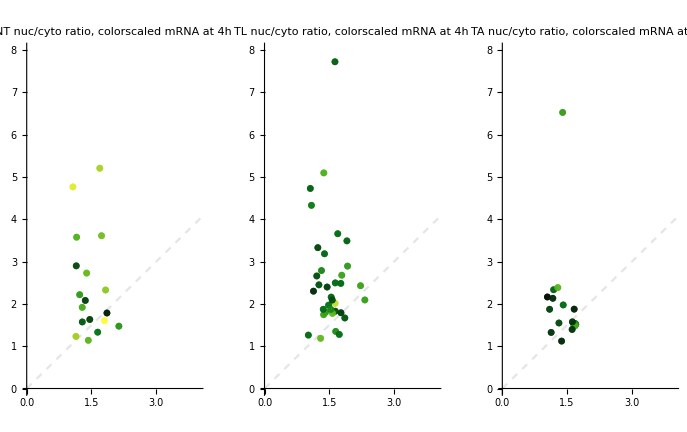

```mathematica
Row [{  barlegend  ,
{"The counts of cells per condition:  NT: "   Text[counts[[1]]]  ,   "  TL: " ,  Text[counts[[2]]]   ,  "  TA: " Text[counts[[3]]]   } }]
GraphicsRow[{
Show[xylineplot, Table[ListPlot[{myRatioTimeNT[[i,All,2]]}, PlotMarkers-> NTplotmarkersSCALED[[i]]],{i,1,Length@NTplotmarkersSCALED}], style[[All]] , PlotLabel -> "NT nuc/cyto ratio, colorscaled mRNA at 4h" ]   ,
Show[xylineplot, Table[ListPlot[{myRatioTimeTL[[i,All,2]]}, PlotMarkers-> TLplotmarkersSCALED[[i]]],{i,1,Length@TLplotmarkersSCALED}], style[[All]] , PlotLabel -> "TL nuc/cyto ratio, colorscaled mRNA at 4h" ]   ,
Show[xylineplot, Table[ListPlot[{myRatioTimeTA[[i,All,2]]}, PlotMarkers-> TAplotmarkersSCALED[[i]]],{i,1,Length@TAplotmarkersSCALED}], style[[All]] , PlotLabel -> "TA nuc/cyto ratio, colorscaled mRNA at 4h" ]      
},Spacings->25]
```

Number of spots TOTAL (only the PT’d cells):   {NT, TL, TA}

```mathematica
countNCPTall
```

{28,35,32}

Number of spots below the y=x line:   {NT, TL, TA}

```mathematica
{7, 8, 22}
```

{7,8,22}

Ratio of spots with accumulation gain  (above the y=x line):   {NT, TL, TA}

```mathematica
(countNCPTall -{7, 8, 22}  ) /countNCPTall  //N // #*100&
```

{75.,77.1429,31.25}

Ratio of spots without accumulation gain (below the y=x line):   {NT, TL, TA}

```mathematica
({7, 8, 22}  ) /countNCPTall  //N // #*100&
```

{25.,22.8571,68.75}

## Create PlotMarkers

```mathematica
color1 = Darker[Red]
color2 = Darker[Green]
color3 = Darker[Blue]
```

```mathematica
color1 = RGBColor[0.12, 0.77, 0.61]
color2 = RGBColor[0.66, 0.06, 0.78]
color3 = RGBColor[0.9500000000000001, Rational[2, 3], 0]
```

RGBColor[0.12, 0.77, 0.61]

RGBColor[0.66, 0.06, 0.78]

RGBColor[0.9500000000000001, Rational[2, 3], 0]

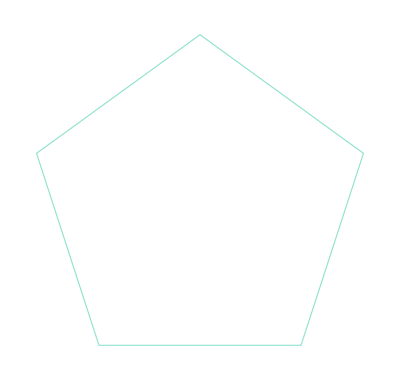
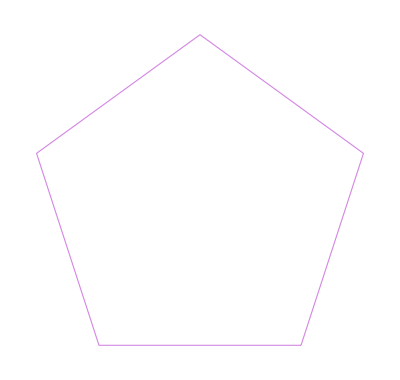
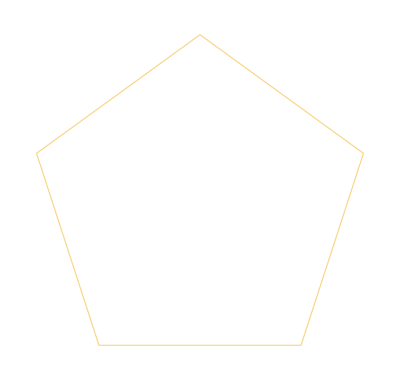

```mathematica
pentagons = Table[Graphics[{EdgeForm[{Opacity[0.5,c],Thick}],Opacity[0,White],ImageSize-> {1,1},Polygon[CirclePoints[5]]    }],{c, {color1, color2,color3}}]
```

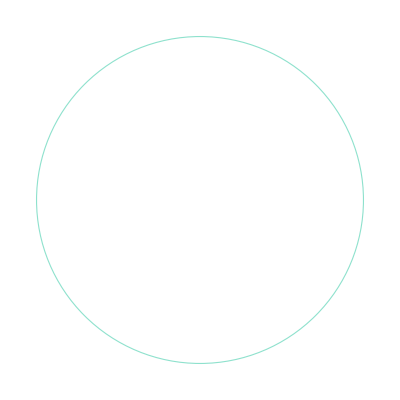
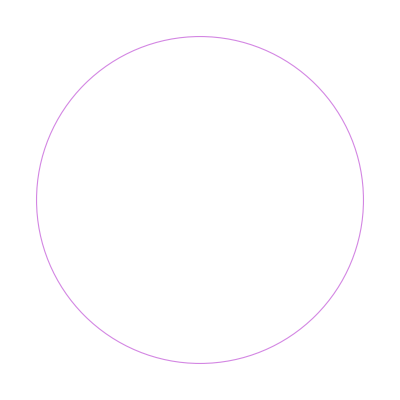
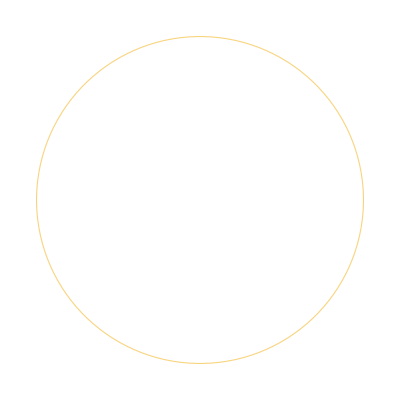

```mathematica
circles = Table[Graphics[{EdgeForm[{Opacity[0.5,c],Thick}],Opacity[0,White],ImageSize-> {1,1},Disk[] }],{c, {color1, color2,color3}}]
```

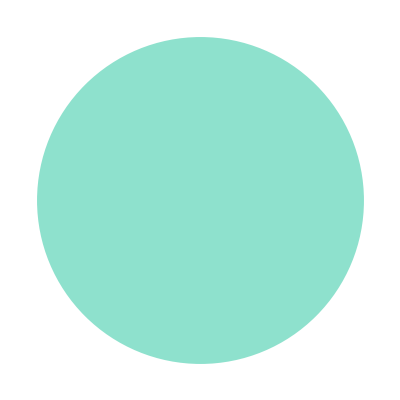
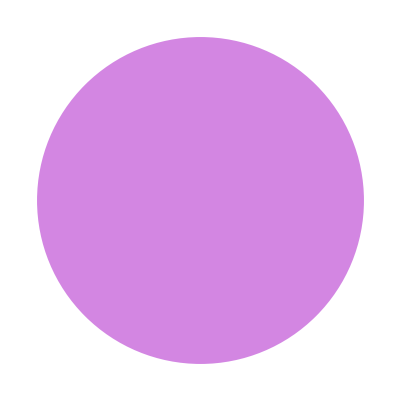
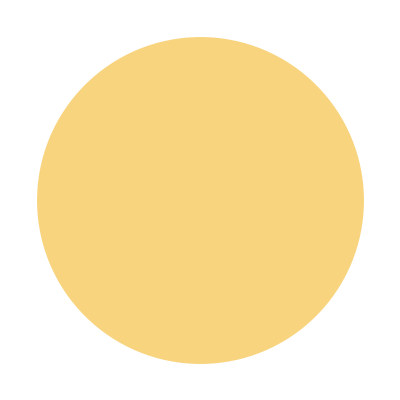

```mathematica
points = Table[Graphics[{Opacity[0.5,c],ImageSize-> {.5,.5},Disk[] }],{c, {color1, color2,color3}}]
```

```mathematica
triangles = Table[Graphics[{EdgeForm[{Opacity[0.5,c],Thick}],Opacity[0,White],ImageSize-> {1,1},Triangle[{{0,0},{.5,1},{1,0}}] }],{c, {color1, color2,color3}}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
squares = Table[Graphics[{EdgeForm[{Opacity[0.5,c],Thick}],Opacity[0,White],ImageSize-> {1,1}, Rectangle[]}],{c, {color1, color2,color3}}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
circle =Graphics[{EdgeForm[{Black,Thick}],Opacity[0,White],ImageSize-> Tiny,Disk[] }]
square = Graphics[{EdgeForm[{Black,Thick}],White,ImageSize->Tiny,Rectangle[]}]
triangle = Graphics[{EdgeForm[{Black,Thick}],White,ImageSize->Tiny ,  Triangle[{{0,0},{.5,1},{1,0}}]  }]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
ctrlpoint = Graphics[{Opacity[0.5,GrayLevel[0.03,0.5]],ImageSize-> {.5,.5},Disk[] }]
```

-Graphics-